# Histogram of Distances Store-Hub

```mathematica
SetDirectory[NotebookDirectory[]]
<<ModList.m
```

/home/lindorfer/ReWiTech/Masterarbeit/Programs/RetailerSet_Analysis

```mathematica
Distances={0,0,0,0,0,3222,2949,3903,3241,3419,3753,4283,3641,3566,3461,3703,4788,3062,4674,4030,2924,3217,3400,3312,3469,2199,4714,3053,3596,2828,2074,3447,3195,3781,3661,3122,4530,2289,2346,3731,3074,2001,3257,5173,3651,3867,4314,3196,4750,6267,2554,3425,3051,4357,4242,4362,3950,4796,4272,6014,4926,5396,6026,3260,6259,6468,4594,5123,5407,4143,3530,3383,3829,4204,2883,9761,8610,9652,9516,8208,9767,9130,11325,10191,12380,7426,9397,7925,7915,7874,7656,7069,8571,7964,8650,7526,8063,8659,7362,7730,9552,7873,7834,7932,6458,8937,7809,7374,8085,8151,9027,9915,7796,8733,8246,6628,9347,8768,7448,8751,9102,7775,8162,9496,7165,7862,8285,6667,7678,8834,6775,8648,9883,6889,8784,8145,9218,9137,7065,7555,7164,7830,7875,7962,1181,1429,803,1251,1392,1826,2469,1664,1720,999,675,1318,1946,1583,995,1431,2641,1182,1564,1468,2111,928,1626,2672,113,3704,2358,1135,1302,1286,1603,871,1686,1388,591,1497,1907,1291,1423,1016,989,3420,1524,1945,1714,4326,4398,1810,2234,1546,1694,1663,1512,1701,1039,12903,14182,8200,7943,9346,8257,8278,8836,9167,2157,2514,3834,1427,2657,3532,2377,3609,3357,1631,4819,2559,3774,2428,1739,2467,2241,2025,2015,3126,1849,2649,2997,2553,3317,2539,1523,1872,2852,2282,3073,1926,2769,2026,4227,1654,1765,1819,3357,2906,2722,2255,2024,2126,5493,5818,2285,5930,6304,5113,7240,6147,6107,5967,5704,2582,2897,3046,2748,2910,3347,1883,3144,3085,2754,2510,2284,8949,9434,6515,6076,8468,4867,6678,7494,6938,5692,5779,6075,6413,5997,7023,7124,5981,6054,5767,6586,6141,6523,6107,7479,5478,7480,6688,7682,6144,7462,6029,6060,7244,4872,5655,5827,5054,8371,7196,6515,5789,6045,5807,5126,5783,5056,6232,6950,6092,5949,6569,6883,5627,7374,7011,7346,6628,7272,6794,5481,7420,10960,11006,5602,10347,8016,8458,8405,6917,6236,6009,6178,6981,7684,7843,5431,7387,6290,4408,5121,5033,5879,4658,6125,3572,4819,4196,8105,6089,5921,5605,6354,5652,4379,3467,1853,3773,3538,3501,4164,5223,3896,2692,2742,5794,5022,5942,5384,6081,4508,2341,4269,4698,5998,4237,5993,6075,5126,10534,6254,9834,9325,7293,7773,6869,7017,6131,10161,9503,9815,5003,8205,5958,7544,5828,8625,7180,9623,8479,7186,6918,10125,9030,8610,10377,6914,6626,6447,4019,6513,3361,4649,6147,3648,6897,6466,6532,6078,6649,8033,6868,7529,6262,7519,6699,8450,6593,8127,8530,9409,9863,6820,5632,4902,7055,7932,8534,8608,8296,8924,8135,6183,5059,6860,7916,6538,6256,7463,4774,3498,6513,6971,8862,7858,4670,6771,9050,4312,6586,5883,5279,3533,2859,2743,2148,1938,1951,2742,4783,2470,1855,1681,5732,2116,3387,2514,2121,3929,2492,1998,3110,1491,2336,1669,3600,3403,3775,4447,3383,2947,2431,1821,2646,2116,2519,2096,4669,2905,2219,2755,3000,1945,2059,3776,2037,1985,1491,1638,1662,1576,5046,5996,5771,4576,5761,2740,6492,2198,2160,1851,12013,8939,11512,11873,11582,11518,11366,10589,11279,13173,11783,8916,10356,14320,8997,11663,9718,8860,14577,9942,9554,11750,12499,13414,9550,9713,11159,9061,10715,12143,13873,11804,10088,11424,13883,12375,11608,11565,9230,9968,14142,14372,11387,12632,11364,8808,7617,7870,7548,8530,8545,8095,8925,8077,8115,8348,8337,9037,9310,7605,6510,6807,9375,8159,8702,8365,6681,7675,7105,8916,8848,8807,7818,8776,9242,6895,8825,7555,8462,8151,8702,6341,8725,8487,9163,7031,7482,6672,7223,6341,5120,4128,3623,3314,3724,4576,4856,4294,4188,3700,4723,4894,3034,3149,5068,4693,4200,4729,5388,3307,3572,4247,6825,4538,3814,5416,5725,4111,5576,6448,7819,7271,7722,8092,5671,5078,5420,3966,3567,3778,5120,3502,2703,3295,4714,3033,4253,4718,3907,4140,3855,3080,2093,1996,1438,3473,3831,1809,2157,2788,4348,2845,3483,5259,1898,3431,2845,1933,3727,1430,2360,6932,3700,4334,3718,1923,4210,1814,3933,1467,1729,1651,1964,1624,1630,2033,1610,4017,2173,1826,1733,4174,4097,4383,4091,1472,5284,2426,4266,3878,2804,3861,1232,1899,3524,1846,6428,4287,3021,2768,2852};
```

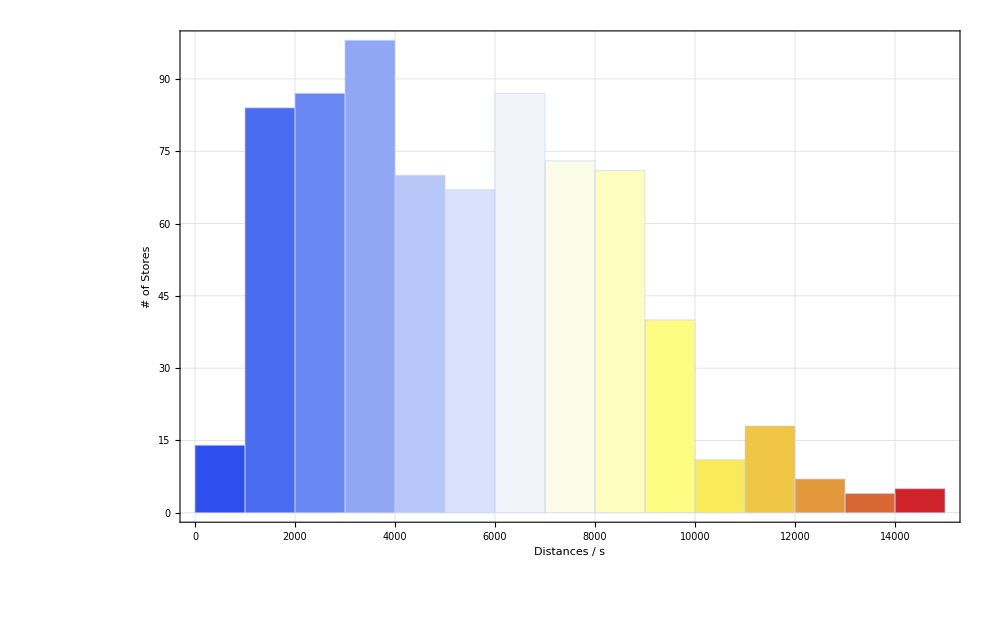

```mathematica
HistDistances=Histogram[Distances,
Frame->True,
LabelStyle->{30,Black},
FrameLabel->{{"# of Stores",None},{"Distances / s",Style["Distances Stores to Hub",40]}},
LabelStyle->25,
ChartStyle->{{EdgeForm[Thick]},"TemperatureMap"},
PlotTheme->{"Classic","Detailed"},
ImageSize->1000]
```

```mathematica
(84+87+98+70+67+87+73+71)/736//N
```

0.865489

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lindorfer/ReWiTech/Masterarbeit/Programs/RetailerSet_Analysis

```mathematica
Export["DistancesStoresHub.pdf",HistDistances]
```

DistancesStoresHub.pdf

```mathematica
ddist
```

ddist

```mathematica
distall={{0,0,0,0,0,3222,2949,3903,3241,3419,3753,4283,3641,3566,3461,3703,4788,3062,4674,4030,2924,3217,3400,3312,3469,2199,4714,3053,3596,2828,2074,3447,3195,3781,3661,3122,4530,2289,2346,3731,3074,2001,3257,5173,3651,3867,4314,3196,4750,6267,2554,3425,3051,4357,4242,4362,3950,4796,4272,6014,4926,5396,6026,3260,6259,6468,4594,5123,5407,4143,3530,3383,3829,4204,2883,9761,8610,9652,9516,8208,9767,9130,11325,10191,12380,7426,9397,7925,7915,7874,7656,7069,8571,7964,8650,7526,8063,8659,7362,7730,9552,7873,7834,7932,6458,8937,7809,7374,8085,8151,9027,9915,7796,8733,8246,6628,9347,8768,7448,8751,9102,7775,8162,9496,7165,7862,8285,6667,7678,8834,6775,8648,9883,6889,8784,8145,9218,9137,7065,7555,7164,7830,7875,7962,1181,1429,803,1251,1392,1826,2469,1664,1720,999,675,1318,1946,1583,995,1431,2641,1182,1564,1468,2111,928,1626,2672,113,3704,2358,1135,1302,1286,1603,871,1686,1388,591,1497,1907,1291,1423,1016,989,3420,1524,1945,1714,4326,4398,1810,2234,1546,1694,1663,1512,1701,1039,12903,14182,8200,7943,9346,8257,8278,8836,9167,2157,2514,3834,1427,2657,3532,2377,3609,3357,1631,4819,2559,3774,2428,1739,2467,2241,2025,2015,3126,1849,2649,2997,2553,3317,2539,1523,1872,2852,2282,3073,1926,2769,2026,4227,1654,1765,1819,3357,2906,2722,2255,2024,2126,5493,5818,2285,5930,6304,5113,7240,6147,6107,5967,5704,2582,2897,3046,2748,2910,3347,1883,3144,3085,2754,2510,2284,8949,9434,6515,6076,8468,4867,6678,7494,6938,5692,5779,6075,6413,5997,7023,7124,5981,6054,5767,6586,6141,6523,6107,7479,5478,7480,6688,7682,6144,7462,6029,6060,7244,4872,5655,5827,5054,8371,7196,6515,5789,6045,5807,5126,5783,5056,6232,6950,6092,5949,6569,6883,5627,7374,7011,7346,6628,7272,6794,5481,7420,10960,11006,5602,10347,8016,8458,8405,6917,6236,6009,6178,6981,7684,7843,5431,7387,6290,4408,5121,5033,5879,4658,6125,3572,4819,4196,8105,6089,5921,5605,6354,5652,4379,3467,1853,3773,3538,3501,4164,5223,3896,2692,2742,5794,5022,5942,5384,6081,4508,2341,4269,4698,5998,4237,5993,6075,5126,10534,6254,9834,9325,7293,7773,6869,7017,6131,10161,9503,9815,5003,8205,5958,7544,5828,8625,7180,9623,8479,7186,6918,10125,9030,8610,10377,6914,6626,6447,4019,6513,3361,4649,6147,3648,6897,6466,6532,6078,6649,8033,6868,7529,6262,7519,6699,8450,6593,8127,8530,9409,9863,6820,5632,4902,7055,7932,8534,8608,8296,8924,8135,6183,5059,6860,7916,6538,6256,7463,4774,3498,6513,6971,8862,7858,4670,6771,9050,4312,6586,5883,5279,3533,2859,2743,2148,1938,1951,2742,4783,2470,1855,1681,5732,2116,3387,2514,2121,3929,2492,1998,3110,1491,2336,1669,3600,3403,3775,4447,3383,2947,2431,1821,2646,2116,2519,2096,4669,2905,2219,2755,3000,1945,2059,3776,2037,1985,1491,1638,1662,1576,5046,5996,5771,4576,5761,2740,6492,2198,2160,1851,12013,8939,11512,11873,11582,11518,11366,10589,11279,13173,11783,8916,10356,14320,8997,11663,9718,8860,14577,9942,9554,11750,12499,13414,9550,9713,11159,9061,10715,12143,13873,11804,10088,11424,13883,12375,11608,11565,9230,9968,14142,14372,11387,12632,11364,8808,7617,7870,7548,8530,8545,8095,8925,8077,8115,8348,8337,9037,9310,7605,6510,6807,9375,8159,8702,8365,6681,7675,7105,8916,8848,8807,7818,8776,9242,6895,8825,7555,8462,8151,8702,6341,8725,8487,9163,7031,7482,6672,7223,6341,5120,4128,3623,3314,3724,4576,4856,4294,4188,3700,4723,4894,3034,3149,5068,4693,4200,4729,5388,3307,3572,4247,6825,4538,3814,5416,5725,4111,5576,6448,7819,7271,7722,8092,5671,5078,5420,3966,3567,3778,5120,3502,2703,3295,4714,3033,4253,4718,3907,4140,3855,3080,2093,1996,1438,3473,3831,1809,2157,2788,4348,2845,3483,5259,1898,3431,2845,1933,3727,1430,2360,6932,3700,4334,3718,1923,4210,1814,3933,1467,1729,1651,1964,1624,1630,2033,1610,4017,2173,1826,1733,4174,4097,4383,4091,1472,5284,2426,4266,3878,2804,3861,1232,1899,3524,1846,6428,4287,3021,2768,2852},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,3222,2949,3903,3241,3419,3753,4283,3641,3566,3461,3703,4788,3062,4674,4030,2924,3217,3400,3312,3469,2199,4714,3053,3596,2828,2074,3447,3195,3781,3661,3122,4530,2289,2346,3731,3074,2001,3257,5173,3651,3867,4314,3196,4750,6267,2554,3425,3051,4357,4242,4362,3950,4796,4272,6014,4926,5396,6026,3260,6259,6468,4594,5123,5407,4143,3530,3383,3829,4204,2883,9761,8610,9652,9516,8208,9767,9130,11325,10191,12380,7426,9397,7925,7915,7874,7656,7069,8571,7964,8650,7526,8063,8659,7362,7730,9552,7873,7834,7932,6458,8937,7809,7374,8085,8151,9027,9915,7796,8733,8246,6628,9347,8768,7448,8751,9102,7775,8162,9496,7165,7862,8285,6667,7678,8834,6775,8648,9883,6889,8784,8145,9218,9137,7065,7555,7164,7830,7875,7962,1181,1429,803,1251,1392,1826,2469,1664,1720,999,675,1318,1946,1583,995,1431,2641,1182,1564,1468,2111,928,1626,2672,113,3704,2358,1135,1302,1286,1603,871,1686,1388,591,1497,1907,1291,1423,1016,989,3420,1524,1945,1714,4326,4398,1810,2234,1546,1694,1663,1512,1701,1039,12903,14182,8200,7943,9346,8257,8278,8836,9167,2157,2514,3834,1427,2657,3532,2377,3609,3357,1631,4819,2559,3774,2428,1739,2467,2241,2025,2015,3126,1849,2649,2997,2553,3317,2539,1523,1872,2852,2282,3073,1926,2769,2026,4227,1654,1765,1819,3357,2906,2722,2255,2024,2126,5493,5818,2285,5930,6304,5113,7240,6147,6107,5967,5704,2582,2897,3046,2748,2910,3347,1883,3144,3085,2754,2510,2284,8949,9434,6515,6076,8468,4867,6678,7494,6938,5692,5779,6075,6413,5997,7023,7124,5981,6054,5767,6586,6141,6523,6107,7479,5478,7480,6688,7682,6144,7462,6029,6060,7244,4872,5655,5827,5054,8371,7196,6515,5789,6045,5807,5126,5783,5056,6232,6950,6092,5949,6569,6883,5627,7374,7011,7346,6628,7272,6794,5481,7420,10960,11006,5602,10347,8016,8458,8405,6917,6236,6009,6178,6981,7684,7843,5431,7387,6290,4408,5121,5033,5879,4658,6125,3572,4819,4196,8105,6089,5921,5605,6354,5652,4379,3467,1853,3773,3538,3501,4164,5223,3896,2692,2742,5794,5022,5942,5384,6081,4508,2341,4269,4698,5998,4237,5993,6075,5126,10534,6254,9834,9325,7293,7773,6869,7017,6131,10161,9503,9815,5003,8205,5958,7544,5828,8625,7180,9623,8479,7186,6918,10125,9030,8610,10377,6914,6626,6447,4019,6513,3361,4649,6147,3648,6897,6466,6532,6078,6649,8033,6868,7529,6262,7519,6699,8450,6593,8127,8530,9409,9863,6820,5632,4902,7055,7932,8534,8608,8296,8924,8135,6183,5059,6860,7916,6538,6256,7463,4774,3498,6513,6971,8862,7858,4670,6771,9050,4312,6586,5883,5279,3533,2859,2743,2148,1938,1951,2742,4783,2470,1855,1681,5732,2116,3387,2514,2121,3929,2492,1998,3110,1491,2336,1669,3600,3403,3775,4447,3383,2947,2431,1821,2646,2116,2519,2096,4669,2905,2219,2755,3000,1945,2059,3776,2037,1985,1491,1638,1662,1576,5046,5996,5771,4576,5761,2740,6492,2198,2160,1851,12013,8939,11512,11873,11582,11518,11366,10589,11279,13173,11783,8916,10356,14320,8997,11663,9718,8860,14577,9942,9554,11750,12499,13414,9550,9713,11159,9061,10715,12143,13873,11804,10088,11424,13883,12375,11608,11565,9230,9968,14142,14372,11387,12632,11364,8808,7617,7870,7548,8530,8545,8095,8925,8077,8115,8348,8337,9037,9310,7605,6510,6807,9375,8159,8702,8365,6681,7675,7105,8916,8848,8807,7818,8776,9242,6895,8825,7555,8462,8151,8702,6341,8725,8487,9163,7031,7482,6672,7223,6341,5120,4128,3623,3314,3724,4576,4856,4294,4188,3700,4723,4894,3034,3149,5068,4693,4200,4729,5388,3307,3572,4247,6825,4538,3814,5416,5725,4111,5576,6448,7819,7271,7722,8092,5671,5078,5420,3966,3567,3778,5120,3502,2703,3295,4714,3033,4253,4718,3907,4140,3855,3080,2093,1996,1438,3473,3831,1809,2157,2788,4348,2845,3483,5259,1898,3431,2845,1933,3727,1430,2360,6932,3700,4334,3718,1923,4210,1814,3933,1467,1729,1651,1964,1624,1630,2033,1610,4017,2173,1826,1733,4174,4097,4383,4091,1472,5284,2426,4266,3878,2804,3861,1232,1899,3524,1846,6428,4287,3021,2768,2852},{3269,0,0,0,3269,0,878,2056,1134,1704,1888,2419,1705,997,1524,1838,2941,1459,2676,2166,1321,1044,1073,1376,1344,1671,2850,1071,1993,1042,1689,482,1457,3387,2720,903,2532,1698,1754,1794,2689,2124,1299,3326,1786,1930,2467,586,2813,4402,1393,1822,881,2360,2306,2426,2103,3193,2426,4078,2989,3459,4090,641,4323,4532,2658,3125,3410,2296,1665,805,1964,2267,947,12324,11174,12215,11437,10771,12331,10017,13889,12755,14943,6182,8153,6681,6671,6630,6413,5825,7328,6720,7406,6282,6819,7416,6118,6487,8308,6629,6590,6688,5214,7693,6565,6130,6841,6907,7783,8671,6552,7489,7002,5384,8103,7524,6204,7507,7858,6531,6918,8253,5921,6618,7042,5423,6434,7590,5531,7404,8639,5645,7540,6901,7974,7893,5821,6311,5920,6586,6631,6718,3770,2610,3248,3857,3998,2798,3738,4258,4283,2845,3280,3019,4510,4147,2769,2932,3675,3745,4154,3242,4081,3209,2891,4173,3237,5038,3859,2636,2778,3850,2495,3476,4291,3952,3575,4061,4400,3736,4029,3344,2917,4921,3025,2202,2377,4857,4928,2282,3206,4109,4258,4227,2484,4295,3629,10967,12246,6264,6007,7409,6321,6342,6900,7231,4721,5077,6397,3990,5220,6096,4941,6172,5920,4194,7382,5123,6338,4992,4303,5031,4805,4589,4578,5690,4413,5213,5561,5116,5881,5102,4086,4436,5416,4657,5637,4489,5332,4589,6791,4217,4329,4382,5920,4527,5285,4818,4587,4690,8057,8382,4848,8493,8868,7677,9804,8710,8670,8531,8267,5146,5460,5610,5312,5473,5910,4446,5708,5649,5317,5073,4847,9097,8600,4431,4140,6532,2931,4741,5558,5002,3756,3843,4138,4476,3913,5086,5188,4044,4118,3831,4650,4205,4587,4023,5543,3394,5543,4752,5745,4208,5526,4172,4124,5308,2936,3718,3891,3118,6434,5260,4579,3853,4109,3810,3189,3846,3120,4296,5014,4156,4013,4632,4947,3690,5437,5074,5410,4692,5335,4858,3545,5484,9024,9070,3518,8411,6079,6522,6469,4980,4382,4073,7707,9545,10278,10406,7876,9951,8884,7002,7715,7627,8246,7222,8379,6165,7382,6760,10669,7622,7809,7859,8918,7850,6973,6061,4446,6367,6132,6095,6758,7817,6490,5286,5306,8048,7615,7513,7977,7742,7071,4935,6833,7143,7661,6831,7522,8329,7720,9704,8142,9004,8495,7897,8887,5625,8131,6882,9332,8673,8985,6117,6961,7846,6301,7716,9130,8295,8794,8985,8550,5674,8882,8200,7367,9548,8029,7779,7198,6583,9077,5925,7212,8710,6211,9461,9030,9095,7324,6813,6790,4932,8183,7864,10083,7817,8825,9156,10690,11093,11972,12427,9384,8195,7466,9619,10495,11097,11171,10859,11487,10245,7820,7622,9424,5979,9102,8820,10026,7337,6062,9077,5035,11426,10421,7233,9334,11613,6876,9150,8447,7842,4284,2935,3922,4500,4383,4211,3505,5534,4914,4299,4125,6106,4561,5831,4431,4566,4418,3834,3852,4154,3936,4780,4113,4351,4517,4149,5198,5828,5392,4876,4094,4738,4561,4964,4541,5420,5350,4664,2871,4199,4389,4504,4527,4482,4429,4084,4083,4107,4021,6160,7111,6885,5690,6876,5334,6365,4283,4605,4296,10077,7003,9576,9936,9646,9582,9430,8653,9342,11237,9847,6980,8420,12384,7060,9726,7782,6924,12641,8006,7618,9813,10563,11478,7614,7777,9222,7125,8779,10207,11937,9868,8151,9488,11947,10438,9672,9629,7294,8032,12205,12436,9451,10695,9428,6872,5681,5934,5612,6594,6608,6158,6988,6140,6179,6411,6401,7101,7373,5669,4574,4871,7439,6222,6765,6429,4745,5738,5168,6980,6912,6870,5882,6839,7306,4958,6889,5618,6526,6215,6765,4405,6789,6550,7226,5095,5545,4736,5287,4405,3036,1446,1848,3713,1098,4998,3475,1668,2905,1343,3285,2810,1830,1945,3862,2610,1575,3523,4144,1554,1819,2010,5581,2143,1731,4172,4482,2027,4332,5204,6177,6027,6478,6009,4427,3872,4176,1907,1807,2025,3914,2671,1907,3076,2630,1739,1804,2634,2153,3853,2346,2078,4657,4559,4001,6036,6395,4372,4721,5352,6911,5408,6046,7822,4462,5994,5409,4496,6290,3994,4923,9496,6263,6898,6282,4487,6774,4377,6496,4031,4293,4214,4527,4188,4193,4597,4173,6580,4736,4389,4297,6737,6660,6946,6654,4035,7848,4989,6829,6441,5368,6425,3796,4463,6087,4410,8992,6850,5585,5331,5415},{2885,0,0,0,2885,861,0,1740,684,1254,1572,2103,1367,1246,1186,1522,2625,1075,2399,1850,937,942,1126,1038,1194,1287,2534,599,1609,658,1306,1288,1007,3003,2336,847,2255,1314,1370,1456,2305,1740,983,3010,1470,1592,2151,835,2475,4086,1009,1438,214,2082,1968,2088,1787,2809,2110,3739,2651,3121,3752,1102,3984,4193,2320,2848,3133,1980,1349,1053,1648,1929,962,11941,10790,11831,11099,10387,11947,9679,13505,12371,14559,6014,7985,6513,6503,6462,6245,5658,7160,6552,7238,6114,6651,7248,5951,6319,8140,6462,6423,6521,5046,7525,6397,5962,6673,6739,7616,8504,6385,7322,6834,5216,7935,7356,6037,7339,7690,6363,6751,8085,5753,6451,6874,5255,6267,7422,5364,7236,8472,5477,7372,6733,7807,7725,5654,6143,5752,6418,6463,6550,3387,2226,2864,3473,3614,2414,3354,3874,3899,2461,2896,2636,4126,3763,2385,2548,3291,3361,3770,2859,3697,2825,2507,3789,2853,4654,3475,2252,2395,3466,2111,3092,3907,3568,3191,3677,4016,3352,3645,2960,2533,4537,2641,1818,1993,4473,4544,1898,2822,3725,3874,3843,2100,3911,3245,10629,11908,5925,5669,7071,5983,6003,6562,6893,4337,4693,6013,3607,4836,5712,4557,5788,5536,3810,6998,4739,5954,4608,3919,4647,4421,4205,4194,5306,4029,4829,5177,4732,5497,4719,3702,4052,5032,4273,5253,4105,4948,4205,6407,3833,3945,3998,5536,4143,4901,4434,4203,4306,7673,7998,4464,8109,8484,7293,9420,8326,8286,8147,7884,4762,5076,5226,4928,5089,5527,4062,5324,5265,4933,4690,4463,8758,8262,4593,3801,6193,2592,4403,5220,4664,3417,3504,3800,4138,4076,4748,4849,3706,3779,3493,4312,3866,4249,4185,5205,3556,5205,4414,5407,3870,5187,3754,3786,4969,2598,3380,3553,2780,6096,4922,4241,3515,3770,3533,2851,3508,2782,3958,4676,3818,3674,4294,4608,3352,5099,4736,5072,4354,4997,4520,3206,5146,8686,8732,3681,8073,5741,6184,6130,4642,3962,3734,7539,9161,9894,10022,7492,9567,8500,6618,7331,7243,8089,6838,8211,5782,6998,6376,10285,7454,7641,7691,8534,7682,6589,5677,4062,5983,5748,5711,6374,7433,6106,4902,4922,7880,7231,7345,7593,7574,6687,4551,6449,6759,7493,6447,7354,8161,7336,9536,7974,8836,8327,7729,8719,5457,7963,6714,9164,8505,8818,5950,6793,7678,6133,7548,8962,8127,8626,8817,8383,5506,8714,8032,7199,9380,7861,7611,7030,6199,8693,5541,6828,8326,5827,9077,8646,8711,6986,6475,6452,4594,7845,7526,9699,7478,8487,8772,10306,10710,11588,12043,9000,7811,7082,9235,10111,10713,10787,10475,11103,9906,7482,7238,9040,5641,8718,8436,9642,6953,5678,8693,4697,11042,10037,6849,8950,11229,6492,8766,8063,7458,4116,2767,3754,4208,3999,4012,3337,5366,4530,3915,3741,5938,4177,5447,4264,4182,4250,3666,3684,3986,3552,4396,3730,4183,4349,3981,5030,5444,5008,4492,3882,4570,4177,4580,4157,5252,4966,4280,2703,4031,4005,4120,4359,4098,4045,3700,3699,3723,3637,5992,6943,6717,5522,6708,4950,6197,4115,4221,3912,9739,6664,9238,9598,9308,9244,9092,8314,9004,10898,9509,6641,8082,12045,6722,9388,7444,6586,12303,7668,7280,9475,10225,11139,7275,7439,8884,6787,8440,9869,11599,9529,7813,9149,11608,10100,9333,9290,6956,7693,11867,12097,9113,10357,9090,6534,5342,5595,5274,6255,6270,5820,6650,5802,5841,6073,6063,6763,7035,5331,4236,4533,7101,5884,6427,6090,4407,5400,4830,6642,6573,6532,5544,6501,6968,4620,6550,5280,6187,5876,6427,4066,6451,6212,6888,4757,5207,4397,4949,4067,3198,1802,1702,3545,1411,4831,3307,1981,2737,1700,3117,2972,1662,1777,3694,2772,1887,3355,3977,1386,1651,2340,5413,2263,1893,4004,4314,2189,4165,5036,6407,5859,6310,6171,4259,3704,4008,2045,1646,1857,3746,2503,1772,2908,2793,1604,2116,2796,1985,3685,2178,1910,4273,4175,3617,5653,6011,3988,4337,4968,6527,5025,5662,7438,4078,5610,5025,4112,5906,3610,4539,9112,5879,6514,5898,4103,6390,3993,6112,3647,3909,3830,4143,3804,3809,4213,3790,6196,4352,4005,3913,6353,6276,6562,6270,3651,7464,4605,6445,6057,4984,6041,3412,4079,5703,4026,8608,6466,5201,4947,5031},{3863,0,0,0,3863,2044,1873,0,1411,1034,656,1389,1167,1872,808,779,1322,1866,2327,459,1782,1522,1588,1101,1774,2427,1753,1977,2400,1687,2098,2101,1330,3795,3128,1428,2183,2081,2137,1532,3098,2506,1242,1707,1118,1312,1273,1898,1767,3306,1776,2230,1646,2010,1260,1085,443,3601,749,2831,1943,2413,3044,2412,3276,3485,1582,2776,3061,1102,690,1689,1073,1750,2102,11554,10403,11445,10391,10001,11560,8971,13118,12446,14634,7154,9125,7653,7643,7603,7385,6798,8300,7692,8378,7255,7791,8388,7091,7459,9280,7602,7563,7661,6186,8665,7537,7102,7814,7879,8756,9644,7525,8462,7974,6356,9076,8496,7177,8479,8830,7503,7891,9225,6894,7591,8014,6395,7407,8562,6504,8376,9612,6618,8512,7873,8947,8865,6794,7283,6892,7558,7603,7690,4340,2993,3817,4451,4592,3181,4121,4827,4878,3440,3875,3614,5104,4741,3363,3526,4057,4340,4723,3837,4574,3779,3648,4666,3831,5445,4352,3231,3161,4444,2958,4071,4886,4546,4169,4655,4893,4305,4623,3938,3487,5410,3519,2958,2759,5264,5196,2665,3589,4704,4852,4821,2867,4864,4199,9890,11170,5187,4931,6333,5245,5265,5824,6155,5315,5672,6992,4585,5815,6690,5535,6766,6515,4788,7977,5717,6932,5586,4897,5625,5399,5183,5172,6284,5007,5807,6155,5711,6475,5697,4680,5030,6010,5150,6231,5083,5926,5183,7385,4812,4923,4977,6515,5021,5879,5412,5181,5284,8651,8976,5443,9088,9462,8271,10398,9305,9265,9125,8862,5740,6055,6204,5906,6067,6505,5041,6302,6243,5912,5668,5441,8050,7554,4793,3063,5455,1854,3665,4481,3926,2679,2766,3062,3400,4276,4010,4111,2968,3041,2755,3573,3128,3511,3701,4467,3756,4467,3676,4669,3132,4449,3682,3048,4231,1860,2642,2815,2114,5358,4184,3503,2777,3032,3460,2113,2770,2044,3220,3938,3080,2936,3556,3870,2614,4361,3998,4334,3615,4259,3781,2468,4408,7947,7994,3881,7335,5003,5446,5392,3904,3543,2996,8679,10139,10848,11000,8445,10545,9454,7572,8285,8196,9043,7816,9288,6735,7977,7354,11263,8594,8781,8768,9512,8816,7542,6631,5016,6937,6701,6664,7328,8387,7060,5856,5900,8958,8185,8485,8547,8715,7666,5504,7427,7713,8634,7401,8494,9239,8289,10676,9114,9977,9467,8869,9859,6597,9103,7854,10304,9645,9958,7090,7933,8818,7273,8689,10102,9267,9766,9957,9523,6646,9854,9173,8339,10520,9001,8751,8170,7177,8365,6519,7155,7940,6805,8690,8259,9690,6078,5566,5744,3685,7137,6818,10663,6770,7779,9184,11284,10323,11706,12284,8613,7407,8060,8848,9724,10326,10401,11453,10716,9198,6573,8216,8653,4933,8343,8325,9256,7932,6656,8365,3788,10655,11015,7827,8563,11906,6819,9471,9041,8437,5256,3907,4894,5162,4953,4966,4477,6506,5484,4869,4695,7078,5130,6401,5404,5135,5390,4806,4824,5126,4505,5350,4683,5323,5489,5121,6170,6397,5961,5446,4836,5660,5130,5534,5110,6392,5919,5233,3843,5171,4959,5073,5499,5051,4999,4654,4653,4676,4590,7133,8083,7857,6662,7848,5903,7337,5213,5174,4865,9001,5926,8500,8860,8570,8506,8354,7576,8266,10160,8771,5903,7343,11307,5984,8650,6706,5848,11565,6930,6542,8737,9486,10401,6537,6701,8146,6049,7702,9131,10861,8791,7075,8411,10870,9362,8595,8552,6218,6955,11129,11359,8375,9619,8352,5826,4634,4887,4565,5547,5532,5082,5942,5094,5133,5335,5355,6055,6327,4623,3528,3825,6393,5176,5719,5382,3699,4692,4122,5933,5865,5824,4836,5793,6260,3912,5842,4572,5479,5168,5719,3358,5742,5474,6180,4049,4499,3689,4241,3359,3704,2486,2831,4685,2029,5971,4447,2495,3877,2410,4257,3479,2802,2917,4834,3278,2506,4495,5117,2526,2791,2629,6553,2191,2714,5144,5454,3010,5305,6176,6539,6342,6874,6371,5399,4845,5149,2494,2786,2997,4886,3643,2912,4048,3299,2744,2217,3302,3126,4826,3318,3050,5251,5154,4596,6631,6989,4967,5315,5946,7506,6003,6641,8417,5056,6588,6003,5091,6884,4588,5518,10090,6858,7492,6876,5081,7368,4971,7091,4625,4887,4808,5121,4782,4788,5191,4768,7175,5331,4984,4891,7331,7255,7541,7249,4629,8442,5583,7424,7036,5962,7019,4390,5057,6682,5004,9586,7445,6179,5925,6009},{3254,0,0,0,3254,1141,804,1413,0,929,1263,1794,1742,1615,1383,1213,2298,1257,2827,1541,1172,1262,1493,1466,1561,1831,2225,1288,1791,1077,1489,1559,682,3185,2518,1046,2683,1471,1527,1884,2489,1897,884,2683,1161,1863,1824,1204,2318,3777,1166,1620,598,2510,1811,1876,1460,2991,1783,3582,2494,2964,3595,1372,3827,4036,2133,3276,3561,1653,1040,1423,1339,2301,1484,12105,10954,11996,10942,10552,12111,9522,13669,12997,15185,6615,8587,7114,7104,7064,6846,6259,7761,7154,7840,6716,7252,7849,6552,6920,8742,7063,7024,7122,5648,8127,6998,6563,7275,7340,8217,9105,6986,7923,7436,5817,8537,7958,6638,7941,8291,6964,7352,8686,6355,7052,7475,5857,6868,8024,5965,7838,9073,6079,7974,7334,8408,8326,6255,6745,6353,7019,7065,7152,3731,2383,3208,3842,3983,2571,3512,4218,4268,2830,3265,3004,4495,4132,2754,2917,3448,3730,4114,3227,3964,3169,3101,4057,3222,4836,3743,2621,2552,3835,2349,3461,4276,3937,3559,4045,4283,3696,4014,3328,2877,4800,2909,2412,2150,4655,4727,2055,2979,4094,4242,4212,2257,4255,3589,10442,11721,5738,5482,6884,5796,5817,6375,6706,4705,5062,6382,3975,5205,6081,4926,6157,5905,4179,7367,5107,6323,4976,4287,5016,4790,4574,4563,5675,4397,5198,5545,5101,5866,5087,4071,4421,5401,4541,5622,4474,5317,4574,6775,4202,4314,4367,5905,4411,5270,4803,4572,4675,8042,8367,4833,8478,8853,7662,9789,8695,8655,8515,8252,5131,5445,5595,5297,5458,5895,4431,5692,5633,5302,5058,4832,8601,8105,5153,3614,6007,2406,4216,5033,4477,3230,3317,3613,3951,4636,4561,4662,3519,3592,3306,4125,3680,4062,4252,5018,4116,5018,4227,5220,3683,5001,4182,3599,4783,2411,3193,3366,2665,5909,4735,4054,3328,3584,3960,2664,3321,2595,3771,4489,3631,3488,4107,4421,3165,4912,4549,4885,4167,4810,4333,3019,4959,8499,8545,4241,7886,5554,5997,5944,4455,4094,3547,8140,9530,10238,10391,7836,9936,8844,6962,7675,7587,8433,7207,8679,6126,7367,6745,10654,8056,8242,8159,8903,8206,6933,6021,4407,6327,6092,6055,6718,7777,6450,5246,5290,8348,7576,7946,7938,8176,7056,4895,6818,7103,8095,6791,7955,8629,7680,10138,8575,9438,8929,8330,9321,6058,8565,7315,9765,9107,9419,6551,7394,8279,6734,8150,9564,8728,9228,9418,8984,6108,9315,8634,7800,9981,8462,8213,7632,6568,8916,5909,6990,8491,6196,9241,8810,9080,6829,6318,6295,4437,7688,7369,10068,7321,8330,9141,10675,10874,11957,12412,9164,7958,7451,9399,10276,10878,10952,10844,11268,9749,7325,7607,9204,5484,8895,8876,9807,7322,6046,8916,4540,11206,10406,7218,9115,11598,6654,9134,8431,7827,4717,3369,4356,4552,4343,4356,3938,5968,4874,4260,4086,6540,4521,5792,4919,4526,4851,4267,4285,4588,3896,4740,4074,4785,4950,4583,5631,5788,5352,4836,4226,5051,4521,4924,4501,5853,5310,4624,3304,4633,4349,4464,4961,4442,4389,4045,4043,4067,3981,6594,7544,7319,6124,7309,5294,6799,4603,4565,4256,9552,6478,9051,9411,9121,9057,8905,8127,8817,10711,9322,6454,7895,11859,6535,9201,7257,6399,12116,7481,7093,9288,10038,10953,7088,7252,8697,6600,8253,9682,11412,9342,7626,8963,11422,9913,9147,9103,6769,7507,11680,11911,8926,10170,8903,6377,5185,5438,5117,6099,6083,5633,6493,5645,5684,5886,5906,6606,6878,5174,4079,4376,6944,5727,6270,5933,4250,5243,4673,6485,6417,6375,5387,6344,6811,4463,6393,5123,6030,5720,6270,3910,6294,6025,6731,4600,5050,4241,4792,3910,3758,2171,2303,4146,1769,5432,3908,2339,3339,2069,3719,3532,2263,2379,4295,3332,2245,3956,4578,1987,2252,2698,6015,2691,2454,4606,4915,2750,4766,5638,7009,6461,6912,6731,4861,4306,4610,2630,2247,2458,4347,3105,2335,3510,3353,2056,2474,3356,2587,4287,2780,2512,4642,4544,3986,6021,6380,4357,4706,5337,6896,5393,6031,7807,4447,5979,5394,4481,6275,3978,4908,9481,6248,6883,6267,4472,6759,4362,6481,4016,4278,4199,4512,4172,4178,4582,4158,6565,4721,4374,4282,6722,6645,6931,6639,4020,7832,4974,6814,6426,5353,6410,3781,4448,6072,4394,8977,6835,5570,5316,5400},{3380,0,0,0,3380,1706,1370,1029,928,0,546,1102,1635,1714,1276,437,1814,1384,2772,981,1299,1365,1548,1476,1617,1958,1443,1536,1918,1204,1616,1944,459,3312,2645,1270,2628,1598,1654,1894,2615,2024,1084,2199,950,1757,1717,1740,2212,2996,1293,1747,1164,2455,1704,1769,1241,3118,1551,3323,2388,2858,3488,1938,3721,3930,2026,3221,3505,1546,616,1532,1214,2195,1801,11998,10847,11889,10835,10445,12005,9415,13563,12890,15078,6853,8825,7353,7343,7302,7084,6497,7999,7392,8078,6954,7491,8087,6790,7158,8980,7301,7262,7360,5886,8365,7236,6802,7513,7578,8455,9343,7224,8161,7674,6055,8775,8196,6876,8179,8530,7203,7590,8924,6593,7290,7713,6095,7106,8262,6203,8076,9311,6317,8212,7572,8646,8564,6493,6983,6592,7258,7303,7390,3857,2510,3335,3969,4109,2698,3639,4345,4395,2957,3392,3131,4621,4259,2881,3044,3575,3857,4241,3354,4091,3296,3228,4183,3349,4963,3870,2748,2679,3961,2475,3588,4403,4064,3686,4172,4410,3823,4140,3455,3004,4927,3036,2539,2277,4782,4853,2182,3106,4221,4369,4338,2384,4382,3716,10335,11614,5632,5375,6778,5689,5710,6268,6599,4832,5189,6509,4102,5332,6207,5053,6284,6032,4306,7494,5234,6450,5103,4414,5142,4917,4701,4690,5801,4524,5325,5672,5228,5992,5214,4198,4547,5527,4668,5749,4601,5444,4701,6902,4329,4441,4494,6032,4538,5397,4930,4699,4801,8169,8494,4960,8605,8979,7788,9916,8822,8782,8642,8379,5258,5572,5722,5424,5585,6022,4558,5819,5760,5429,5185,4959,8495,7999,5256,3508,5900,2299,4110,4926,4370,3124,3211,3507,3845,4738,4455,4556,3413,3486,3199,4018,3573,3955,4146,4911,4219,4912,4120,5114,3576,4894,4127,3492,4676,2304,3087,3259,2559,5803,4628,3947,3221,3477,3905,2558,3215,2488,3664,4382,3524,3381,4000,4315,3059,4806,4443,4778,4060,4704,4226,2913,4852,8392,8438,4343,7779,5448,5890,5837,4348,3987,3441,8378,9656,10365,10518,7963,10063,8971,7089,7802,7714,8560,7333,8806,6252,7494,6871,10780,8294,8480,8285,9030,8333,7060,6148,4533,6454,6219,6182,6845,7904,6577,5373,5417,8475,7702,8184,8064,8414,7183,5022,6944,7230,8333,6918,8194,8756,7807,10376,8813,9676,9167,8569,9559,6296,8803,7553,10003,9345,9657,6789,7633,8518,6972,8388,9802,8966,9466,9656,9222,6346,9553,8872,8038,10219,8700,8451,7870,6694,8809,6036,6845,8384,6323,9135,8704,9207,6215,5704,6188,4177,7581,7263,10194,7215,8224,9268,10802,10767,12151,12728,9058,7851,7577,9292,10169,10771,10845,10971,11161,9643,6710,7734,9098,5377,8788,8770,9700,7449,6173,8809,4280,11100,10533,7345,9008,11725,6509,9261,8558,7954,4955,3607,4594,4679,4470,4483,4177,6206,5001,4386,4212,6778,4648,5918,5046,4653,5089,4505,4530,4826,4023,4867,4200,5023,5188,4821,5869,5915,5479,4963,4353,5178,4648,5051,4628,6092,5437,4751,3542,4871,4476,4591,5199,4569,4516,4171,4170,4194,4108,6832,7782,7557,6362,7547,5421,7037,4730,4692,4383,9445,6371,8944,9304,9014,8950,8798,8021,8711,10605,9215,6348,7788,11752,6428,9095,7150,6292,12009,7374,6986,9182,9931,10846,6982,7145,8591,6493,8147,9575,11305,9236,7520,8856,11315,9807,9040,8997,6662,7400,11574,11804,8819,10063,8796,6270,5079,5332,5010,5992,5977,5527,6386,5539,5577,5780,5799,6499,6772,5067,3972,4269,6837,5621,6163,5827,4143,5137,4567,6378,6310,6269,5280,6238,6704,4357,6287,5017,5924,5613,6164,3803,6187,5919,6625,4493,4943,4134,4685,3803,3861,2328,2541,4384,1872,5670,4146,2442,3577,2253,3957,3635,2501,2617,4533,3435,2348,4194,4816,2225,2490,2801,6253,2636,2557,4844,5153,2853,5004,5876,7247,6699,7150,6834,5099,4544,4848,2732,2485,2696,4586,3343,2462,3748,3456,2183,2577,3459,2825,4525,3018,2750,4769,4671,4113,6148,6506,4484,4832,5463,7023,5520,6158,7934,4574,6106,5520,4608,6402,4105,5035,9607,6375,7009,6393,4598,6885,4489,6608,4142,4404,4326,4639,4299,4305,4708,4285,6692,4848,4501,4408,6849,6772,7058,6766,4147,7959,5101,6941,6553,5479,6536,3907,4574,6199,4521,9103,6962,5697,5443,5527},{3772,0,0,0,3772,1930,1759,646,1320,603,0,880,1370,1757,1011,438,1583,1775,2530,647,1690,1407,1591,1304,1660,2312,1244,1862,2309,1596,2007,1987,933,3704,3037,1313,2386,1989,2046,1735,3007,2415,1127,1968,807,1515,1476,1783,1970,2797,1685,2139,1555,2214,1463,1459,858,3510,1168,3092,2146,2616,3247,2297,3480,3689,1785,2979,3264,1305,409,1574,1071,1953,1987,11757,10606,11648,10594,10204,11763,9174,13321,12649,14837,7039,9011,7538,7528,7488,7270,6683,8185,7577,8263,7140,7676,8273,6976,7344,9165,7487,7448,7546,6072,8550,7422,6987,7699,7764,8641,9529,7410,8347,7860,6241,8961,8381,7062,8365,8715,7388,7776,9110,6779,7476,7899,6280,7292,8448,6389,8262,9497,6503,8397,7758,8832,8750,6679,7168,6777,7443,7489,7575,4249,2902,3726,4360,4501,3090,4030,4736,4786,3349,3784,3523,5013,4650,3272,3435,3966,4249,4632,3746,4483,3687,3533,4575,3740,5254,4261,3139,3070,4353,2867,3979,4795,4455,4078,4564,4802,4214,4532,3847,3396,5319,3427,2844,2668,4858,4687,2573,3498,4613,4761,4730,2776,4773,4108,10094,11373,5391,5134,6536,5448,5469,6027,6358,5224,5580,6900,4494,5724,6599,5444,6675,6424,4697,7885,5626,6841,5495,4806,5534,5308,5092,5081,6193,4916,5716,6064,5619,6384,5606,4589,4939,5919,5059,6140,4992,5835,5092,7294,4721,4832,4886,6424,4930,5788,5321,5090,5193,8560,8885,5352,8997,9371,8180,10307,9214,9173,9034,8771,5649,5963,6113,5815,5976,6414,4949,6211,6152,5820,5577,5350,8253,7757,4997,3267,5659,2058,3868,4685,4129,2883,2970,3265,3603,4479,4213,4315,3171,3244,2958,3777,3332,3714,3904,4670,3959,4670,3879,4872,3335,4653,3886,3251,4435,2063,2845,3018,2318,5561,4387,3706,2980,3236,3664,2316,2973,2247,3423,4141,3283,3140,3759,4073,2817,4564,4201,4537,3819,4462,3985,2672,4611,8151,8197,4084,7538,5206,5649,5596,4107,3746,3200,8564,10048,10756,10909,8354,10454,9362,7480,8194,8105,8951,7725,9197,6644,7886,7263,11172,8479,8666,8677,9421,8707,7451,6540,4925,6846,6610,6573,7237,8296,6968,5765,5809,8866,8094,8370,8456,8600,7575,5413,7336,7621,8519,7310,8379,9148,8198,10562,8999,9862,9353,8754,9745,6482,8989,7739,10189,9531,9843,6975,7818,8703,7158,8574,9987,9152,9651,9842,9408,6532,9739,9058,8224,10405,8886,8636,8056,7086,8568,6428,6646,8143,6714,8893,8462,9599,6016,5505,5947,3946,7340,7021,10586,6973,7982,9387,11193,10526,11910,12487,8817,7610,7969,9051,9928,10530,10604,11362,10920,9401,6511,8125,8857,5136,8547,8528,9459,7841,6565,8568,4049,10859,10924,7736,8767,12109,6310,9653,8950,8345,5141,3792,4780,5071,4862,4874,4362,6392,5393,4778,4604,6964,5039,6310,5289,5044,5275,4691,4709,5012,4414,5259,4592,5209,5374,5007,6055,6306,5870,5355,4744,5569,5039,5443,5019,6277,5828,5142,3728,5057,4868,4982,5385,4960,4908,4563,4561,4585,4499,7018,7968,7742,6548,7733,5812,7222,5121,5083,4774,9204,6130,8703,9063,8773,8709,8557,7779,8469,10363,8974,6107,7547,11511,6187,8853,6909,6051,11768,7133,6745,8940,9690,10605,6740,6904,8349,6252,7906,9334,11064,8994,7278,8615,11074,9565,8799,8756,6421,7159,11332,11563,8578,9822,8555,6029,4837,5090,4769,5751,5735,5285,6145,5297,5336,5538,5558,6258,6530,4826,3731,4028,6596,5379,5922,5585,3902,4895,4325,6137,6069,6027,5039,5996,6463,4115,6045,4775,5683,5372,5922,3562,5946,5677,6383,4252,4702,3893,4444,3562,3908,2371,2716,4570,1915,5856,4332,2485,3763,2296,4143,3682,2687,2802,4719,3481,2391,4380,5002,2411,2676,2844,6439,2394,2599,5030,5339,2895,5190,6062,6742,6885,7336,6574,5285,4730,5034,2697,2671,2882,4771,3528,2797,3934,3502,2629,2421,3506,3011,4711,3204,2936,5160,5063,4504,6540,6898,4875,5224,5855,7415,5912,6549,8325,4965,6497,5912,5000,6793,4497,5427,9999,6766,7401,6785,4990,7277,4880,6999,4534,4796,4717,5030,4691,4697,5100,4677,7083,5239,4892,4800,7240,7164,7450,7158,4538,8351,5492,7333,6944,5871,6928,4299,4966,6590,4913,9495,7354,6088,5834,5918},{4264,0,0,0,4264,2421,2250,1383,1811,1097,827,0,2107,2249,1748,975,820,2267,3267,1285,2182,1899,2083,2010,2151,2804,505,2354,2801,2088,2499,2478,1427,4195,3528,1805,3123,2481,2537,2429,3499,2907,1619,1205,1299,2252,2213,2275,2458,2057,2176,2630,2047,2950,2200,2196,1555,3536,1904,2329,2140,2253,3358,2789,3591,3800,2522,3716,4001,2042,963,2066,1563,2690,2479,11868,10717,11759,10705,10315,11875,9285,13433,12760,14948,7531,9502,8030,8020,7980,7762,7175,8677,8069,8755,7632,8168,8765,7468,7836,9657,7979,7940,8038,6563,9042,7914,7479,8191,8256,9133,10021,7902,8839,8351,6733,9453,8873,7554,8856,9207,7880,8268,9602,7270,7968,8391,6772,7784,8939,6881,8753,9989,6994,8889,8250,9324,9242,7171,7660,7269,7935,7980,8067,4741,3393,4218,4852,4993,3581,4522,5228,5278,3840,4275,4014,5505,5142,3764,3927,4458,4740,5124,4237,4974,4179,4024,5067,4232,4515,4753,3631,3562,4845,3359,4471,5286,4947,4569,5055,5293,4706,5024,4338,3887,5084,3919,3335,3160,4119,3948,3065,3990,5104,5253,5222,3267,5265,4599,10830,12110,6127,5871,7273,6185,6205,6764,7095,5715,6072,7392,4985,6215,7091,5936,7167,6915,5189,8377,6118,7333,5986,5298,6026,5800,5584,5573,6685,5407,6208,6555,6111,6876,6097,5081,5431,6411,5551,6632,5484,6327,5584,7785,5212,5324,5377,6915,5421,6280,5813,5582,5685,9052,9377,5843,9488,9863,8672,10799,9705,9665,9526,9262,6141,6455,6605,6307,6468,6905,5441,6702,6643,6312,6068,5842,8365,7868,5791,4003,6395,2794,4605,5421,4866,3619,3706,4002,4340,5273,4950,5051,3908,3981,3695,4513,4068,4451,4641,5407,4754,5407,4616,5609,4072,5389,4622,3988,5171,2800,3582,3755,3054,6298,5124,4443,3717,3972,4400,3053,3710,2984,4160,4878,4020,3876,4496,4810,3554,5301,4938,5274,4555,5199,4721,3408,5348,8887,8934,4878,8275,5943,6386,6332,4844,4483,3936,9056,10540,11248,11401,8846,10946,9854,7972,8685,8597,9443,8217,9689,7136,8377,7755,11664,8971,9158,9169,9913,9199,7943,7031,5417,7337,7102,7065,7728,8787,7460,6256,6300,9358,8586,8862,8948,9092,8066,5905,7828,8113,9010,7801,8871,9639,8690,11053,9491,10353,9844,9246,10236,6974,9480,8231,10681,10022,10335,7467,8310,9195,7650,9066,10479,9644,10143,10334,9900,7023,10231,9550,8716,10897,9378,9128,8547,6370,8679,6919,5907,8254,6728,9005,8574,10090,5276,4765,4999,3183,7451,7133,10978,7085,8094,9498,11653,10637,12021,12598,8928,7721,8461,9162,10039,10641,10715,11854,11031,9513,5772,8617,8968,5247,8658,8640,9570,8332,6319,8679,3286,10970,11416,8228,8878,12220,5570,9785,9441,8017,5633,4284,5271,5562,5353,5366,4854,6883,5885,5270,5096,7455,5531,6802,5781,5536,5767,5183,5201,5503,4906,5750,5084,5700,5866,5498,6547,6798,6362,5846,5236,6061,5531,5934,5511,6769,6320,5634,4220,5548,5360,5474,5876,5452,5400,5055,5053,5077,4991,7509,8460,8234,7039,8225,6304,7714,5613,5575,5266,9941,6866,9440,9800,9510,9446,9294,8516,9206,11100,9711,6843,8283,12247,6924,9590,7646,6788,12505,7870,7482,9677,10426,11341,7477,7641,9086,6989,8642,10071,11801,9731,8015,9351,11810,10302,9535,9492,7158,7895,12069,12299,9315,10559,9292,6140,4949,5202,4880,5862,6201,6022,6256,5409,5447,5781,5669,6369,6642,4937,3842,4139,6707,5491,6033,5697,4013,5007,4437,6248,6180,6139,5150,6108,6574,4227,6157,4887,5794,5483,6034,3673,6057,5921,6495,4363,4813,4004,4555,3673,4396,2863,3208,5062,2406,6348,4824,2976,4254,2787,4634,4170,3179,3294,5211,3969,2883,4872,5494,2903,3168,3336,6930,3131,3091,5521,5831,3387,5682,6553,7536,7376,7827,7368,5776,5221,5526,3267,3163,3374,5263,4020,3289,4425,3990,3121,3112,3994,3503,5202,3695,3427,5652,5554,4996,7031,7390,5367,5716,6347,7906,6403,7041,8817,5457,6989,6404,5491,7285,4988,5918,10491,7258,7893,7277,5482,7769,5372,7491,5026,5288,5209,5522,5182,5188,5592,5168,7575,5731,5384,5292,7732,7655,7941,7649,5030,8843,5984,7824,7436,6363,7420,4791,5458,7082,5404,9987,7845,6580,6326,6410},{3585,0,0,0,3585,1619,1434,1096,1677,1682,1303,2037,0,1446,464,1426,1981,1802,1409,1428,1665,1063,1092,513,1349,1987,2401,1537,2337,1385,2006,1676,1776,3731,3064,1002,1265,2042,2098,440,3006,2468,1066,2209,1180,576,1146,1473,1485,3953,1737,2166,1429,1092,977,1098,1088,3537,1106,2749,1661,2131,2762,1987,2994,3203,1329,1858,2142,975,1432,1264,1156,913,1662,11272,10121,11163,10109,9719,11278,8689,12836,12163,14352,6714,8686,7213,7203,7163,6945,6358,7860,7252,7939,6815,7351,7948,6651,7019,8840,7162,7123,7221,5747,8225,7097,6662,7374,7439,8316,9204,7085,8022,7535,5916,8636,8057,6737,8040,8390,7063,7451,8785,6454,7151,7574,5955,6967,8123,6064,7937,9172,6178,8073,7433,8507,8425,6354,6843,6452,7118,7164,7251,4087,2954,3564,4173,4314,3142,4082,4574,4600,3162,3597,3336,4826,4463,3086,3248,4018,4062,4470,3559,4397,3525,3208,4489,3553,5381,4175,2953,3119,4166,2811,3793,4608,4268,3891,4377,4716,4052,4345,3660,3234,5237,3342,2519,2721,5201,5272,2626,3550,4426,4574,4543,2828,4611,3945,9638,10917,4935,4678,6081,4992,5013,5571,5902,5037,5394,6714,4307,5537,6412,5257,6489,6237,4511,7699,5439,6654,5308,4619,5347,5121,4905,4894,6006,4729,5529,5877,5433,6197,5419,4402,4752,5732,4973,5953,4805,5648,4906,7107,4534,4645,4699,6237,4844,5601,5135,4903,5006,8373,8698,5165,8810,9184,7993,10120,9027,8987,8847,8584,5462,5777,5926,5628,5790,6227,4763,6024,5965,5634,5390,5163,7768,7272,3875,2811,5203,1602,3413,4229,3673,2427,2514,2810,3148,3357,3758,3859,2716,2789,2503,3321,2876,3258,3088,4214,2838,4215,3423,4417,2879,4197,2764,2795,3979,1607,2390,2562,1763,5106,3932,3250,2524,2780,2542,1861,2518,1791,2967,3686,2828,2684,3304,3618,2362,4109,3746,4081,3363,4007,3529,2216,4155,7695,7741,2962,7082,4751,5193,5140,3652,2971,2744,8228,9861,10594,10723,8192,10267,9200,7318,8031,7943,8789,7538,8901,6482,7699,7076,10985,8143,8330,8380,9234,8371,7289,6378,4763,6684,6448,6411,7074,8134,6806,5603,5622,8570,7932,8034,8294,8264,7388,5251,7149,7459,8183,7147,8043,8851,8036,10237,8663,9537,9028,8429,9409,6157,8653,7403,9864,9206,9518,6639,7493,8367,6833,8238,9662,8816,9327,9517,9072,6207,9414,8733,7899,10080,8550,8311,7720,6899,8082,6241,7528,7657,6528,8408,7977,9412,5996,5485,5462,3603,6854,6536,10381,6488,7497,8902,11057,10041,11424,12002,8331,7124,7782,8566,9442,10044,10118,11175,10434,8916,6491,7939,8371,4651,8061,8043,8973,7654,6378,8082,3707,10373,10737,7550,8281,11623,7192,9188,8763,8159,4805,3457,4444,4909,4699,4712,4026,6056,5231,4616,4442,6628,4877,6148,4953,4882,4939,4355,4373,4676,4252,5097,4430,4873,5038,4671,5719,6144,5708,5192,4582,5260,4877,5280,4857,5941,5666,4980,3392,4721,4706,4820,5049,4798,4746,4401,4399,4423,4337,6682,7632,7407,6212,7397,5650,6897,4804,4921,4612,8748,5674,8247,8608,8317,8253,8101,7324,8014,9908,8518,5651,7091,11055,5732,8398,6453,5596,11312,6677,6289,8485,9234,10149,6285,6448,7894,5796,7450,8878,10608,8539,6823,8159,10618,9110,8343,8300,5965,6703,10877,11107,8123,9367,8099,5544,4352,4605,4283,5265,5280,4830,5660,4812,4850,5083,5073,5772,6045,4341,3245,3542,6110,4894,5437,5100,3416,4410,3840,5651,5583,5542,4554,5511,5977,3630,5560,4290,5197,4886,5437,3076,5460,5222,5898,3766,4217,3407,3958,3076,2786,2060,2231,4234,1604,5531,4007,1577,3438,1985,3818,2560,2362,2478,4394,2360,1921,4055,4677,2086,2351,1711,6114,1273,1825,4705,5014,2121,4865,5737,5621,5424,5956,5453,4960,4405,4709,1575,2346,2557,4446,3192,2472,3598,2381,2304,1299,2384,2686,4386,2868,2611,4973,4876,4318,6353,6711,4689,5037,5668,7228,5725,6363,8139,4778,6311,5725,4813,6606,4310,5240,9812,6580,7214,6598,4803,7090,4693,6813,4347,4609,4530,4843,4504,4510,4913,4490,6897,5053,4706,4613,7054,6977,7263,6971,4351,8164,5306,7146,6758,5684,6741,4112,4779,6404,4726,9308,7167,5901,5647,5732},{3634,0,0,0,3634,954,1266,1861,1541,1753,1693,2223,1510,0,1329,1643,2746,1851,1980,1970,1714,824,525,1180,1132,2036,2654,1459,2385,1434,2055,507,1814,3780,3113,822,1836,2091,2147,1599,3055,2516,1103,3130,1591,1735,2271,679,2618,4207,1786,2215,1287,1664,2110,2231,1908,3586,2230,3882,2794,3264,3895,818,4127,4336,2462,2429,2714,2100,1469,383,1769,2072,1170,12405,11254,12296,11242,10852,12411,9822,13969,13296,15485,6021,7992,6520,6510,6469,6252,5665,7167,6559,7245,6121,6658,7255,5958,6326,8147,6469,6430,6528,5053,7532,6404,5969,6680,6746,7623,8511,6392,7329,6841,5223,7942,7363,6044,7346,7697,6370,6758,8092,5760,6458,6881,5262,6274,7429,5371,7243,8479,5484,7379,6740,7814,7732,5661,6150,5759,6425,6470,6557,4136,3003,3613,4222,4363,3191,4131,4623,4649,3211,3646,3385,4875,4512,3134,3297,4067,4111,4519,3608,4446,3574,3257,4538,3602,5430,4224,3002,3168,4215,2860,3842,4657,4317,3940,4426,4765,4101,4394,3709,3282,5286,3390,2567,2769,5249,5321,2675,3599,4475,4623,4592,2877,4660,3994,10771,12050,6068,5811,7214,6125,6146,6704,7035,5086,5443,6763,4356,5586,6461,5306,6537,6286,4559,7748,5488,6703,5357,4668,5396,5170,4954,4943,6055,4778,5578,5926,5482,6246,5468,4451,4801,5781,5022,6002,4854,5697,4954,7156,4583,4694,4748,6286,4893,5650,5183,4952,5055,8422,8747,5214,8859,9233,8042,10169,9076,9036,8896,8633,5511,5826,5975,5677,5838,6276,4812,6073,6014,5683,5439,5212,8901,8405,3787,3944,6336,2735,4546,5362,4806,3560,3647,3943,4281,3269,4891,4992,3849,3922,3636,4454,4009,4391,3379,5347,2749,5348,4556,5550,4012,5330,3336,3928,5112,2740,3523,3695,2922,6239,5065,4383,3657,3913,3114,2994,3651,2924,4100,4819,3961,3817,4437,4751,3495,5242,4879,5214,4496,5140,4662,3349,5288,8828,8874,2874,8215,5884,6326,6044,4785,3738,3877,7513,9910,10643,10771,8174,10316,9249,7367,8080,7992,8053,7587,8186,6531,7748,7125,11034,7429,7615,7665,9283,7656,7338,6427,4812,6733,6497,6460,7123,8037,6855,5651,5671,7855,7981,7319,8343,7549,7437,5300,7198,7441,7468,7196,7328,8136,8085,9543,7948,8843,8334,7736,8694,5464,7938,6688,9171,8512,8825,5924,6800,7652,6140,7523,8969,8101,8633,8824,8357,5513,8721,8039,7206,9387,7835,7618,7005,6948,9215,6290,7577,8790,6576,9541,9110,9461,7129,6618,6594,4736,7987,7669,10448,7621,8630,9522,11055,11174,12557,13135,9464,8257,7831,9699,10575,11177,11251,11224,11567,10049,7624,7987,9504,5784,9194,9176,10106,7703,6427,9215,4840,11506,10786,7598,9414,11979,7241,9515,8812,8208,4090,2742,3729,4306,4330,4018,3311,5341,4782,4158,4119,5913,4926,6130,4238,4685,4224,3640,3658,3961,4301,4648,4479,4158,4323,3956,5004,6126,5727,5174,3900,4545,4926,5235,4676,5226,5648,4962,2677,4006,4660,4462,4334,4350,4795,4450,4448,4472,4386,5967,6917,6692,5497,6682,5699,6204,4089,4473,4661,9881,6807,9380,9741,9450,9386,9234,8457,9147,11041,9651,6784,8224,12188,6865,9531,7586,6729,12445,7810,7422,9618,10367,11282,7418,7581,9027,6929,8583,10011,11741,9672,7956,9292,11751,10243,9476,9433,7098,7836,12010,12240,9256,10500,9232,6677,5485,5738,5416,6398,6413,5963,6793,5945,5983,6216,6206,6905,7178,5474,4378,4675,7243,6027,6570,6233,4549,5543,4973,6784,6716,6675,5687,6644,7110,4763,6693,5423,6330,6019,6570,4209,6593,6355,7031,4899,5350,4540,5091,4209,2392,858,1204,3519,402,4838,3314,972,2744,801,3124,2166,1787,1902,3701,1965,879,3362,3984,1567,1836,1331,5420,1447,1087,4011,4321,1383,4172,5043,5532,5336,5867,5364,4266,3711,4015,1263,1265,1864,3753,2478,2130,2883,1986,1962,1108,1990,1992,3692,2153,2035,5022,4925,4367,6402,6760,4738,5086,5717,7277,5774,6412,8188,4827,6359,5774,4862,6655,4359,5289,9861,6629,7263,6647,4852,7139,4742,6862,4396,4658,4579,4892,4553,4559,4962,4539,6946,5102,4755,4662,7102,7026,7312,7020,4400,8213,5354,7195,6807,5733,6790,4161,4828,6452,4775,9357,7216,5950,5696,5780},{3509,0,0,0,3509,1543,1357,760,1428,1346,968,1701,501,1370,0,1090,1645,1726,1883,1092,1588,967,996,509,1273,1911,2065,1461,2260,1309,1930,1600,1348,3654,2987,926,1739,1965,2021,939,2929,2391,989,2030,861,1075,1194,1397,1688,3617,1661,2090,1353,1566,1181,1246,752,3461,1058,2953,1864,2334,2965,1911,3198,3407,1503,2332,2616,1023,1014,1188,838,1412,1586,11475,10324,11366,10312,9922,11481,8892,13039,12367,14555,6638,8609,7137,7127,7087,6869,6282,7784,7176,7862,6739,7275,7872,6575,6943,8764,7086,7047,7145,5670,8149,7021,6586,7298,7363,8240,9128,7009,7946,7458,5840,8560,7980,6661,7963,8314,6987,7375,8709,6377,7075,7498,5879,6891,8046,5988,7860,9096,6101,7996,7357,8431,8349,6278,6767,6376,7042,7087,7174,4011,2878,3488,4097,4238,3066,4006,4498,4523,3085,3521,3260,4750,4387,3009,3172,3942,3985,4394,3483,4321,3449,3131,4413,3477,5305,4099,2876,3043,4090,2735,3716,4531,4192,3815,4301,4640,3976,4269,3584,3157,5161,3265,2442,2644,5124,5196,2549,3474,4349,4498,4467,2751,4535,3869,9812,11091,5109,4852,6254,5166,5187,5745,6076,4961,5317,6637,4231,5460,6336,5181,6412,6160,4434,7622,5363,6578,5232,4543,5271,5045,4829,4818,5930,4653,5453,5801,5356,6121,5343,4326,4676,5656,4897,5877,4729,5572,4829,7031,4458,4569,4623,6160,4767,5525,5058,4827,4930,8297,8622,5088,8733,9108,7917,10044,8950,8910,8771,8508,5386,5700,5850,5552,5713,6151,4686,5948,5889,5557,5314,5087,7971,7475,4349,2985,5377,1776,3586,4403,3847,2601,2688,2983,3321,3831,3931,4033,2889,2962,2676,3495,3050,3432,3622,4388,3312,4388,3597,4590,3053,4371,3238,2969,4153,1781,2563,2736,2036,5279,4105,3424,2698,2954,3016,2034,2691,1965,3141,3859,3001,2858,3477,3791,2535,4282,3919,4255,3537,4180,3703,2390,4329,7869,7915,3436,7256,4924,5367,5314,3825,3464,2918,8163,9785,10518,10646,8116,10191,9124,7242,7955,7867,8713,7462,8835,6406,7622,7000,10909,8078,8265,8315,9158,8306,7213,6301,4686,6607,6372,6335,6998,8057,6730,5526,5546,8504,7856,7969,8218,8199,7311,5175,7073,7383,8117,7071,7978,8786,7960,10160,8598,9460,8951,8353,9343,6081,8587,7338,9788,9129,9442,6574,7417,8302,6757,8173,9586,8751,9250,9441,9007,6130,9338,8657,7823,10004,8485,8235,7654,6823,8286,6165,7452,7861,6451,8611,8180,9336,6199,5688,5665,3807,7058,6739,10323,6691,7700,9105,10930,10244,11628,12205,8535,7328,7706,8769,9646,10248,10322,11099,10638,9119,6695,7862,8575,4854,8265,8246,9177,7578,6302,8286,3910,10577,10661,7473,8485,11827,7116,9392,8687,8082,4740,3391,4378,4832,4623,4636,3961,5990,5154,4540,4365,6562,4801,6071,4888,4806,4874,4290,4308,4610,4176,5020,4354,4807,4973,4605,5654,6068,5632,5116,4506,5194,4801,5204,4781,5876,5590,4904,3327,4655,4629,4744,4983,4722,4669,4324,4323,4347,4261,6616,7567,7341,6146,7332,5574,6821,4739,4845,4536,8922,5848,8421,8781,8491,8427,8275,7497,8187,10081,8692,5825,7265,11229,5905,8571,6627,5769,11486,6851,6463,8658,9408,10323,6458,6622,8067,5970,7624,9052,10782,8712,6996,8333,10792,9283,8517,8474,6139,6877,11050,11281,8296,9540,8273,5747,4555,4808,4487,5469,5453,5003,5863,5015,5054,5256,5276,5976,6248,4544,3449,3746,6314,5097,5640,5303,3620,4613,4043,5855,5787,5745,4757,5714,6181,3833,5763,4493,5401,5090,5640,3280,5664,5395,6101,3970,4420,3611,4162,3280,3260,1984,2326,4169,1528,5455,3931,2051,3361,1909,3741,3034,2286,2401,4318,2833,2004,3979,4601,2010,2275,2184,6037,1747,2213,4628,4938,2509,4789,5660,6094,5898,6429,5927,4883,4328,4633,2049,2270,2481,4370,3127,2396,3532,2854,2228,1773,2858,2610,4309,2802,2534,4897,4800,4241,6277,6635,4612,4961,5592,7151,5649,6286,8062,4702,6234,5649,4736,6530,4234,5164,9736,6503,7138,6522,4727,7014,4617,6736,4271,4533,4454,4767,4428,4433,4837,4414,6820,4976,4629,4537,6977,6900,7186,6894,4275,8088,5229,7070,6681,5608,6665,4036,4703,6327,4650,9232,7090,5825,5571,5655},{3682,0,0,0,3682,1840,1668,796,1229,424,470,1028,1520,1667,1161,0,1670,1685,2680,747,1600,1317,1501,1428,1569,2222,1324,1772,2219,1506,1917,1896,754,3613,2946,1223,2536,1899,1955,1847,2917,2325,1037,2055,717,1665,1626,1693,2120,2876,1595,2048,1465,2364,1613,1609,1008,3420,1317,3179,2296,2766,3397,2207,3629,3838,1935,3129,3414,1455,383,1484,981,2103,1897,11907,10756,11798,10744,10354,11913,9324,13471,12799,14987,6949,8920,7448,7438,7398,7180,6593,8095,7487,8173,7050,7586,8183,6886,7254,9075,7397,7358,7456,5981,8460,7332,6897,7609,7674,8551,9439,7320,8257,7770,6151,8871,8291,6972,8275,8625,7298,7686,9020,6689,7386,7809,6190,7202,8358,6299,8172,9407,6413,8307,7668,8742,8660,6589,7078,6687,7353,7399,7485,4159,2812,3636,4270,4411,3000,3940,4646,4696,3258,3693,3433,4923,4560,3182,3345,3876,4158,4542,3656,4393,3597,3443,4485,3650,5264,4171,3049,2980,4263,2777,3889,4704,4365,3988,4474,4712,4124,4442,3757,3306,5228,3337,2753,2578,4938,4767,2483,3408,4522,4671,4640,2685,4683,4017,10244,11523,5540,5284,6686,5598,5618,6177,6508,5134,5490,6810,4404,5633,6509,5354,6585,6333,4607,7795,5536,6751,5405,4716,5444,5218,5002,4991,6103,4826,5626,5974,5529,6294,5516,4499,4849,5829,4969,6050,4902,5745,5002,7204,4630,4742,4795,6333,4840,5698,5231,5000,5103,8470,8795,5261,8906,9281,8090,10217,9123,9083,8944,8681,5559,5873,6023,5725,5886,6324,4859,6121,6062,5730,5487,5260,8403,7907,5209,3416,5808,2207,4018,4835,4279,3032,3119,3415,3753,4691,4363,4464,3321,3394,3108,3927,3481,3864,4054,4820,4172,4820,4029,5022,3485,4803,4035,3401,4585,2213,2995,3168,2467,5711,4537,3856,3130,3385,3814,2466,3123,2397,3573,4291,3433,3290,3909,4223,2967,4714,4351,4687,3969,4612,4135,2821,4761,8301,8347,4296,7688,5356,5799,5746,4257,3896,3349,8474,9958,10666,10819,8264,10364,9272,7390,8103,8015,8861,7635,9107,6554,7795,7173,11082,8389,8576,8587,9331,8617,7361,6450,4835,6756,6520,6483,7146,8206,6878,5675,5719,8776,8004,8280,8366,8510,7484,5323,7246,7531,8429,7219,8289,9057,8108,10472,8909,9772,9263,8664,9655,6392,8898,7649,10099,9440,9753,6885,7728,8613,7068,8484,9897,9062,9561,9752,9318,6441,9649,8968,8134,10315,8796,8546,7965,6996,8718,6338,6726,8293,6624,9043,8612,9508,6095,5584,6097,4033,7490,7171,10496,7123,8132,9537,11103,10676,12060,12637,8966,7760,7879,9201,10078,10680,10754,11272,11069,9551,6591,8035,9006,5286,8696,8678,9609,7750,6475,8718,4136,11008,10834,7646,8916,12259,6390,9563,8860,8255,5051,3702,4689,4981,4771,4784,4272,6301,5303,4688,4514,6874,4949,6220,5199,4954,5185,4601,4619,4921,4324,5169,4502,5118,5284,4916,5965,6216,5780,5264,4654,5479,4949,5352,4929,6187,5738,5052,3638,4966,4778,4892,5294,4870,4818,4473,4471,4495,4409,6928,7878,7652,6458,7643,5722,7132,5031,4993,4684,9354,6279,8853,9213,8923,8859,8707,7929,8619,10513,9124,6256,7697,11660,6337,9003,7059,6201,11918,7283,6895,9090,9840,10754,6890,7054,8499,6402,8055,9484,11214,9144,7428,8765,11223,9715,8949,8905,6571,7309,11482,11712,8728,9972,8705,6179,4987,5240,4919,5900,5885,5435,6295,5447,5486,5688,5708,6408,6680,4976,3881,4178,6746,5529,6072,5735,4052,5045,4475,6287,6218,6177,5189,6146,6613,4265,6195,4925,5832,5522,6072,3712,6096,5827,6533,4402,4852,4042,4594,3712,3814,2281,2626,4480,1825,5766,4242,2394,3672,2205,4052,3588,2597,2712,4629,3387,2301,4290,4912,2321,2586,2754,6348,2544,2509,4939,5249,2805,5100,5971,6955,6794,7245,6787,5195,4640,4944,2685,2581,2792,4681,3438,2707,3843,3408,2539,2530,3412,2921,4621,3114,2845,5070,4973,4414,6450,6808,4785,5134,5765,7324,5822,6459,8235,4875,6407,5822,4909,6703,4407,5336,9909,6676,7311,6695,4900,7187,4790,6909,4444,4706,4627,4940,4601,4606,5010,4587,6993,5149,4802,4710,7150,7073,7359,7067,4448,8261,5402,7242,6854,5781,6838,4209,4876,6500,4823,9405,7263,5998,5744,5828},{4748,0,0,0,4748,2929,2758,1291,2296,1733,1521,830,2052,2757,1693,1630,0,2751,3105,1222,2667,2407,2473,1986,2659,3312,467,2862,3286,2572,2983,2986,2063,4680,4013,2313,2961,2966,3022,2417,3983,3392,2127,395,2011,2197,1953,2783,1648,2019,2661,3115,2531,2789,1520,1447,984,3797,1464,1509,1329,1433,2548,3297,2780,2989,2125,3554,3839,1716,1602,2574,1996,2561,2987,11058,9907,10949,9895,9505,11064,8475,12622,11950,14138,8039,10010,8538,8528,8488,8270,7683,9185,8577,9263,8140,8676,9273,7976,8344,10165,8487,8448,8546,7071,9550,8422,7987,8699,8764,9641,10529,8410,9347,8860,7241,9961,9381,8062,9365,9715,8388,8776,10110,7779,8476,8899,7280,8292,9448,7389,9262,10497,7503,9397,8758,9832,9750,7679,8168,7777,8443,8489,8575,5225,3878,4702,5336,5477,4066,5006,5712,5763,4325,4760,4499,5989,5626,4249,4411,4942,5225,5608,4722,5459,4664,4533,5551,4716,4477,5237,4116,4046,5329,3843,4956,5771,5431,5054,5540,5778,5190,5508,4823,4372,5046,4404,3843,3645,4081,3910,3550,4474,5589,5737,5706,3752,5749,5084,10511,11980,5599,5767,6783,6055,5519,6274,6965,6200,6557,7877,5470,6700,7575,6420,7652,7400,5674,8862,6602,7817,6471,5782,6510,6284,6068,6057,7169,5892,6692,7040,6596,7360,6582,5565,5915,6895,6035,7116,5968,6811,6069,8270,5697,5808,5862,7400,5906,6764,6298,6066,6169,9536,9861,6328,9973,10347,9156,11283,10190,10150,10010,9747,6625,6940,7089,6791,6953,7390,5926,7187,7128,6797,6553,6326,7554,7058,5572,3874,6266,2665,4475,5292,4736,3490,3577,3873,4210,5054,4821,4922,3779,3852,3565,4384,3939,3622,4511,5277,4534,5278,4486,5479,3942,5260,4461,3858,5042,2670,3453,3625,2925,6168,4994,4313,3587,3843,4239,2924,3581,2687,4030,4748,3890,3747,4366,4681,3425,5171,4809,5144,4426,5070,4592,3279,5218,8758,8804,4659,8145,5814,6256,6203,4714,4353,3807,9564,11024,11733,11885,9331,11430,10339,8457,9170,9081,9928,8701,10173,7620,8862,8239,12148,9479,9666,9653,10397,9701,8427,7516,5901,7822,7586,7549,8213,9272,7945,6741,6785,9843,9070,9370,9432,9600,8551,6390,8312,8598,9519,8286,9379,10124,9174,11562,9999,10862,10352,9754,10745,7482,9988,8739,11189,10530,10843,7975,8818,9703,8158,9574,10987,10152,10651,10842,10408,7531,10739,10058,9224,11405,9886,9636,9055,6332,7869,7062,5869,7444,6690,8194,7763,10575,4756,4245,4179,2363,6641,6322,10167,6274,7283,8688,10843,9827,11211,11788,8117,6911,8945,8352,9229,9831,9905,11008,10220,8702,5251,8007,8157,4437,7847,7829,8760,8217,6281,7869,2466,10159,11900,8151,8067,11410,5532,8975,9926,7476,6141,4792,5779,6047,5838,5851,5362,7391,6369,5754,5580,7964,6015,7286,6289,6021,6275,5691,5709,6011,5390,6235,5568,6208,6374,6006,7055,7283,6846,6331,5721,6545,6015,6419,5995,7277,6804,6118,4728,6056,5844,5958,6384,5936,5884,5539,5538,5561,5476,8018,8968,8742,7548,8733,6788,8222,6098,6059,5750,9811,6737,9310,9670,9380,9316,9164,8387,9077,10971,9581,6714,8154,12118,6794,9460,7516,6658,12375,7740,7352,9548,10297,11212,7348,7511,8957,6859,8513,9941,11671,9602,7886,9222,11681,10173,9406,9363,7028,7766,11939,12170,9185,10429,9162,5330,4138,4391,4069,5051,5390,5933,5446,4598,4637,4971,4859,5559,5831,4127,3032,3329,5897,4680,5223,4886,3203,4196,3626,5438,5369,5328,4340,5297,5764,3416,5346,4076,4983,4672,5223,2862,5247,5110,5684,3553,4003,3193,3745,2863,4483,3371,3716,5570,2915,6856,5332,3274,4762,3295,5142,4257,3687,3802,5719,4056,3391,5380,6002,3411,3676,3407,7438,2969,3521,6029,6339,3817,6190,7061,7317,7120,7652,7149,6285,5730,6034,3272,3671,3882,5771,4528,3797,4933,4077,3629,2996,4081,4011,5711,4203,3935,6136,6039,5481,7516,7874,5852,6200,6831,8391,6888,7526,9302,5941,7474,6888,5976,7769,5473,6403,10975,7743,8377,7761,5966,8253,5856,7976,5510,5772,5693,6006,5667,5673,6076,5653,8060,6216,5869,5776,8216,8140,8426,8134,5514,9327,6469,8309,7921,6847,7904,5275,5942,7567,5889,10471,8330,7064,6810,6895},{3029,0,0,0,3029,1441,1168,1912,1250,1428,1762,2292,1897,1821,1716,1712,2797,0,2929,2039,246,1472,1656,1568,1724,1606,2723,1153,1018,821,1264,1868,1204,2412,1745,1377,2785,1247,1302,1986,2264,1672,1513,3182,1660,2122,2323,1414,2817,4276,701,697,1270,2613,2309,2375,1959,2218,2281,4081,2993,3463,4094,1681,4326,4535,2632,3378,3663,2152,1539,1633,1838,2459,1418,12085,10934,11976,11441,10532,12091,10021,13649,12515,14703,6470,8441,6969,6959,6918,6701,6114,7616,7008,7694,6570,7107,7704,6407,6775,8596,6917,6879,6977,5502,7981,6853,6418,7129,7195,8072,8960,6841,7778,7290,5672,8391,7812,6493,7795,8146,6819,7207,8541,6209,6907,7330,5711,6723,7878,5820,7692,8928,5933,7828,7189,8262,8181,6110,6599,6208,6874,6919,7006,3506,2159,2983,3617,3758,2347,3287,3993,4043,2606,3041,2780,4270,3907,2529,2692,3223,3506,3889,3003,3740,2944,2877,3832,2997,4062,3518,2396,2327,3610,2124,3236,4052,3712,3335,3821,4059,3471,3789,3104,2653,4326,2684,2188,1925,3881,3953,1830,2755,3870,4018,3987,2033,4030,3365,10940,12220,6237,5981,7383,6294,6315,6874,7204,4481,4837,6157,3751,4981,5856,4701,5932,5681,3954,7142,4883,6098,4752,4063,4791,4565,4349,4338,5450,4173,4973,5321,4876,5641,4863,3846,4196,5176,4316,5397,4249,5092,4349,6551,3978,4089,4143,5681,4187,5045,4578,4347,4450,7817,8142,4609,8254,8628,7437,9564,8471,8430,8291,8028,4906,5221,5370,5072,5233,5671,4206,5468,5409,5077,4834,4607,9100,8604,5049,4113,6505,2904,4715,5531,4975,3729,3816,4112,4450,4532,5060,5161,4018,4091,3805,4623,4178,4560,4641,5517,4012,5517,4725,5719,4181,5499,4284,4097,5281,2910,3692,3865,3164,6408,5234,4552,3826,4082,4063,3163,3820,3094,4270,4988,4130,3986,4606,4920,3664,5411,5048,5383,4665,5309,4831,3518,5457,8997,9044,4137,8384,6053,6496,6442,4954,4592,4046,7995,9305,10013,10166,7611,9711,8619,6737,7451,7362,8208,6982,8454,5901,7143,6520,10429,7910,8097,7934,8678,7981,6708,5797,4182,6103,5867,5830,6494,7553,6225,5022,5066,8123,7351,7801,7713,8030,6832,4670,6593,6878,7949,6567,7810,8405,7455,9992,8430,9292,8783,8185,9175,5913,8419,7170,9620,8961,9273,6405,7249,8134,6589,8004,9418,8583,9082,9273,8839,5962,9170,8488,7655,9836,8317,8067,7486,6343,8837,5685,6217,8470,5971,9221,8790,8856,6727,6817,6794,4936,8187,7868,9843,7820,8829,8917,10450,10854,11733,12187,9144,7956,7226,9379,10255,10857,10932,10619,11247,10248,7096,7382,9184,5983,8862,8580,9787,7098,5561,8837,5039,11186,10181,6993,9094,11373,5880,8910,8207,7602,4572,3223,4210,4328,4119,4131,3793,5822,4650,4035,3861,6394,4296,5567,4694,4301,4706,4122,4140,4442,3671,4516,3849,4639,4805,4437,5486,5563,5127,4612,4001,4826,4296,4700,4276,5708,5085,4399,3159,4487,4125,4239,4815,4217,4165,3820,3818,3842,3756,6448,7399,7173,5978,7164,5069,6653,4378,4340,4031,10051,6976,9550,9910,9619,9555,9404,8626,9316,11210,9821,6953,8393,12357,7034,9700,7755,6898,12615,7980,7591,9787,10536,11451,7587,7751,9196,7098,8752,10180,11911,9841,8125,9461,11920,10412,9645,9602,7268,8005,12179,12409,9425,10669,9401,6876,5684,5937,5615,6597,6582,6132,6992,6144,6182,6385,6405,7104,7377,5673,4577,4875,7443,6226,6769,6432,4748,5742,5172,6983,6915,6874,5886,6843,7309,4962,6892,5622,6529,6218,6769,4408,6792,6524,7230,5099,5549,4739,5291,4408,3654,2382,2158,4001,1979,5287,3763,2549,3193,2234,3573,3428,2118,2233,4150,3228,2456,3811,4432,1842,2107,2781,5869,2793,2349,4460,4770,2645,4621,5492,6863,6315,6766,6627,4715,4160,4464,2501,2102,2313,4202,2959,2110,3364,3249,1831,2684,3252,2441,4141,2634,2366,4417,4320,3761,5797,6155,4132,4481,5112,6672,5169,5806,7582,4222,5754,5169,4257,6050,3754,4684,9256,6024,6658,6042,4247,6534,4137,6256,3791,4053,3974,4287,3948,3954,4357,3934,6340,4497,4149,4057,6497,6421,6707,6415,3795,7608,4749,6590,6201,5128,6185,3556,4223,5847,4170,8752,6611,5345,5091,5175},{4694,0,0,0,4694,2660,2542,2272,2786,2771,2479,3212,1402,2004,1781,2602,3047,2911,0,2603,2773,2171,2201,1713,2458,3096,3505,2646,3445,2494,3114,2228,2832,4839,4172,2111,918,3150,3206,1240,4114,3576,2174,2984,2380,1196,1978,2350,2260,5058,2845,3274,2537,587,1752,1873,2319,4646,2309,3524,2436,2906,3537,2539,3769,3978,2105,1122,1407,1807,2499,2033,2448,1582,2357,12047,10896,11938,10884,10494,12053,9464,13611,12939,15127,5969,8526,7054,7044,7003,6785,6198,7700,7093,7779,6655,7191,7788,5533,6859,8681,7002,6963,7061,5587,8066,6937,6502,7214,7279,8156,9044,6925,7862,7375,5756,8476,7897,5824,7880,8230,6903,7291,8625,6294,6991,7414,5796,6807,7963,5904,7777,9012,6018,7913,7273,8347,8265,6194,6684,6292,6958,7004,7091,5195,4063,4672,5282,5423,4251,5191,5683,5708,4270,4705,4444,5935,5572,4194,4357,5127,5170,5579,4667,5506,4634,4316,5598,4662,6490,5284,4061,4228,5275,3920,4901,5716,5377,5000,5486,5825,4905,5454,4769,4342,6346,4450,3627,3829,6309,6381,3734,4659,5534,5683,5652,3936,5720,5054,10100,11379,5710,5454,6856,5767,5788,6347,6677,6146,6502,7822,5415,6645,7521,6366,7597,7345,5619,8807,6548,7763,6416,5728,6456,6230,6014,6003,7115,5838,6638,6986,6541,7306,6527,5511,5861,6841,6082,7062,5914,6757,6014,8215,5642,5754,5807,7345,5952,6710,6243,6012,6115,9482,9807,6273,9918,10293,9102,11229,10135,10095,9956,9692,6571,6885,7035,6737,6898,7335,5871,7132,7074,6742,6498,6272,8543,8047,2957,3586,5978,2377,3874,4691,4135,3202,3289,3196,3923,2439,4219,4320,2673,3019,3278,3707,3651,4033,2353,4989,1919,4990,4198,4878,3126,4972,2029,2667,4441,2262,2620,2806,2078,5567,4707,3439,2755,2856,1807,2636,2839,2566,3742,4461,3603,2928,3378,4393,3137,4570,4207,4856,3825,4782,3991,2991,4930,8157,8203,2044,7544,5212,5655,5049,4427,2236,3131,8047,10970,11703,11831,8708,11376,10309,8427,9140,9052,8586,8647,8719,7590,8807,8185,12094,7962,8149,8199,10343,8190,8398,7486,5871,7792,7557,7520,8183,8571,7915,6711,6730,8388,9040,7853,9402,8082,8496,6360,8258,7975,8001,8340,7862,8669,9145,10077,8482,9377,8868,8270,9227,5997,8471,7222,9704,9046,9358,6458,7333,8186,6673,8056,9503,8635,9167,9357,8891,6047,9254,8573,7739,9920,8369,8152,7538,8008,8857,7350,8288,8432,7636,9183,8752,10520,6771,6260,6237,4378,7630,7311,11156,7263,8272,9677,11832,10816,12199,12777,9106,7900,8891,9341,10217,10819,10894,11997,11209,9691,7266,8996,9146,5426,8836,8818,9749,8762,7487,8858,4482,11148,11846,8658,9056,12399,7952,9964,9872,9267,4624,3275,4262,4840,4863,4552,3845,5874,5316,4691,4653,6446,5596,6663,4772,5219,4758,4174,4192,4494,4947,5182,5085,4691,4857,4489,5538,6660,6260,5708,4434,5078,5596,5768,5210,5760,6182,5496,3211,4539,5194,4995,4867,4883,5752,5509,5208,5429,5343,6500,7451,7225,6030,7216,6503,6738,4623,5006,5555,9210,6136,8709,9069,8779,8715,8563,7785,8475,10369,8980,6112,7553,11517,6193,8859,6915,6057,11774,7139,6751,8946,9696,10611,6746,6910,8355,6258,7911,9340,11070,9000,7284,8621,11080,9571,8805,8762,6427,7165,11338,11569,8584,9828,8561,6319,5127,5380,5058,6040,6055,5605,6435,5587,5625,5858,5848,6547,6820,5116,4020,4317,6885,5669,6212,5875,4191,5185,4615,6426,6358,6317,5329,6286,6752,4405,6335,5065,5972,5661,6212,3851,6235,5997,6673,4542,4992,4182,4734,3851,1562,2133,1984,4053,1726,5371,3847,1374,3278,2276,3658,1301,2611,2506,4234,1335,1718,3895,4517,2100,2467,1507,5240,1070,1643,4545,4854,1939,4705,5577,4702,4506,5037,4534,4800,4245,4549,1394,2469,2397,4287,3011,3250,3416,1382,3081,1096,1704,2526,4226,2686,3032,6082,5984,5426,7461,7820,5797,6146,6777,8336,6833,7471,9247,5887,7419,6834,5921,7715,5418,6348,10921,7688,8323,7707,5912,8199,5802,7921,5456,5718,5639,5952,5613,5618,6022,5598,8005,6161,5814,5722,8162,8085,8371,8079,5460,9273,6414,8254,7866,6793,7850,5221,5888,7512,5834,10417,8275,7010,6756,6840},{4056,0,0,0,4056,2213,2042,455,1603,977,599,1282,1434,2041,1075,722,1235,2059,2594,0,1974,1691,1875,1368,1943,2596,1646,2146,2593,1880,2291,2270,1307,3987,3320,1597,2450,2273,2329,1799,3291,2699,1411,1620,1091,1579,1540,2067,1938,3199,1968,2422,1839,2278,1431,1244,582,3794,1036,2744,2210,2681,3311,2581,3544,3753,1849,3043,3328,1258,693,1858,1355,2017,2271,11821,10670,11712,10658,10268,11827,9238,13385,12713,14901,7323,9294,7822,7812,7772,7554,6967,8469,7861,8547,7424,7960,8557,7260,7628,9449,7771,7732,7830,6355,8834,7706,7271,7983,8048,8925,9813,7694,8631,8144,6525,9245,8665,7346,8648,8999,7672,8060,9394,7063,7760,8183,6564,7576,8732,6673,8546,9781,6787,8681,8042,9116,9034,6963,7452,7061,7727,7773,7859,4533,3186,4010,4644,4785,3374,4314,5020,5070,3632,4067,3806,5297,4934,3556,3719,4250,4532,4916,4029,4767,3971,3817,4859,4024,5656,4545,3423,3354,4637,3151,4263,5078,4739,4362,4848,5086,4498,4816,4131,3680,5602,3711,3127,2952,5260,5089,2857,3782,4896,5045,5014,3059,5057,4391,10158,11437,5455,5198,6600,5512,5533,6091,6422,5508,5864,7184,4777,6007,6883,5728,6959,6707,4981,8169,5910,7125,5778,5090,5818,5592,5376,5365,6477,5200,6000,6348,5903,6668,5889,4873,5223,6203,5343,6424,5276,6119,5376,7578,5004,5116,5169,6707,5213,6072,5605,5374,5477,8844,9169,5635,9280,9655,8464,10591,9497,9457,9318,9054,5933,6247,6397,6099,6260,6697,5233,6495,6436,6104,5860,5634,8318,7821,5061,3331,5723,2122,3932,4749,4193,2947,3034,3330,3667,4543,4278,4379,3235,3309,3022,3841,3396,3778,3968,4734,4024,4735,3943,4936,3399,4717,3950,3315,4499,2127,2910,3082,2382,5625,4451,3770,3044,3300,3728,2380,3037,2311,3487,4205,3347,3204,3823,4138,2882,4628,4266,4601,3883,4526,4049,2736,4675,8215,8261,4148,7602,5271,5713,5660,4171,3810,3264,8848,10332,11040,11193,8638,10738,9646,7764,8477,8389,9235,8009,9481,6928,8169,7547,11456,8763,8950,8961,9705,8991,7735,6824,5209,7130,6894,6857,7520,8580,7252,6048,6093,9150,8378,8654,8740,8884,7858,5697,7620,7905,8803,7593,8663,9431,8482,10845,9283,10146,9636,9038,10029,6766,9272,8023,10473,9814,10127,7259,8102,8987,7442,8858,10271,9436,9935,10126,9692,6815,10023,9342,8508,10689,9170,8920,8339,7370,8632,6712,7048,8207,6998,8957,8526,9882,5990,5479,5413,3598,7404,7085,10931,7038,8047,9451,11477,10590,11974,12551,8881,7674,8253,9115,9992,10594,10668,11646,10984,9466,6486,8409,8921,5200,8611,8592,9523,8124,6849,8632,3701,10923,11208,8020,8831,12173,6712,9738,9234,8629,5425,4076,5063,5355,5145,5158,4646,6675,5677,5062,4888,7248,5323,6594,5573,5328,5559,4975,4993,5295,4698,5543,4876,5492,5658,5290,6339,6590,6154,5638,5028,5853,5323,5726,5303,6561,6112,5426,4012,5340,5152,5266,5668,5244,5192,4847,4845,4869,4783,7302,8252,8026,6831,8017,6096,7506,5405,5367,5058,9268,6194,8767,9127,8837,8773,8621,7844,8533,10428,9038,6171,7611,11575,6251,8917,6973,6115,11832,7197,6809,9004,9754,10669,6805,6968,8414,6316,7970,9398,11128,9059,7342,8679,11138,9630,8863,8820,6485,7223,11396,11627,8642,9886,8619,6093,4902,5155,4833,5815,5799,5349,6209,5361,5400,5602,5622,6322,6594,4890,3795,4092,6660,5443,5986,5650,3966,4959,4389,6201,6133,6092,5103,6060,6527,4179,6110,4839,5747,5436,5986,3626,6010,5741,6447,4316,4766,3957,4508,3626,3972,2655,3000,4854,2199,6140,4616,2768,4046,2579,4426,3746,2971,3086,5003,3545,2675,4664,5286,2695,2960,2896,6722,2459,2883,5313,5623,3179,5474,6345,6806,6610,7619,6638,5569,5014,5318,2761,2955,3166,5055,3812,3081,4217,3566,2913,2485,3570,3295,4995,3487,3219,5444,5346,4788,6823,7182,5159,5508,6139,7698,6195,6833,8609,5249,6781,6196,5283,7077,4781,5710,10283,7050,7685,7069,5274,7561,5164,7283,4818,5080,5001,5314,4975,4980,5384,4960,7367,5523,5176,5084,7524,7447,7733,7441,4822,8635,5776,7616,7228,6155,7212,4583,5250,6874,5197,9779,7637,6372,6118,6202},{2902,0,0,0,2902,1314,1041,1785,1123,1411,1635,2166,1770,1695,1589,1585,2670,247,2802,1913,0,1345,1529,1441,1597,1479,2597,1026,1224,694,1137,1741,970,2618,1951,1251,2658,1120,1176,1859,2137,1546,1386,3055,1533,1995,2196,1287,2690,4149,815,787,1143,2486,2183,2248,1832,2425,2155,3954,2866,3336,3967,1554,4199,4408,2505,3252,3536,2025,1412,1506,1711,2332,1291,11958,10807,11849,11314,10405,11964,9894,13522,12388,14576,6343,8314,6842,6832,6792,6574,5987,7489,6881,7567,6444,6980,7577,6280,6648,8469,6791,6752,6850,5375,7854,6726,6291,7003,7068,7945,8833,6714,7651,7164,5545,8265,7685,6366,7669,8019,6692,7080,8414,6083,6780,7203,5584,6596,7752,5693,7566,8801,5807,7701,7062,8136,8054,5983,6472,6081,6747,6793,6879,3379,2032,2856,3490,3631,2220,3160,3866,3917,2479,2914,2653,4143,3780,2403,2566,3097,3379,3762,2876,3613,2818,2750,3705,2870,4269,3392,2270,2200,3483,1997,3110,3925,3585,3208,3694,3932,3345,3662,2977,2526,4449,2558,2061,1799,4088,4160,1704,2628,3743,3891,3860,1906,3904,3238,10814,12093,6110,5854,7256,6168,6188,6747,7078,4354,4711,6031,3624,4854,5729,4574,5806,5554,3828,7016,4756,5971,4625,3936,4664,4438,4222,4212,5323,4046,4846,5194,4750,5514,4736,3720,4069,5049,4190,5270,4123,4966,4223,6424,3851,3962,4016,5554,4060,4919,4452,4221,4323,7690,8015,4482,8127,8501,7310,9437,8344,8304,8164,7901,4779,5094,5243,4945,5107,5544,4080,5341,5282,4951,4707,4480,8973,8477,4923,3986,6378,2778,4588,5405,4849,3602,3689,3985,4323,4405,4933,5034,3891,3964,3678,4497,4052,4434,4514,5390,3885,5390,4599,5592,4055,5373,4158,3971,5155,2783,3565,3738,3037,6281,5107,4426,3700,3955,3936,3036,3693,2967,4143,4861,4003,3860,4479,4793,3537,5284,4921,5257,4539,5182,4705,3391,5331,8871,8917,4010,8258,5926,6369,6316,4827,4466,3919,7868,9178,9887,10040,7485,9584,8493,6611,7324,7236,8082,6855,8328,5774,7016,6393,10302,7783,7970,7807,8551,7855,6582,5670,4055,5976,5741,5704,6367,7426,6099,4895,4939,7997,7224,7674,7586,7904,6705,4544,6466,6752,7823,6440,7683,8278,7329,9866,8303,9166,8657,8058,9049,5786,8292,7043,9493,8835,9147,6279,7122,8007,6462,7878,9291,8456,8955,9146,8712,5835,9043,8362,7528,9709,8190,7940,7359,6216,8710,5558,6423,8344,5845,9094,8663,8729,6934,6690,6667,4809,8060,7741,9716,7693,8702,8790,10324,10727,11606,12060,9017,7829,7099,9252,10129,10731,10805,10493,11120,10121,7303,7256,9057,5856,8735,8453,9660,6971,5695,8710,4912,11059,10054,6867,8968,11247,6087,8783,8080,7476,4445,3096,4084,4201,3992,4005,3666,5695,4523,3908,3734,6268,4170,5440,4567,4175,4579,3995,4013,4315,3544,4389,3722,4513,4678,4310,5359,5437,5000,4485,3875,4699,4170,4573,4149,5581,4958,4273,3032,4361,3998,4112,4688,4090,4038,3693,3692,3715,3630,6322,7272,7046,5852,7037,4943,6526,4252,4213,3904,9924,6850,9423,9783,9493,9429,9277,8499,9189,11083,9694,6826,8267,12230,6907,9573,7629,6771,12488,7853,7465,9660,10410,11325,7460,7624,9069,6972,8625,10054,11784,9714,7998,9335,11794,10285,9519,9475,7141,7879,12052,12283,9298,10542,9275,6749,5557,5810,5489,6471,6455,6005,6865,6017,6056,6258,6278,6978,7250,5546,4451,4748,7316,6099,6642,6305,4622,5615,5045,6857,6789,6747,5759,6716,7183,4835,6765,5495,6402,6092,6642,4282,6666,6397,7103,4972,5422,4613,5164,4282,3528,2255,2031,3874,1853,5160,3636,2422,3067,2107,3446,3302,1991,2106,4023,3101,2329,3684,4306,1715,1980,2655,5742,2667,2222,4333,4643,2518,4494,5366,6736,6188,6639,6500,4589,4034,4338,2374,1975,2186,4075,2832,1983,3237,3122,1705,2558,3126,2315,4015,2508,2240,4290,4193,3635,5670,6028,4006,4354,4985,6545,5042,5680,7456,4095,5628,5042,4130,5924,3627,4557,9129,5897,6531,5915,4120,6407,4010,6130,3664,3926,3848,4160,3821,3827,4230,3807,6214,4370,4023,3930,6371,6294,6580,6288,3669,7481,4623,6463,6075,5001,6058,3429,4096,5721,4043,8625,6484,5218,4965,5049},{3251,0,0,0,3251,1060,1099,1477,1146,1370,1310,1840,1126,852,945,1259,2362,1468,2158,1587,1330,0,435,797,835,1653,2271,1203,2002,1051,1672,1162,1430,3396,2729,443,2014,1707,1763,1215,2671,2133,720,2747,1208,1351,1888,914,2235,3824,1402,1832,870,1842,1727,1847,1524,3203,1847,3499,2411,2881,3511,1473,3744,3953,2079,2608,2892,1717,1086,750,1385,1688,1328,12021,10870,11912,10858,10468,12028,9438,13585,12913,15101,6380,8351,6879,6869,6828,6611,6024,7526,6918,7604,6480,7017,7614,6317,6685,8506,6828,6789,6887,5412,7891,6763,6328,7039,7105,7982,8870,6751,7688,7200,5582,8301,7722,6403,7705,8056,6729,7117,8451,6119,6817,7240,5621,6633,7788,5730,7602,8838,5843,7738,7099,8172,8091,6020,6509,6118,6784,6829,6916,3752,2620,3230,3839,3980,2808,3748,4240,4265,2827,3262,3001,4492,4129,2751,2914,3684,3727,4136,3224,4063,3191,2873,4155,3219,5047,3841,2618,2785,3832,2477,3458,4273,3934,3557,4043,4382,3718,4011,3326,2899,4903,3007,2184,2386,4866,4938,2291,3216,4091,4240,4209,2493,4277,3611,10388,11667,5685,5428,6830,5742,5763,6321,6652,4703,5059,6379,3973,5202,6078,4923,6154,5902,4176,7364,5105,6320,4974,4285,5013,4787,4571,4560,5672,4395,5195,5543,5098,5863,5084,4068,4418,5398,4639,5619,4471,5314,4571,6773,4199,4311,4364,5902,4509,5267,4800,4569,4672,8039,8364,4830,8475,8850,7659,9786,8692,8652,8513,8249,5128,5442,5592,5294,5455,5893,4428,5690,5631,5299,5056,4829,8518,8021,4342,3561,5953,2352,4162,4979,4423,3177,3264,3560,3897,3824,4508,4609,3466,3539,3252,4071,3626,4008,3934,4964,3305,4965,4173,5166,3629,4947,3514,3545,4729,2357,3140,3312,2539,5855,4681,4000,3274,3530,3292,2611,3268,2541,3717,4435,3577,3434,4053,4368,3112,4858,4496,4831,4113,4757,4279,2966,4905,8445,8491,3429,7832,5501,5943,5890,4401,3721,3494,7905,9527,10260,10388,7858,9933,8866,6984,7697,7609,8455,7204,8577,6147,7364,6742,10651,7820,8007,8057,8900,8048,6955,6043,4428,6349,6114,6077,6740,7799,6472,5268,5288,8246,7597,7711,7959,7940,7053,4917,6815,7125,7859,6813,7720,8527,7702,9902,8340,9202,8693,8095,9085,5823,8329,7080,9530,8871,9184,6316,7159,8044,6499,7914,9328,8493,8992,9183,8749,5872,9080,8398,7565,9746,8227,7977,7396,6565,8832,5907,7194,8407,6193,9158,8726,9077,6746,6234,6211,4353,7604,7285,10065,7238,8247,9138,10672,10790,12174,12751,9081,7874,7448,9315,10192,10794,10868,10841,11184,9666,7241,7604,9121,5400,8811,8792,9723,7319,6044,8832,4456,11123,10403,7215,9031,11595,6858,9132,8429,7824,4482,3133,4120,4574,4365,4378,3703,5732,4896,4281,4107,6304,4543,5813,4630,4548,4616,4032,4050,4352,3918,4762,4095,4549,4715,4347,5396,5810,5374,4858,4248,4936,4543,4946,4523,5618,5332,4646,3069,4397,4371,4486,4725,4464,4411,4066,4065,4089,4003,6358,7309,7083,5888,7074,5316,6563,4481,4587,4278,9498,6424,8997,9357,9067,9003,8851,8074,8764,10658,9268,6401,7841,11805,6481,9147,7203,6345,12062,7427,7039,9235,9984,10899,7035,7198,8644,6546,8200,9628,11358,9289,7573,8909,11368,9860,9093,9050,6715,7453,11626,11857,8872,10116,8849,6293,5102,5355,5033,6015,6030,5580,6409,5562,5600,5832,5822,6522,6794,5090,3995,4292,6860,5644,6186,5850,4166,5160,4590,6401,6333,6292,5303,6261,6727,4379,6310,5040,5947,5636,6187,3826,6210,5971,6647,4516,4966,4157,4708,3826,2947,1414,1759,3911,958,5197,3673,1527,3103,1416,3483,2721,2028,2143,4060,2520,1434,3721,4343,1752,2017,1887,5779,2023,1642,4370,4680,1938,4531,5402,6087,5891,6676,5920,4625,4070,4374,1818,1880,2223,4112,2869,2138,3274,2541,1970,1663,2545,2351,4051,2544,2276,4639,4541,3983,6019,6377,4354,4703,5334,6893,5391,6028,7804,4444,5976,5391,4478,6272,3976,4905,9478,6245,6880,6264,4469,6756,4359,6478,4013,4275,4196,4509,4170,4175,4579,4155,6562,4718,4371,4279,6719,6642,6928,6636,4017,7830,4971,6811,6423,5350,6407,3778,4445,6069,4392,8974,6832,5567,5313,5397},{3388,0,0,0,3388,1051,1236,1614,1304,1507,1447,1977,1263,503,1083,1397,2500,1605,2161,1724,1467,610,0,934,842,1790,2408,1340,2139,1188,1809,831,1568,3533,2867,577,2017,1844,1900,1352,2808,2270,857,2884,1345,1489,2025,741,2372,3961,1540,1969,1027,1845,1864,1984,1662,3340,1984,3636,2548,3018,3648,1142,3881,4090,2216,2610,2895,1854,1223,425,1523,1825,1465,12158,11007,12049,10995,10605,12165,9575,13723,13050,15238,6202,8173,6701,6691,6650,6433,5845,7347,6740,7426,6302,6839,7435,6138,6507,8328,6649,6610,6708,5234,7713,6585,6150,6861,6927,7803,8691,6572,7509,7022,5404,8123,7544,6224,7527,7878,6551,6938,8273,5941,6638,7061,5443,6454,7610,5551,7424,8659,5665,7560,6921,7994,7913,5841,6331,5940,6606,6651,6738,3890,2757,3367,3976,4117,2945,3885,4377,4402,2964,3400,3139,4629,4266,2888,3051,3821,3864,4273,3362,4200,3328,3011,4292,3356,5184,3978,2755,2922,3969,2614,3595,4411,4071,3694,4180,4519,3855,4148,3463,3036,5040,3144,2321,2523,5003,5075,2428,3353,4229,4377,4346,2630,4414,3748,10525,11804,5822,5565,6967,5879,5900,6458,6789,4840,5196,6516,4110,5339,6215,5060,6291,6039,4313,7501,5242,6457,5111,4422,5150,4924,4708,4697,5809,4532,5332,5680,5235,6000,5222,4205,4555,5535,4776,5756,4608,5451,4708,6910,4337,4448,4502,6040,4647,5404,4937,4706,4809,8176,8501,4968,8612,8987,7796,9923,8830,8789,8650,8387,5265,5579,5729,5431,5592,6030,4565,5827,5768,5436,5193,4966,8655,8158,3968,3698,6090,2489,4299,5116,4560,3314,3401,3697,4035,3450,4645,4746,3603,3676,3389,4208,3763,4145,3559,5101,2930,5102,4310,5303,3766,5084,3516,3682,4866,2494,3277,3449,2676,5993,4818,4137,3411,3667,3295,2748,3405,2678,3854,4572,3714,3571,4190,4505,3249,4996,4633,4968,4250,4894,4416,3103,5042,8582,8628,3055,7969,5638,6080,6027,4538,3919,3631,7694,9664,10397,10525,7995,10070,9003,7121,7834,7746,8234,7341,8366,6285,7502,6879,10788,7609,7796,7846,9037,7837,7092,6180,4566,6486,6251,6214,6877,7936,6609,5405,5425,8036,7735,7500,8097,7730,7190,5054,6952,7262,7649,6950,7509,8317,7839,9724,8129,9024,8515,7917,8875,5645,8118,6869,9352,8693,9005,6105,6981,7833,6320,7704,9150,8282,8814,9005,8538,5694,8902,8220,7387,9568,8016,7799,7185,6702,8969,6044,7331,8544,6330,9295,8863,9215,6883,6371,6348,4490,7741,7423,10202,7375,8384,9276,10809,10927,12311,12888,9218,8011,7585,9452,10329,10931,11005,10978,11321,9803,7378,7741,9258,5537,8948,8930,9860,7457,6181,8969,4593,11260,10540,7352,9168,11732,6995,9269,8566,7961,4271,2922,3910,4487,4502,4199,3492,5521,4963,4338,4244,6094,4680,5951,4419,4685,4405,3821,3839,4141,4055,4829,4233,4339,4504,4136,5185,5947,5511,4995,4081,4726,4680,5083,4660,5407,5469,4783,2858,4187,4508,4642,4515,4531,4548,4204,4202,4226,4140,6148,7098,6872,5678,6863,5453,6385,4270,4654,4415,9635,6561,9134,9494,9204,9140,8988,8211,8901,10795,9405,6538,7978,11942,6618,9284,7340,6482,12199,7564,7176,9372,10121,11036,7172,7335,8781,6683,8337,9765,11495,9426,7710,9046,11505,9997,9230,9187,6852,7590,11763,11994,9009,10253,8986,6430,5239,5492,5170,6152,6167,5717,6546,5699,5737,5969,5959,6659,6932,5227,4132,4429,6997,5781,6323,5987,4303,5297,4727,6538,6470,6429,5440,6398,6864,4517,6447,5177,6084,5773,6324,3963,6347,6109,6785,4653,5103,4294,4845,3963,2573,1039,1385,3700,583,5018,3495,1153,2925,1042,3305,2347,2028,2153,3882,2146,1059,3543,4164,1748,2077,1512,5601,1628,1268,4192,4501,1564,4352,5224,5713,5516,6048,5545,4447,3892,4196,1444,1506,2045,3934,2658,2275,3064,2167,2107,1288,2170,2173,3873,2334,2276,4776,4679,4120,6156,6514,4491,4840,5471,7030,5528,6165,7941,4581,6113,5528,4615,6409,4113,5043,9615,6382,7017,6401,4606,6893,4496,6615,4150,4412,4333,4646,4307,4313,4716,4293,6699,4855,4508,4416,6856,6779,7065,6773,4154,7967,5108,6949,6560,5487,6544,3915,4582,6206,4529,9111,6969,5704,5450,5534},{3389,0,0,0,3389,1423,1237,1057,1481,1519,1264,1989,502,1250,467,1409,1942,1606,1703,1388,1468,767,797,0,1152,1791,2420,1341,2140,1189,1809,1479,1580,3534,2867,806,1559,1845,1901,760,2809,2271,869,2326,1066,896,1497,1276,1779,3973,1540,1969,1232,1386,1271,1391,1049,3340,1355,3043,1955,2425,3055,1790,3288,3497,1623,2152,2436,1325,1235,1067,1134,1233,1465,11565,10415,11456,10402,10012,11572,8983,13130,12457,14645,6518,8489,7017,7007,6966,6749,6161,7663,7056,7742,6618,7155,7751,6454,6823,8644,6965,6926,7024,5550,8029,6901,6466,7177,7243,8119,9007,6888,7825,7338,5720,8439,7860,6540,7843,8194,6867,7254,8589,6257,6954,7377,5759,6770,7926,5867,7740,8975,5981,7876,7237,8310,8229,6157,6647,6256,6922,6967,7054,3890,2757,3367,3977,4118,2945,3886,4377,4403,2965,3400,3139,4630,4267,2889,3052,3822,3865,4273,3362,4200,3329,3011,4292,3357,5185,3979,2756,2923,3970,2615,3596,4411,4072,3694,4180,4519,3856,4149,3463,3037,5040,3145,2322,2524,5004,5076,2429,3353,4229,4377,4347,2631,4414,3749,9932,11211,5229,4972,6375,5286,5307,5865,6196,4840,5197,6517,4110,5340,6215,5061,6292,6040,4314,7502,5242,6458,5111,4422,5151,4925,4709,4698,5810,4532,5333,5680,5236,6001,5222,4206,4556,5536,4777,5757,4609,5452,4709,6910,4337,4449,4502,6040,4647,5405,4938,4707,4810,8177,8502,4968,8613,8988,7797,9924,8830,8790,8650,8387,5266,5580,5730,5432,5593,6030,4566,5827,5768,5437,5193,4967,8062,7566,4169,3105,5497,1896,3707,4523,3967,2721,2808,3104,3442,3651,4052,4153,3010,3083,2796,3615,3170,3552,3382,4508,3132,4509,3717,4711,3173,4491,3058,3089,4273,1901,2684,2856,2083,5400,4225,3544,2818,3074,2836,2155,2812,2085,3261,3979,3121,2978,3597,3912,2656,4403,4040,4375,3657,4301,3823,2510,4449,7989,8035,3256,7376,5045,5487,5434,3945,3265,3038,8043,9664,10398,10526,7996,10071,9004,7122,7835,7747,8593,7342,8715,6285,7502,6880,10789,7958,8145,8195,9038,8186,7093,6181,4566,6487,6252,6214,6878,7937,6610,5406,5425,8384,7735,7849,8097,8078,7191,5055,6953,7263,7997,6951,7858,8665,7840,10040,8477,9340,8831,8233,9223,5961,8467,7218,9667,9009,9321,6453,7297,8182,6636,8052,9466,8631,9130,9321,8886,6010,9217,8536,7703,9884,8365,8115,7534,6703,8376,6044,7332,7951,6331,8702,8271,9215,6290,5778,5755,3897,7148,6830,10203,6782,7791,9196,10810,10334,11718,12295,8625,7418,7585,8859,9736,10338,10412,10979,10728,9210,6785,7742,8665,4945,8355,8337,9267,7457,6181,8376,4000,10667,10541,7353,8575,11917,6996,9269,8566,7962,4620,3271,4258,4712,4503,4516,3841,5870,5034,4419,4245,6442,4681,5951,4767,4686,4753,4170,4188,4490,4055,4900,4233,4687,4853,4485,5533,5948,5511,4996,4386,5074,4681,5084,4660,5756,5469,4784,3206,4535,4509,4623,4863,4601,4549,4204,4203,4226,4141,6496,7447,7221,6026,7212,5453,6701,4619,4724,4415,9042,5968,8541,8901,8611,8547,8395,7618,8308,10202,8812,5945,7385,11349,6025,8692,6747,5889,11606,6971,6583,8779,9528,10443,6579,6742,8188,6090,7744,9172,10902,8833,7117,8453,10912,9404,8637,8594,6259,6997,11171,11401,8416,9660,8393,5837,4646,4899,4577,5559,5574,5124,5953,5106,5144,5377,5366,6066,6339,4634,3539,3836,6404,5188,5731,5394,3710,4704,4134,5945,5877,5836,4847,5805,6271,3924,5854,4584,5491,5180,5731,3370,5754,5516,6192,4060,4511,3701,4252,3370,3080,1795,2141,4048,1339,5334,3810,1871,3241,1788,3621,2854,2166,2281,4197,2654,1815,3859,4480,1890,2154,2004,5917,1567,2024,4508,4817,2320,4668,5540,5915,5718,6249,5747,4763,4208,4512,1869,2149,2361,4250,3007,2276,3412,2674,2108,1593,2678,2489,4189,2682,2414,4777,4679,4121,6156,6515,4492,4841,5472,7031,5528,6166,7942,4582,6114,5529,4616,6410,4113,5043,9616,6383,7018,6402,4607,6894,4497,6616,4151,4412,4334,4647,4307,4313,4717,4293,6700,4856,4509,4417,6857,6780,7066,6774,4155,7967,5109,6949,6561,5488,6545,3915,4583,6207,4529,9112,6970,5705,5451,5535},{3591,0,0,0,3591,1445,1439,1817,1506,1710,1649,2180,1466,1005,1285,1599,2702,1808,2498,1927,1670,824,839,1137,0,1993,2611,1543,2342,1391,2011,1235,1770,3736,3069,803,2354,2047,2103,1555,3011,2473,1060,3087,1547,1691,2228,1135,2574,4163,1742,2171,1230,2182,2067,2187,1864,3542,2187,3839,2750,3220,3851,1546,4084,4292,2419,2947,3232,2057,1426,823,1725,2028,1667,12361,11210,12252,11198,10808,12367,9778,13925,13253,15441,6720,8691,7219,7209,7168,6950,6363,7865,7258,7944,6820,7357,7953,6656,7024,8846,7167,7128,7226,5752,8231,7103,6668,7379,7445,8321,9209,7090,8027,7540,5922,8641,8062,6742,8045,8396,7069,7456,8791,6459,7156,7579,5961,6972,8128,6069,7942,9177,6183,8078,7439,8512,8431,6359,6849,6458,7124,7169,7256,4092,2959,3569,4179,4319,3147,4088,4579,4605,3167,3602,3341,4831,4469,3091,3254,4024,4067,4475,3564,4402,3531,3213,4494,3559,5387,4181,2958,3124,4172,2817,3798,4613,4274,3896,4382,4721,4057,4351,3665,3239,5242,3347,2524,2726,5206,5277,2631,3555,4431,4579,4548,2833,4616,3951,10728,12007,6024,5768,7170,6082,6103,6661,6992,5042,5399,6719,4312,5542,6417,5263,6494,6242,4516,7704,5444,6660,5313,4624,5353,5127,4911,4900,6012,4734,5535,5882,5438,6202,5424,4408,4758,5737,4979,5959,4811,5654,4911,7112,4539,4651,4704,6242,4849,5607,5140,4909,5011,8379,8704,5170,8815,9189,7999,10126,9032,8992,8852,8589,5468,5782,5932,5634,5795,6232,4768,6029,5970,5639,5395,5169,8857,8361,4555,3900,6292,2692,4502,5319,4763,3516,3603,3899,4237,4037,4847,4948,3805,3878,3592,4411,3966,4348,4146,5304,3517,5304,4513,5506,3969,5287,3853,3885,5069,2697,3479,3652,2879,6195,5021,4340,3614,3869,3632,2950,3607,2881,4057,4775,3917,3774,4393,4707,3451,5198,4835,5171,4453,5096,4619,3305,5245,8785,8831,3642,8172,5840,6283,6230,4741,4061,3833,8244,9866,10600,10728,8198,10273,9206,7324,8037,7948,8795,7544,8917,6487,7704,7081,10990,8160,8347,8397,9240,8388,7294,6383,4768,6689,6453,6416,7080,8139,6812,5608,5627,8586,7937,8051,8299,8280,7393,5257,7155,7465,8199,7153,8060,8867,8041,10242,8679,9542,9033,8435,9425,6163,8669,7420,9869,9211,9523,6655,7499,8384,6838,8254,9668,8833,9332,9523,9088,6212,9419,8738,7904,10085,8567,8317,7736,6905,9172,6246,7534,8747,6533,9497,9066,9417,7085,6574,6551,4693,7944,7625,10404,7577,8586,9478,11012,11130,12514,13091,9420,8214,7787,9655,10532,11134,11208,11181,11524,10005,7581,7944,9460,5740,9151,9132,10063,7659,6383,9172,4796,11462,10743,7555,9371,11935,7198,9471,8768,8164,4822,3473,4460,4914,4705,4718,4043,6072,5236,4621,4447,6644,4882,6153,4969,4888,4955,4372,4390,4692,4257,5102,4435,4889,5055,4687,5735,6150,5713,5198,4588,5276,4882,5286,4862,5958,5671,4985,3408,4737,4711,4825,5065,4803,4751,4406,4405,4428,4343,6698,7648,7423,6228,7413,5655,6903,4821,4926,4617,9838,6764,9337,9697,9407,9343,9191,8413,9103,10997,9608,6740,8181,12145,6821,9487,7543,6685,12402,7767,7379,9574,10324,11239,7374,7538,8983,6886,8539,9968,11698,9628,7912,9249,11708,10199,9433,9389,7055,7793,11966,12197,9212,10456,9189,6633,5441,5694,5373,6355,6369,5919,6749,5901,5940,6172,6162,6862,7134,5430,4335,4632,7200,5983,6526,6189,4506,5499,4929,6741,6673,6631,5643,6600,7067,4719,6649,5379,6287,5976,6526,4166,6550,6311,6987,4856,5306,4497,5048,4166,3160,1626,1972,4250,1170,5536,4012,1740,3443,1544,3823,2934,2367,2483,4399,2733,1646,4060,4682,2091,2356,2099,6119,2215,1855,4710,5019,2151,4870,5742,6300,6103,6635,6132,4965,4410,4714,2031,2008,2563,4452,3209,2478,3614,2754,2309,1875,2758,2691,4391,2884,2616,4979,4881,4323,6358,6717,4694,5043,5674,7233,5730,6368,8144,4784,6316,5730,4818,6612,4315,5245,9817,6585,7220,6603,4809,7095,4699,6818,4352,4614,4536,4849,4509,4515,4919,4495,6902,5058,4711,4619,7059,6982,7268,6976,4357,8169,5311,7151,6763,5690,6747,4117,4785,6409,4731,9313,7172,5907,5653,5737},{2236,0,0,0,2236,1578,1305,2370,1800,1978,2203,2733,1997,1922,1817,2152,3256,1621,3030,2480,1483,1572,1756,1668,1824,0,3164,1409,2155,1310,601,1802,1754,2887,2220,1478,2886,848,904,2086,1601,1046,1613,3640,2101,2222,2781,1552,3106,4717,1113,1984,1407,2713,2598,2718,2418,3355,2740,4370,3282,3752,4382,1616,4615,4824,2950,3479,3763,2610,1979,1739,2279,2559,1239,11292,10141,11183,11047,9739,11298,10309,12856,11722,13910,6291,8263,6790,6780,6740,6522,5935,7437,6829,7515,6392,6928,7525,6228,6596,8417,6739,6700,6798,5324,7802,6674,6239,6951,7016,7893,8781,6662,7599,7112,5493,8213,7633,6314,7617,7967,6640,7028,8362,6031,6728,7151,5532,6544,7700,5641,7514,8749,5755,7649,7010,8084,8002,5931,6420,6029,6695,6741,6827,2738,1532,2215,2824,2965,1720,2660,3225,3251,1813,2248,1987,3477,3114,1736,1899,2597,2713,3121,2210,3048,2176,1859,3140,2204,4172,2826,1604,1700,2817,1462,2444,3259,2919,2542,3028,3367,2703,2996,2311,1884,3888,1992,1169,1299,4357,4428,1204,2128,3077,3225,3194,1406,3262,2596,11259,12538,6556,6299,7701,6613,6634,7192,7523,3688,4045,5365,2958,4188,5063,3908,5139,4888,3161,6350,4090,5305,3959,3270,3998,3772,3556,3545,4657,3380,4180,4528,4084,4848,4070,3053,3403,4383,3624,4604,3456,4299,3556,5758,3185,3296,3350,4888,3495,4252,3785,3554,3657,7024,7349,3816,7461,7835,6644,8771,7678,7638,7498,7235,4113,4428,4577,4279,4440,4878,3414,4675,4616,4285,4041,3814,9389,8892,4871,4432,6824,3223,5033,5850,5294,4048,4135,4431,4769,4353,5379,5480,4337,4410,4123,4942,4497,4879,4462,5835,3833,5836,5044,6037,4500,5818,4385,4416,5600,3228,4011,4183,3410,6727,5552,4871,4145,4401,4163,3482,4139,3412,4588,5306,4448,4305,4924,5239,3983,5729,5367,5702,4984,5628,5150,3837,5776,9316,9362,3958,8703,6372,6814,6761,5272,4592,4365,7511,8512,9245,9373,6843,8918,7851,5969,6682,6594,7440,6189,7686,5133,6350,5727,9636,7426,7482,7166,7885,7213,5940,5029,3414,5335,5099,5062,5725,6785,5457,4253,4273,7355,6583,7317,6945,7642,6039,3902,5800,6110,7559,5798,7326,7636,6687,9814,7815,9114,8605,8006,8692,5734,7936,6686,9441,8783,9095,5922,7070,7519,6410,7390,9239,8099,8903,9094,8355,5783,8991,8310,7476,9657,7833,7544,7002,5550,8044,4892,6179,7678,5178,8428,7997,8063,7202,7105,7082,5224,8475,7793,9050,8109,9118,8124,9657,10061,10940,11394,8351,7163,6433,8586,9462,10064,10139,9826,10454,9666,7571,6589,8391,6271,8069,7787,8994,6305,5029,8044,5327,10393,9388,6200,8301,10581,5843,8117,7414,6810,4088,2739,3727,3560,3350,3363,2788,5338,3882,3267,3093,5911,3528,4799,3926,3533,4222,3117,3410,3959,2903,3748,3081,4156,4321,3953,5002,4795,4359,3843,3233,4058,3528,3931,3508,5224,4317,3631,2675,4004,3357,3471,4332,3449,3397,3052,3050,3074,2988,5965,6915,6689,5495,6680,4301,6474,3533,3572,3263,10369,7295,9868,10228,9938,9874,9722,8945,9635,11529,10139,7272,8712,12676,7352,10018,8074,7216,12933,8298,7910,10106,10855,11770,7906,8069,9515,7417,9071,10499,12229,10160,8444,9780,12239,10731,9964,9921,7586,8324,12497,12728,9743,10987,9720,7164,5973,6226,5904,6886,6901,6451,7280,6433,6471,6703,6693,7393,7666,5961,4866,5163,7731,6515,7057,6721,5037,6031,5461,7272,7204,7163,6174,7132,7598,5251,7181,5911,6818,6507,7058,4697,7081,6842,7518,5387,5837,5028,5579,4697,3476,2483,1979,3408,2080,4779,3584,2649,3015,2055,3394,3250,1271,1386,3971,3049,2556,3632,4254,1663,1813,2603,5690,2894,2170,4282,4591,2466,4442,5314,6684,6137,6588,6448,4537,3982,4286,2322,1923,2134,4023,2132,940,2359,3070,1270,2609,3074,2263,3963,2093,1317,3624,3527,2969,5004,5362,3340,3688,4319,5879,4376,5014,6790,3429,4961,4376,3464,5257,2961,3891,8463,5231,5865,5249,3454,5741,3344,5464,2998,3260,3181,3494,3155,3161,3564,3141,5548,3704,3357,3264,5704,5628,5914,5622,3002,6815,3956,5797,5409,4335,5392,2763,3430,5055,3377,7959,5818,4552,4298,4382},{4683,0,0,0,4683,2840,2669,1736,2230,1391,1179,503,2459,2668,2100,1321,469,2686,3565,1638,2601,2318,2502,2429,2570,3223,0,2773,3220,2507,2918,2897,1721,4303,3947,2224,3421,2900,2956,2848,3918,3326,2038,854,1718,2605,2412,2694,2107,1553,2595,3049,2466,3248,1980,1906,1388,3331,1868,1978,1789,1902,3007,3208,3240,3449,2584,4014,4298,2119,1382,2485,1982,3043,2898,11517,10366,11408,10354,9964,11524,8934,13081,12409,14597,7950,9921,8449,8439,8399,8181,7594,9096,8488,9174,8051,8587,9184,7887,8255,10076,8398,8359,8457,6982,9461,8333,7898,8610,8675,9552,10440,8321,9258,8770,7152,9872,9292,7973,9275,9626,8299,8687,10021,7689,8387,8810,7191,8203,9358,7300,9172,10408,7413,9308,8669,9743,9661,7590,8079,7688,8354,8399,8486,5160,3812,4637,5271,5412,4000,4941,5647,5697,4259,4694,4433,5924,5561,4183,4346,4877,5159,5543,4656,5393,4598,4443,5190,4651,4011,5172,4050,3981,5264,3778,4890,5705,5366,4988,5474,5712,5125,5443,4757,4306,4580,4338,3754,3579,3614,3443,3484,4409,5523,5672,5641,3686,5684,5018,10970,12462,6059,6224,7242,6537,5978,6733,7447,6134,6491,7811,5404,6634,7510,6355,7586,7334,5608,8796,6537,7752,6405,5717,6445,6219,6003,5992,7104,5826,6627,6974,6530,7295,6516,5500,5850,6830,5970,7051,5903,6746,6003,8204,5631,5743,5796,7334,5840,6699,6232,6001,6104,9471,9796,6262,9907,10282,9091,11218,10124,10084,9945,9681,6560,6874,7024,6726,6887,7324,5860,7121,7062,6731,6487,6261,8014,7517,6210,4356,6748,3147,4958,5774,5218,3972,4059,4355,4693,5692,5303,5404,4261,4334,4048,4866,4421,4082,4994,5760,5173,5760,4968,5962,4424,5742,4920,4340,5524,3153,3935,4108,3407,6651,5477,4795,4069,4325,4698,3406,4063,3147,4513,5231,4373,4229,4849,5163,3907,5654,5291,5626,4908,5552,5074,3761,5700,9240,9287,5297,8627,6296,6739,6685,5197,4835,4289,9475,10959,11667,11820,9265,11365,10273,8391,9104,9016,9862,8636,10108,7555,8796,8174,12083,9390,9577,9588,10332,9618,8362,7450,5836,7756,7521,7484,8147,9206,7879,6675,6719,9777,9005,9281,9367,9511,8485,6324,8247,8532,9429,8220,9290,10058,9109,11472,9910,10772,10263,9665,10655,7393,9899,8650,11100,10441,10754,7886,8729,9614,8069,9485,10898,10063,10562,10753,10319,7442,10650,9969,9135,11316,9797,9547,8966,5865,8328,6596,5402,7903,6224,8654,8222,10509,4772,4261,4648,2832,7100,6781,10627,6734,7743,9147,11302,10286,11670,12247,8577,7370,8880,8811,9688,10290,10364,11468,10680,9162,5268,8467,8617,4896,8307,8288,9219,8265,5814,8328,2935,10619,11835,7457,8527,11869,5066,9434,9860,7512,6052,4703,5690,5981,5772,5785,5273,7302,6304,5689,5515,7874,5950,7221,6200,5955,6186,5602,5620,5922,5325,6169,5503,6119,6285,5917,6966,7217,6781,6265,5655,6480,5950,6353,5930,7188,6739,6053,4639,5967,5779,5893,6295,5871,5819,5474,5472,5496,5410,7928,8879,8653,7458,8644,6723,8133,6032,5994,5685,10294,7219,9793,10153,9862,9798,9646,8869,9559,11453,10063,7196,8636,12600,7277,9943,7998,7141,12857,8223,7834,10030,10779,11694,7830,7993,9439,7341,8995,10423,12154,10084,8368,9704,12163,10655,9888,9845,7511,8248,12422,12652,9668,10912,9644,5789,4598,4851,4529,5511,5849,6392,5905,5058,5096,5430,5318,6018,6290,4586,3491,3788,6356,5140,5682,5346,3662,4656,4086,5897,5829,5788,4799,5757,6223,3875,5806,4536,5443,5132,5683,3322,5706,5569,6143,4012,4462,3653,4204,3322,4815,3282,3627,5481,2825,6767,5243,3395,4673,3206,5053,4589,3598,3713,5630,4388,3302,5291,5913,3322,3587,3755,7349,3429,3510,5940,6250,3806,6101,6972,7955,7795,8246,7787,6195,5640,5945,3686,3582,3793,5682,4439,3708,4844,4409,3540,3455,4413,3922,5621,4114,3846,6071,5973,5415,7450,7809,5786,6135,6766,8325,6822,7460,9236,5876,7408,6823,5910,7704,5407,6337,10910,7677,8312,7696,5901,8188,5791,7910,5445,5707,5628,5941,5601,5607,6011,5587,7994,6150,5803,5711,8151,8074,8360,8068,5449,9262,6403,8243,7855,6782,7839,5210,5877,7501,5823,10406,8264,6999,6745,6829},{3077,0,0,0,3077,1093,718,2051,1290,1532,1884,2414,1678,1478,1497,1833,2936,1156,2711,2161,1018,1253,1437,1349,1505,1479,2845,0,1690,663,1413,1521,1308,3084,2417,1159,2566,1395,1451,1767,2412,1821,1294,3321,1782,1903,2462,1067,2787,4398,1090,1519,820,2394,2279,2399,2098,2890,2421,4051,2963,3433,4063,1334,4296,4505,2631,3160,3444,2291,1660,1286,1959,2240,1154,12132,10981,12023,11410,10579,12139,9990,13697,12563,14751,6206,8177,6705,6695,6654,6437,5850,7352,6744,7430,6306,6843,7440,6142,6511,8332,6653,6614,6712,5238,7717,6589,6154,6865,6931,7808,8696,6577,7514,7026,5408,8127,7548,6228,7531,7882,6555,6942,8277,5945,6643,7066,5447,6458,7614,5556,7428,8663,5669,7564,6925,7998,7917,5845,6335,5944,6610,6655,6742,3578,2307,3055,3665,3806,2495,3436,4066,4091,2653,3088,2827,4318,3955,2577,2740,3372,3553,3962,3050,3888,3017,2699,3981,3045,4735,3667,2444,2476,3658,2272,3284,4099,3760,3383,3869,4207,3544,3837,3152,2725,4724,2833,2010,2074,4554,4625,1979,2903,3917,4066,4035,2181,4103,3437,10940,12219,6237,5980,7382,6294,6315,6873,7204,4529,4885,6205,3798,5028,5904,4749,5980,5728,4002,7190,4931,6146,4799,4111,4839,4613,4397,4386,5498,4221,5021,5369,4924,5689,4910,3894,4244,5224,4465,5445,4297,5140,4397,6598,4025,4137,4190,5728,4335,5093,4626,4395,4498,7865,8190,4656,8301,8676,7485,9612,8518,8478,8339,8075,4954,5268,5418,5120,5281,5718,4254,5515,5457,5125,4881,4655,9070,8573,4785,4113,6505,2904,4714,5531,4975,3729,3816,4112,4449,4267,5060,5161,4018,4091,3804,4623,4178,4560,4377,5516,3748,5517,4725,5718,4181,5499,4066,4097,5281,2909,3692,3864,3091,6407,5233,4552,3826,4082,3844,3163,3820,3093,4269,4987,4129,3986,4605,4920,3664,5410,5048,5383,4665,5309,4831,3518,5457,8997,9043,3873,8384,6053,6495,6442,4953,4273,4046,7731,9353,10086,10214,7684,9759,8692,6810,7523,7435,8281,7030,8403,5973,7190,6568,10477,7646,7833,7883,8726,7874,6781,5869,4254,6175,5940,5903,6566,7625,6298,5094,5113,8072,7423,7537,7785,7766,6879,4743,6641,6951,7685,6639,7546,8353,7528,9728,8166,9028,8519,7921,8911,5649,8155,6906,9356,8697,9009,6141,6985,7870,6325,7740,9154,8319,8818,9009,8574,5698,8906,8224,7391,9572,8053,7803,7222,6391,8885,5732,6889,8518,6019,9269,8838,8903,7298,6786,6763,4905,8156,7837,9891,7790,8799,8964,10498,10901,11780,12235,9192,8003,7274,9426,10303,10905,10979,10667,11295,10218,7793,7430,9232,5952,8910,8628,9834,7145,5869,8885,5008,11234,10229,7041,9142,11421,6553,8958,8255,7650,4308,2959,3946,4400,4191,4204,3529,5558,4722,4107,3933,6130,4369,5639,4455,4374,4442,3858,3876,4178,3743,4588,3921,4375,4541,4173,5222,5636,5200,4684,4074,4762,4369,4772,4348,5444,5158,4472,2895,4223,4197,4312,4551,4290,4237,3892,3891,3914,3829,6184,7135,6909,5714,6900,5142,6389,4307,4413,4104,10050,6976,9549,9909,9619,9555,9403,8626,9316,11210,9820,6953,8393,12357,7033,9699,7755,6897,12614,7979,7591,9787,10536,11451,7587,7750,9196,7098,8752,10180,11910,9841,8125,9461,11920,10412,9645,9602,7267,8005,12178,12409,9424,10668,9401,6845,5654,5907,5585,6567,6582,6132,6961,6114,6152,6384,6374,7074,7346,5642,4547,4844,7412,6196,6738,6402,4718,5712,5142,6953,6885,6844,5855,6813,7279,4932,6862,5592,6499,6188,6739,4378,6762,6523,7199,5068,5518,4709,5260,4378,3390,2034,1894,3737,1643,5022,3499,2213,2929,1932,3309,3164,1854,1969,3886,2964,2119,3547,4168,1578,1843,2572,5605,2575,2085,4196,4506,2381,4356,5228,6599,6051,6502,6363,4451,3896,4200,2237,1838,2049,3938,2695,1964,3100,2985,1796,2348,2988,2177,3877,2370,2102,4465,4367,3809,5844,6203,4180,4529,5160,6719,5216,5854,7630,4270,5802,5217,4304,6098,3801,4731,9304,6071,6706,6090,4295,6582,4185,6304,3839,4101,4022,4335,3996,4001,4405,3981,6388,4544,4197,4105,6545,6468,6754,6462,3843,7656,4797,6637,6249,5176,6233,3604,4271,5895,4217,8800,6658,5393,5139,5223},{3538,0,0,0,3538,1949,1676,2420,1759,1937,2271,2801,2406,2330,2225,2220,3306,1020,3438,2548,1212,1981,2164,2076,2233,2115,3232,1661,0,1329,1773,2376,1713,1497,830,1886,3294,1755,1805,2495,2141,2181,2021,3690,2169,2631,2831,1923,3326,3858,1238,699,1778,3121,2818,2883,2468,1303,2790,4590,3502,3972,4602,2190,4835,5044,3140,3887,4171,2660,2047,2141,2346,2968,1926,12593,11442,12484,11949,11040,12600,10529,14158,13024,15212,6978,8950,7478,7468,7427,7209,6622,8124,7517,8203,7079,7615,8212,6915,7283,9105,7426,7387,7485,6011,8490,7361,6926,7638,7703,8580,9468,7349,8286,7799,6180,8900,8321,7001,8304,8655,7327,7715,9049,6718,7415,7838,6220,7231,8387,6328,8201,9436,6442,8337,7697,8771,8689,6618,7108,6716,7382,7428,7515,4015,2667,3492,4126,4267,2855,2950,4502,4552,3114,3549,3288,4779,4416,3038,3201,2633,4014,4398,3511,4009,3453,3385,3444,3506,3147,3629,2905,2836,4119,2633,3745,4560,4221,3843,4329,4328,3980,4298,3612,3161,3411,3193,2696,2434,2966,3038,2339,3263,4378,4526,4496,2541,4539,3873,11449,12728,6746,6489,7891,6803,6824,7382,7713,4989,5346,6666,4259,5226,6364,5210,6441,6189,4463,7651,5391,6607,5260,4571,5300,5074,4858,4847,5959,4681,5482,5829,5385,6150,5371,4355,4705,5685,4585,5906,4758,5371,4858,7059,4486,4598,4651,6189,4455,5554,5087,4856,4959,8326,8651,5117,8762,9137,7946,10073,8979,8939,8799,8536,5415,5729,5879,5581,5742,6179,4715,5976,5917,5586,5342,5116,9609,9112,5558,4622,7014,3413,5223,6040,5484,4238,4325,4621,4959,5040,5569,5670,4527,4600,4313,5132,4687,5069,5150,6025,4521,6026,5234,6227,4690,6008,4793,4606,5790,3418,4201,4373,3673,6917,5742,5061,4335,4591,4571,3672,4329,3602,4778,5496,4638,4495,5114,5429,4173,5919,5557,5892,5174,5818,5340,4027,5966,9506,9552,4645,8893,6562,7004,6951,5462,5101,4555,8503,9813,10522,10675,8120,10220,9128,7246,7959,7871,8717,7491,8963,6410,7651,7029,10938,8419,8605,8443,9187,8490,7217,6305,4691,6611,6376,6339,7002,8061,6734,5530,5574,8632,7860,8309,8222,8539,7340,5179,7102,7387,8458,7075,8318,8913,7964,10501,8938,9801,9292,8694,9684,6421,8928,7678,10128,9470,9782,6914,7758,8643,7097,8513,9927,9091,9591,9781,9347,6471,9678,8997,8163,10344,8825,8576,7995,5097,9346,5427,5301,8979,5055,9730,9298,9364,5812,5913,7302,5444,8695,7724,10352,8329,9338,9425,10959,11362,12241,12696,9653,8464,7734,9887,10764,11366,11440,11128,11756,10757,6181,7891,9693,6491,9371,9089,10295,7606,4646,9346,5547,11695,10690,7502,9603,11882,4965,9418,8715,7411,5080,3732,4719,4836,4627,4640,4302,6331,5158,4544,4370,6903,4805,6076,5203,4810,5214,4630,4649,4951,4180,5024,4358,5148,5313,4946,5994,6072,5636,5120,4510,5335,4805,5208,4785,6216,5594,4908,3667,4996,4633,4748,5324,4726,4673,4329,4327,4351,4265,6957,7907,7682,6487,7672,5578,7162,4887,4849,4540,10559,7485,10058,10418,10128,10064,9912,9135,9825,11719,10329,7462,8902,12866,7542,10208,8264,7406,13123,8488,8100,10296,11045,11960,8096,8259,9705,7607,9261,10689,12419,10350,8634,9970,12429,10921,10154,10111,7776,8514,12687,12918,9933,11177,9910,7384,6193,6446,6124,7106,7091,6641,7500,6653,6691,6893,6913,7613,7885,6181,5086,5383,7951,6735,7277,6941,5257,6251,5681,7492,7424,7383,6394,7352,7818,5471,7401,6131,7038,6727,7278,4917,7301,7032,7738,5607,6057,5248,5799,4917,4163,2890,2666,4509,2488,5795,4271,3058,3702,2743,4082,3937,2626,2742,4658,3736,2964,4319,4941,2350,2615,3290,6378,3302,2858,4969,5278,3154,5129,6001,7372,6824,7275,7136,5224,4669,4973,3009,2610,2821,4711,3468,2619,3873,3757,2340,3193,3761,2950,4650,3143,2875,4926,4828,4270,6305,6664,4641,4990,5621,7180,5677,6315,8091,4731,6263,5678,4765,6559,4262,5192,9765,6532,7167,6551,4756,7043,4646,6765,4300,4562,4483,4796,4456,4462,4866,4442,6849,5005,4658,4566,7006,6929,7215,6923,4304,8116,5258,7098,6710,5637,6694,4065,4732,6356,4678,9261,7119,5854,5600,5684},{2892,0,0,0,2892,1011,738,1730,1068,1246,1580,2110,1467,1392,1286,1530,2615,870,2499,1857,732,1042,1226,1138,1294,1313,2541,639,1404,0,1127,1438,1022,2798,2132,948,2355,1109,1165,1556,2127,1535,1083,3000,1478,1692,2141,984,2575,4094,805,1234,840,2183,2068,2188,1777,2605,2099,3840,2751,3221,3852,1251,4085,4293,2420,2948,3233,1970,1357,1203,1656,2029,988,11948,10797,11838,11199,10395,11954,9779,13512,12378,14566,6040,8011,6539,6529,6489,6271,5684,7186,6578,7264,6141,6677,7274,5977,6345,8166,6488,6449,6547,5072,7551,6423,5988,6699,6765,7642,8530,6411,7348,6860,5242,7962,7382,6063,7365,7716,6389,6777,8111,5779,6477,6900,5281,6293,7448,5390,7262,8498,5503,7398,6759,7833,7751,5680,6169,5778,6444,6489,6576,3369,2022,2846,3480,3621,2210,3150,3856,3906,2468,2904,2643,4133,3770,2392,2555,3086,3368,3752,2866,3603,2807,2533,3695,2860,4449,3381,2259,2190,3473,1987,3099,3914,3575,3198,3684,3922,3334,3652,2967,2516,4438,2547,1844,1788,4268,4340,1693,2618,3732,3881,3850,1895,3893,3227,10729,12008,6025,5769,7171,6083,6104,6662,6993,4344,4700,6020,3614,4843,5719,4564,5795,5543,3817,7005,4746,5961,4615,3926,4654,4428,4212,4201,5313,4036,4836,5184,4739,5504,4726,3709,4059,5039,4179,5260,4112,4955,4212,6414,3840,3952,4006,5543,4050,4908,4441,4210,4313,7680,8005,4471,8116,8491,7300,9427,8333,8293,8154,7891,4769,5083,5233,4935,5096,5534,4069,5331,5272,4940,4697,4470,8858,8362,4619,3902,6294,2693,4503,5320,4764,3518,3605,3900,4238,4102,4848,4949,3806,3879,3593,4412,3967,4349,4211,5305,3582,5305,4514,5507,3970,5288,3855,3886,5070,2698,3480,3653,2880,6196,5022,4341,3615,3871,3633,2951,3608,2882,4058,4776,3918,3775,4394,4708,3452,5199,4836,5172,4454,5097,4620,3307,5246,8786,8832,3707,8173,5841,6284,6231,4742,4062,3835,7565,9168,9876,10029,7474,9574,8482,6600,7313,7225,8071,6845,8237,5764,7005,6383,10292,7480,7667,7717,8541,7708,6571,5660,4045,5966,5730,5693,6356,7416,6088,4885,4929,7906,7214,7371,7576,7601,6694,4533,6456,6741,7519,6429,7380,8188,7318,9562,8000,8862,8353,7755,8745,5483,7989,6740,9190,8531,8844,5976,6819,7704,6159,7575,8988,8153,8652,8843,8409,5532,8740,8059,7225,9406,7887,7637,7056,6206,8700,5548,6603,8333,5834,9084,8653,8719,7086,6575,6552,4694,7945,7626,9706,7578,8587,8779,10313,10717,11595,12050,9007,7819,7089,9242,10118,10720,10794,10482,11110,10006,7483,7245,9047,5741,8725,8443,9649,6961,5685,8700,4797,11049,10044,6856,8957,11236,6267,8773,8070,7465,4142,2793,3780,4191,3981,3994,3363,5392,4513,3898,3724,5964,4159,5430,4290,4164,4276,3692,3710,4012,3534,4379,3712,4209,4375,4007,5056,5426,4990,4474,3864,4596,4159,4562,4139,5278,4948,4262,2729,4057,3988,4102,4385,4080,4028,3683,3681,3705,3619,6018,6969,6743,5548,6734,4932,6223,4141,4203,3894,9839,6765,9338,9698,9408,9344,9192,8414,9104,10998,9609,6741,8182,12146,6822,9488,7544,6686,12403,7768,7380,9575,10325,11240,7375,7539,8984,6887,8540,9969,11699,9629,7913,9250,11709,10200,9434,9391,7056,7794,11967,12198,9213,10457,9190,6634,5442,5695,5374,6356,6370,5920,6750,5902,5941,6173,6163,6863,7135,5431,4336,4633,7201,5984,6527,6190,4507,5500,4930,6742,6674,6632,5644,6601,7068,4720,6650,5380,6288,5977,6527,4167,6551,6312,6988,4857,5307,4498,5049,4167,3224,1952,1728,3571,1549,4857,3333,2119,2763,1804,3143,2998,1688,1803,3720,2798,2026,3381,4003,1412,1677,2352,5439,2363,1919,4030,4340,2215,4191,5062,6433,5885,6336,6197,4285,3730,4035,2071,1672,1883,3772,2529,1798,2934,2819,1630,2255,2822,2012,3711,2204,1936,4280,4183,3624,5660,6018,3995,4344,4975,6534,5032,5669,7445,4085,5617,5032,4119,5913,3617,4547,9119,5886,6521,5905,4110,6397,4000,6119,3654,3916,3837,4150,3811,3816,4220,3797,6203,4359,4012,3920,6360,6283,6569,6277,3658,7471,4612,6453,6064,4991,6048,3419,4086,5710,4033,8615,6473,5208,4954,5038},{2050,0,0,0,2050,1712,1439,2167,1505,1683,2017,2548,2100,2024,1919,1967,3052,1326,3132,2295,1188,1675,1858,1771,1927,600,2979,1424,1860,1092,0,1905,1459,2521,1851,1580,2988,554,610,2189,1002,663,1716,3437,1915,2325,2578,1686,3072,4531,819,1690,1541,2815,2565,2630,2214,3061,2537,4336,3248,3718,4349,1718,4581,4790,2887,3581,3866,2407,1794,1842,2093,2662,1341,11106,9955,10997,10861,9553,11112,10276,12670,11536,13724,6394,8365,6893,6883,6842,6624,6037,7539,6932,7618,6494,7031,7627,6330,6698,8520,6841,6802,6900,5426,7905,6777,6342,7053,7119,7995,8883,6764,7701,7214,5596,8315,7736,6416,7719,8070,6743,7130,8465,6133,6830,7253,5635,6646,7802,5743,7616,8851,5857,7752,7113,8186,8105,6033,6523,6132,6798,6843,6930,2527,1180,2004,2638,2779,1368,2308,3014,3065,1627,2062,1801,3291,2928,1550,1713,2244,2527,2910,2024,2761,1966,1870,2853,2018,3881,2539,1418,1348,2631,1145,2258,3073,2733,2356,2842,3080,2492,2810,2125,1674,3597,1705,1181,946,3991,4063,880,1776,2891,3039,3008,1054,3051,2386,11196,12475,6492,6236,7638,6550,6570,7129,7460,3502,3859,5179,2772,4002,4877,3722,4953,4702,2975,6164,3904,5119,3773,3084,3812,3586,3370,3359,4471,3194,3994,4342,3898,4662,3884,2867,3217,4197,3337,4418,3270,4113,3370,5572,2999,3110,3164,4702,3208,4066,3599,3368,3471,6838,7163,3630,7275,7649,6458,8585,7492,7451,7312,7049,3927,4242,4391,4093,4254,4692,3227,4489,4430,4099,3855,3628,9355,8859,4973,4368,6760,3159,4970,5787,5231,3984,4071,4367,4705,4455,5315,5416,4273,4346,4060,4879,4433,4816,4565,5772,3936,5772,4981,5974,4437,5755,4487,4353,5537,3165,3947,4120,3419,6663,5489,4808,4082,4337,4265,3418,4075,3349,4525,5243,4385,4242,4861,5175,3919,5666,5303,5639,4921,5564,5087,3773,5713,9253,9299,4060,8640,6308,6751,6697,5209,4848,4301,7528,8326,9035,9187,6632,8732,7640,5759,6472,6383,7229,6003,7475,4922,6164,5541,9450,7439,7271,6955,7699,7003,5729,4818,3203,5124,4888,4851,5515,6574,5246,4043,4087,7145,6372,7293,6734,7431,5853,3691,5614,5899,7348,5588,7343,7426,6476,9916,7604,9216,8707,8109,8974,5837,8218,6849,9543,8885,9197,6204,7173,7308,6512,7179,9342,8382,9006,9197,8536,5886,9093,8412,7578,9759,8116,7827,7166,5364,7858,4706,5993,7491,4992,8242,7811,7877,6836,7072,7049,5191,8442,7606,8864,8075,9084,7938,9471,9875,10754,11208,8165,6977,6247,8400,9276,9878,9953,9640,10268,9480,7205,6403,8205,6238,7883,7601,8808,6119,4843,7858,5294,10207,9202,6014,8115,10395,5657,7931,7228,6624,4251,2903,3944,3349,3140,3153,2951,5502,3671,3056,2882,6074,3317,4588,3715,3322,4385,3280,3199,4122,2692,3537,2870,4319,4604,4117,5165,4584,4148,3633,3022,3847,3317,3721,3297,5387,4106,3420,2838,4201,3146,3260,4495,3238,3186,2841,2839,2863,2777,6247,7198,6972,5777,6963,4090,6577,3399,3361,3052,10306,7231,9805,10165,9875,9811,9659,8881,9571,11465,10076,7208,8649,12612,7289,9955,8011,7153,12870,8235,7847,10042,10792,11706,7842,8006,9451,7354,9007,10436,12166,10096,8380,9717,12175,10667,9900,9857,7523,8260,12434,12664,9680,10924,9657,7131,5939,6192,5870,6852,6837,6387,7247,6399,6438,6640,6660,7360,7632,5928,4833,5130,7698,6481,7024,6687,5004,5997,5427,7239,7170,7129,6141,7098,7565,5217,7147,5877,6784,6473,7024,4663,7048,6779,7485,5354,5804,4994,5546,4664,3578,2586,2081,3571,2182,5210,3686,2752,3117,2158,3497,3352,1434,1550,4073,3152,2658,3734,4356,1766,1977,2705,5793,2996,2273,4384,4693,2569,4544,5416,6787,6239,6690,6551,4639,4084,4388,2424,2025,2237,4126,2296,1103,2522,3172,1434,2711,3176,2365,4065,2256,1480,3438,3341,2782,4818,5176,3153,3502,4133,5693,4190,4827,6603,3243,4775,4190,3278,5071,2775,3705,8277,5045,5679,5063,3268,5555,3158,5277,2812,3074,2995,3308,2969,2975,3378,2955,5361,3518,3170,3078,5518,5442,5728,5436,2816,6629,3770,5611,5222,4149,5206,2577,3244,4868,3191,7773,5632,4366,4112,4196},{3478,0,0,0,3478,447,1222,2104,1429,1997,1936,2467,1753,554,1572,1886,2989,1802,2195,2214,1665,1111,823,1424,1332,1880,2898,1415,2337,1386,1898,0,1751,3731,3064,1065,2051,2042,2098,1842,2898,2343,1347,3374,1834,1978,2515,714,2862,4450,1737,2166,1175,1879,2354,2474,2151,3537,2474,4126,3038,3508,4138,311,4371,4580,2706,2644,2929,2344,1713,585,2012,2315,663,12533,11383,12424,11485,10980,12540,10065,14098,12964,15152,5897,7869,6397,6387,6346,6128,5541,7043,6436,7122,5998,6535,7131,5834,6202,8024,6345,6306,6404,4930,7409,6280,5846,6557,6622,7499,8387,6268,7205,6718,5099,7819,7240,5920,7223,7574,6247,6634,7968,5637,6334,6757,5139,6150,7306,5247,7120,8355,5361,7256,6616,7690,7608,5537,6027,5636,6302,6347,6434,3979,2829,3456,4066,4207,3017,3958,4467,4492,3054,3489,3228,4719,4356,2978,3141,3894,3954,4363,3451,4289,3418,3100,4382,3446,5414,4068,2845,3012,4059,2704,3685,4500,4161,3784,4270,4609,3945,4238,3553,3126,5130,3234,2411,2596,5201,5272,2501,3425,4318,4467,4436,2703,4504,3838,11015,12294,6312,6055,7457,6369,6390,6948,7279,4930,5286,6606,4199,5429,6305,5150,6381,6129,4403,7591,5332,6547,5200,4512,5240,5014,4798,4787,5899,4622,5422,5770,5325,6090,5311,4295,4645,5625,4866,5846,4698,5541,4798,6999,4426,4538,4591,6129,4736,5494,5027,4796,4899,8266,8591,5057,8702,9077,7886,10013,8919,8879,8740,8476,5355,5669,5819,5521,5682,6119,4655,5916,5858,5526,5282,5056,9145,8648,3950,4188,6580,2979,4789,5606,5050,3804,3891,4187,4524,3432,5135,5236,4092,4166,3879,4698,4253,4635,3542,5591,2913,5592,4800,5793,4256,5574,3691,4172,5356,2984,3767,3939,3166,6482,5308,4627,3901,4157,3329,3237,3894,3168,4344,5062,4204,4061,4680,4995,3739,5485,5123,5458,4740,5384,4906,3593,5532,9072,9118,3037,8459,6128,6570,6207,5028,3901,4121,7422,9754,10487,10615,8083,10160,9093,7211,7924,7836,7962,7431,8095,6374,7591,6969,10878,7338,7524,7574,9127,7566,7182,6270,4655,6576,6341,6304,6967,7946,6699,5495,5514,7764,7824,7228,8186,7458,7280,5144,7042,7350,7377,7040,7238,8045,7929,9420,7857,8720,8211,7613,8603,5340,7847,6597,9047,8389,8701,5833,6677,7562,6016,7432,8846,8010,8510,8700,8266,5390,8597,7916,7082,9263,7744,7495,6914,6792,9286,6134,7421,8919,6420,9670,9239,9304,7373,6861,6838,4980,8231,7912,10292,7865,8874,9365,10899,11302,12181,12636,9593,8404,7675,9827,10704,11306,11380,11068,11696,10293,7868,7831,9633,6027,9311,9029,10235,7546,6271,9286,5083,11635,10630,7442,9543,11822,7085,9359,8656,8051,3999,2651,3638,4215,4239,3927,3221,5250,4692,4067,4028,5822,4770,6039,4147,4594,4133,3549,3568,3870,4144,4558,4322,4067,4232,3865,4913,6035,5636,5084,3810,4454,4770,5144,4586,5136,5557,4871,2586,3915,4569,4371,4243,4259,4638,4293,4292,4316,4230,5876,6826,6601,5406,6591,5543,6081,3998,4382,4505,10125,7051,9624,9984,9694,9630,9478,8701,9390,11285,9895,7028,8468,12432,7108,9774,7830,6972,12689,8054,7666,9861,10611,11526,7662,7825,9271,7173,8827,10255,11985,9916,8200,9536,11995,10487,9720,9677,7342,8080,12253,12484,9499,10743,9476,6920,5729,5982,5660,6642,6657,6207,7036,6189,6227,6459,6449,7149,7421,5717,4622,4919,7487,6270,6813,6477,4793,5786,5216,7028,6960,6919,5930,6888,7354,5006,6937,5667,6574,6263,6814,4453,6837,6598,7274,5143,5593,4784,5335,4453,2555,965,1367,3428,617,4714,3190,1187,2621,862,3001,2329,1545,1661,3577,2128,1094,3238,3860,1269,1534,1529,5297,1662,1250,3888,4197,1546,4048,4920,5695,5743,6194,5528,4143,3588,3892,1426,1326,1740,3630,2387,1623,2792,2149,1455,1322,2153,1869,3569,2062,1794,4866,4768,4210,6245,6604,4581,4930,5561,7120,5617,6255,8031,4671,6203,5618,4705,6499,4202,5132,9705,6472,7107,6491,4696,6983,4586,6705,4240,4502,4423,4736,4397,4402,4806,4382,6789,4945,4598,4506,6946,6869,7155,6863,4244,8057,5198,7038,6650,5577,6634,4005,4672,6296,4618,9201,7059,5794,5540,5624},{3174,0,0,0,3174,1469,1133,1356,691,484,873,1429,1643,1722,1284,764,2141,1177,2779,1308,971,1372,1556,1483,1624,1751,1770,1329,1711,997,1409,1887,0,3105,2438,1278,2635,1391,1447,1902,2409,1817,1092,2526,1062,1764,1725,1532,2219,3323,1086,1540,926,2463,1712,1777,1361,2911,1684,3484,2395,2865,3496,1700,3729,3937,2034,3228,3513,1554,943,1539,1240,2202,1594,12006,10855,11897,10843,10453,12012,9423,13570,12898,15086,6647,8618,7146,7136,7095,6878,6290,7792,7185,7871,6747,7284,7880,6583,6952,8773,7094,7055,7153,5679,8158,7030,6595,7306,7372,8248,9136,7017,7954,7467,5849,8568,7989,6669,7972,8323,6996,7383,8718,6386,7083,7506,5888,6899,8055,5996,7869,9104,6110,8005,7366,8439,8358,6286,6776,6385,7051,7096,7183,3651,2303,3128,3762,3902,2491,3432,4138,4188,2750,3185,2924,4414,4052,2674,2837,3368,3650,4034,3147,3884,3089,3021,3976,3142,4756,3663,2541,2472,3755,2269,3381,4196,3857,3479,3965,4203,3616,3934,3248,2797,4720,2829,2332,2070,4575,4646,1975,2899,4014,4162,4131,2177,4175,3509,10343,11622,5640,5383,6785,5697,5718,6276,6607,4625,4982,6302,3895,5125,6000,4846,6077,5825,4099,7287,5027,6243,4896,4207,4936,4710,4494,4483,5595,4317,5118,5465,5021,5785,5007,3991,4341,5320,4461,5542,4394,5237,4494,6695,4122,4234,4287,5825,4331,5190,4723,4492,4594,7962,8287,4753,8398,8772,7582,9709,8615,8575,8435,8172,5051,5365,5515,5217,5378,5815,4351,5612,5553,5222,4978,4752,8502,8006,5226,3516,5908,2307,4117,4934,4378,3132,3219,3514,3852,4708,4462,4563,3420,3493,3207,4026,3581,3963,4153,4919,4189,4919,4128,5121,3584,4902,4135,3500,4684,2312,3094,3267,2567,5810,4636,3955,3229,3485,3913,2565,3222,2496,3672,4390,3532,3389,4008,4322,3066,4813,4450,4786,4068,4711,4234,2921,4860,8400,8446,4313,7787,5455,5898,5845,4356,3995,3449,8171,9449,10158,10311,7756,9856,8764,6882,7595,7507,8353,7127,8599,6046,7287,6664,10574,8087,8274,8079,8823,8126,6853,5941,4327,6247,6012,5975,6638,7697,6370,5166,5210,8268,7496,7978,7858,8207,6976,4815,6738,7023,8126,6711,7987,8549,7600,10169,8606,9469,8960,8362,9352,6090,8596,7347,9796,9138,9450,6582,7426,8311,6765,8181,9595,8760,9259,9450,9015,6139,9346,8665,7831,10012,8494,8244,7663,6488,8817,5829,6910,8392,6116,9142,8711,9000,6542,6030,6196,4338,7589,7270,9988,7222,8231,9061,10595,10775,11877,12332,9066,7859,7370,9300,10177,10779,10853,10764,11169,9650,7037,7527,9105,5385,8796,8777,9708,7242,5966,8817,4441,11108,10326,7138,9016,11518,6574,9054,8351,7747,4749,3400,4387,4472,4263,4276,3970,5999,4794,4180,4005,6571,4441,5712,4839,4446,4882,4299,4323,4619,3816,4660,3994,4816,4982,4614,5662,5708,5272,4756,4146,4971,4441,4844,4421,5885,5230,4544,3335,4664,4269,4384,4992,4362,4309,3965,3963,3987,3901,6625,7575,7350,6155,7341,5214,6830,4523,4485,4176,9453,6379,8952,9312,9022,8958,8806,8028,8718,10612,9223,6355,7796,11760,6436,9102,7158,6300,12017,7382,6994,9189,9939,10854,6989,7153,8598,6501,8154,9583,11313,9243,7527,8864,11323,9814,9048,9005,6670,7408,11581,11812,8827,10071,8804,6278,5086,5339,5018,6000,5984,5534,6394,5546,5585,5787,5807,6507,6779,5075,3980,4277,6845,5628,6171,5834,4151,5144,4574,6386,6318,6276,5288,6245,6712,4364,6294,5024,5932,5621,6171,3811,6195,5926,6632,4501,4951,4142,4693,3811,3831,2336,2334,4177,1879,5463,3939,2449,3370,2260,3750,3605,2294,2410,4326,3405,2356,3988,4609,2019,2283,2809,6046,2643,2526,4637,4946,2822,4797,5669,7040,6492,6943,6804,4892,4337,4641,2677,2278,2490,4379,3136,2255,3541,3425,1976,2585,3429,2618,4318,2811,2543,4562,4464,3906,5941,6300,4277,4626,5257,6816,5313,5951,7727,4367,5899,5314,4401,6195,3898,4828,9400,6168,6803,6187,4392,6678,4282,6401,3935,4197,4119,4432,4092,4098,4502,4078,6485,4641,4294,4202,6642,6565,6851,6559,3940,7752,4894,6734,6346,5273,6330,3700,4368,5992,4314,8897,6755,5490,5236,5320},{3805,0,0,0,3805,3341,3068,3812,3150,3328,3662,4193,3797,3722,3617,3612,4697,2412,4830,3940,2603,3372,3556,3468,3624,2910,4312,3053,1494,2721,2524,3768,3104,0,713,3278,4686,2410,2271,3886,1520,2968,3413,5082,3560,4022,4223,3314,4717,3261,2630,2091,3170,4513,4210,4275,3859,2182,4182,5271,4893,5363,5994,3581,6227,6436,4532,5279,5563,4052,3439,3533,3738,4359,3318,11281,10130,11172,11036,9728,11287,10649,12845,11865,14053,8370,10342,8869,8859,8819,8601,8014,9516,8908,9594,8471,9007,9604,8307,8675,10496,8818,8779,8877,7403,9881,8753,8318,9030,9095,9972,10860,8741,9678,9191,7572,10292,9712,8393,9696,10046,8719,9107,10441,8110,8807,9230,7611,8623,9779,7720,9593,10828,7834,9728,9089,10163,10081,8010,8499,8108,8774,8820,8906,4296,2665,3773,3769,4110,2195,1486,4783,4820,3298,3817,2742,3559,4468,2923,3425,1168,4282,4679,3252,2544,3734,3817,1979,3773,1683,2165,3129,2863,4386,2861,3801,3061,4488,4111,4597,2863,4261,4141,3602,3442,1947,2659,3491,2778,1502,1574,3011,2009,4646,4794,4763,2563,4820,4154,12841,14120,8138,7881,9283,8195,8216,8774,9105,3831,4289,5507,4039,3762,5344,4051,5282,5030,4294,6492,4233,5448,3933,4363,4141,4906,4755,4314,4800,4579,4323,5222,4088,5098,4606,4252,4602,4481,3121,4747,4175,3907,3699,5762,4452,4865,4549,5030,2991,4450,4698,3495,3800,7167,7492,3789,7603,7978,6787,8914,7820,7780,7641,7377,4153,4570,4582,4284,4442,4687,4612,4497,4759,4427,4248,3957,10469,9208,6950,6014,8406,4805,6615,7432,6876,5630,5717,6012,6350,6432,6960,7062,5918,5991,5705,6524,6079,6461,6542,7417,5912,7417,6626,7619,6082,7400,6185,5998,7182,4810,5592,5765,5065,8308,7134,6453,5727,5983,5963,5063,5720,4994,6170,6888,6030,5887,6506,6820,5564,7311,6948,7284,6566,7209,6732,5419,7358,10898,10944,6037,10285,7953,8396,8343,6854,6493,5947,9297,10081,10803,10942,8401,10487,9409,7527,8240,8152,8998,7758,9244,6691,7919,7296,11205,9208,9040,8724,9454,8771,7498,6586,4972,6892,6657,6620,7283,8342,7015,5811,5842,8913,8141,9061,8503,9200,7608,5460,7369,7668,9117,7356,9112,9194,8245,11893,9373,11193,10684,10085,10743,7813,9987,9070,11520,10862,11174,7973,9149,9077,8489,8948,11318,10150,10982,11173,10305,7862,11070,10389,9555,11736,9884,9596,9386,3633,8048,3963,3837,7666,3591,8417,7986,8205,4347,4918,6013,5117,7303,6260,9054,6472,8419,8128,9800,10050,11082,11537,8340,7133,6437,8575,9451,10053,10127,9969,10443,9654,4717,6594,8380,7049,8070,7792,8982,6309,3181,8049,5221,10382,9531,5892,8290,10723,3501,8121,7418,5947,6472,5123,5713,5117,4908,4921,5261,7722,5439,4825,4651,8295,5086,6357,5484,5091,6606,5462,4968,6080,4461,5305,4639,6540,6372,6337,7386,6353,5917,5401,4791,5616,5086,5489,5066,7608,5875,5189,5059,5970,4915,5029,6716,5007,4955,4610,4608,4632,4546,8016,8966,8741,7546,8731,5859,8553,5168,5130,4821,11951,8877,11450,11810,11520,11456,11304,10526,11216,13110,11721,8854,10294,14258,8934,11600,9656,8798,14515,9880,9492,11687,12437,13352,9487,9651,11096,8999,10653,12081,13811,11741,10025,11362,13821,12312,11546,11503,9168,9906,14079,14310,11325,12569,11302,8776,7584,7837,7516,8498,8482,8032,8892,8044,8083,8285,8305,9005,9277,7573,6478,6775,9343,8126,8669,8332,6649,7642,7072,8884,8816,8774,7786,8743,9210,6862,8792,7522,8430,8119,7983,5972,8693,8424,9130,6999,7449,6640,7191,6309,5555,4282,4058,5901,3880,7187,5663,4449,5094,4134,5474,5329,3744,3860,6050,5128,4356,5711,6333,3742,4007,4682,7769,4694,4249,6361,6670,4545,6521,7393,8763,8216,8667,8527,6616,6061,6365,4401,4002,4213,6102,4606,3413,4833,5149,3611,4585,5153,4342,6042,4535,3790,5193,5096,4537,5628,6585,4908,5257,5888,7448,5945,6582,7176,4998,6530,5945,4718,6826,4530,5460,8853,6800,7434,6818,5023,7310,4913,7032,4567,4829,4750,5063,4724,4730,5133,4710,7116,5130,4925,4833,7273,7197,7483,7191,4571,6958,5155,5939,6977,5904,6961,4332,4999,6623,4946,9528,7387,6121,5867,5951},{3660,0,0,0,3660,2668,2396,3140,2478,2656,2990,3520,3125,3049,2944,2940,4025,1740,4157,3267,1931,2700,2884,2796,2952,2237,3951,2381,822,2049,1846,3096,2432,719,0,2605,4013,1737,1599,3214,1364,2303,2741,4410,2888,3350,3551,2642,4045,3081,1958,1418,2498,3841,3537,3602,3187,1943,3509,5309,4221,4691,5322,2909,5554,5763,3860,4606,4891,3380,2767,2861,3066,3687,2646,11968,10817,11859,11723,10415,11974,11249,13532,12552,14740,7698,9669,8197,8187,8146,7929,7342,8844,8236,8922,7798,8335,8932,7634,8003,9824,8145,8106,8204,6730,9209,8081,7646,8357,8423,9300,10187,8069,9005,8518,6900,9619,9040,7720,9023,9374,8047,8434,9769,7437,8135,8558,6939,7950,9106,7048,8920,10155,7161,9056,8417,9490,9409,7337,7827,7436,8102,8147,8234,4137,2790,3614,4248,4389,2882,2173,4624,4674,3237,3672,3411,4246,4538,3160,3323,1856,4137,4520,3634,3231,3575,3508,2666,3628,2370,2852,3027,2958,4241,2755,3867,3748,4343,3966,4452,3550,4102,4420,3735,3284,2634,3315,2818,2556,2189,2261,2461,2696,4501,4649,4618,2664,4661,3996,12168,13447,7465,7209,8611,7522,7543,8102,8432,4518,4976,6194,4382,4449,6031,4738,5969,5717,4585,7179,4920,6135,4620,4694,4828,5196,4980,4969,5487,4804,5010,5952,4775,5785,5494,4477,4827,5168,3808,5434,4880,4594,4386,6449,4609,4720,4774,5717,3678,5137,5209,4182,4487,7854,8179,4476,8290,8665,7474,9601,8507,8467,8328,8064,4840,5257,5269,4971,5129,5374,4837,5184,5446,5114,4935,4644,10328,9832,6277,5341,7733,4132,5943,6759,6203,4957,5044,5340,5678,5759,6288,6389,5246,5319,5033,5851,5406,5788,5869,6744,5240,6745,5953,6947,5409,6727,5512,5325,6509,4137,4920,5092,4392,7636,6462,5780,5054,5310,5291,4391,5048,4321,5497,6216,5358,5214,5834,6148,4892,6639,6276,6611,5893,6537,6059,4746,6685,10225,10271,5364,9612,7281,7724,7670,6182,5820,5274,9138,9936,10644,10797,8242,10342,9250,7368,8082,7993,8839,7613,9085,6532,7774,7151,11060,9049,8881,8565,9309,8612,7339,6428,4813,6734,6498,6461,7125,8184,6856,5653,5697,8754,7982,8903,8344,9041,7463,5301,7224,7509,8958,7198,8953,9036,8086,11220,9214,10520,10011,9413,10403,7141,9647,8398,10848,10189,10501,7633,8477,8918,7817,8789,10646,9811,10310,10501,10066,7190,10398,9716,8883,11064,9545,9295,8714,4320,8736,4650,4524,8353,4278,9104,8673,8892,5035,5136,6222,4938,7990,6947,9742,7160,9106,8815,10487,10737,11769,12224,9027,7821,7125,9262,10138,10740,10815,10656,11130,10342,5404,7281,9067,7211,8757,8479,9670,6996,3869,8736,5041,11069,10218,6579,8977,11410,4188,8808,8105,6634,5800,4451,5438,4959,4750,4762,4589,7050,5281,4666,4492,7622,4927,6198,5325,4932,5934,4918,4809,5670,4302,5147,4480,5867,6033,5665,6714,6194,5758,5243,4632,5457,4927,5331,4907,6936,5716,5030,4387,5715,4756,4870,6043,4848,4796,4451,4449,4473,4387,7676,8627,8401,7206,8392,5700,7881,5009,4971,4662,11279,8204,10778,11138,10847,10783,10631,9854,10544,12438,11048,8181,9621,13585,8262,10928,8983,8126,13842,9208,8819,11015,11764,12679,8815,8978,10424,8326,9980,11408,13139,11069,9353,10689,13148,11640,10873,10830,8496,9233,13407,13637,10653,11897,10629,8104,6912,7165,6843,7825,7810,7360,8220,7372,7410,7613,7633,8332,8605,6901,5805,6102,8670,7454,7997,7660,5976,6970,6400,8211,8143,8102,7114,8071,8537,6190,8120,6850,7757,7446,7997,5636,8020,7752,8458,6326,6777,5967,6518,5636,4882,3609,3386,5229,3207,6514,4991,3777,4421,3462,4801,4656,3072,3187,5378,4456,3684,5039,5660,3070,3335,4009,7097,4021,3577,5688,5998,3873,5848,6720,8091,7543,7994,7855,5943,5388,5692,3729,3330,3541,5430,3933,2741,4160,4477,2938,3912,4480,3669,5369,3862,3118,5048,4951,4392,6428,6786,4763,5112,5743,7303,5800,6437,7863,4853,6385,5800,4888,6681,4385,5315,9540,6654,7289,6673,4878,7165,4768,6887,4422,4684,4605,4918,4579,4585,4988,4565,6971,5127,4780,4688,7128,7052,7338,7046,4426,7645,5380,6626,6832,5759,6816,4187,4854,6478,4801,9383,7241,5976,5722,5806},{3206,0,0,0,3206,890,906,1432,977,1325,1264,1795,1081,817,900,1214,2317,1423,2113,1542,1285,420,651,752,720,1608,2226,1158,1957,1006,1626,1047,1385,3351,2684,0,1969,1662,1718,1170,2626,2088,675,2702,1162,1306,1843,744,2189,3778,1357,1786,700,1797,1682,1802,1479,3157,1802,3454,2365,2835,3466,1358,3699,3908,2034,2562,2847,1672,1041,635,1340,1643,1282,11976,10825,11867,10813,10423,11982,9393,13540,12868,15056,6335,8306,6834,6824,6783,6566,5978,7480,6873,7559,6435,6972,7568,6271,6640,8461,6782,6743,6841,5367,7846,6718,6283,6994,7060,7936,8824,6705,7642,7155,5537,8256,7677,6357,7660,8011,6684,7071,8406,6074,6771,7194,5576,6587,7743,5684,7557,8792,5798,7693,7054,8127,8046,5974,6464,6073,6739,6784,6871,3707,2574,3184,3794,3935,2762,3703,4194,4220,2782,3217,2956,4447,4084,2706,2869,3639,3682,4090,3179,4017,3146,2828,4109,3174,5002,3796,2573,2740,3787,2432,3413,4228,3889,3511,3997,4336,3673,3966,3280,2854,4857,2962,2139,2341,4821,4893,2246,3170,4046,4194,4163,2448,4231,3566,10343,11622,5640,5383,6785,5697,5718,6276,6607,4657,5014,6334,3927,5157,6032,4878,6109,5857,4131,7319,5059,6275,4928,4239,4968,4742,4526,4515,5627,4349,5150,5497,5053,5818,5039,4023,4373,5353,4594,5574,4426,5269,4526,6727,4154,4266,4319,5857,4464,5222,4755,4524,4627,7994,8319,4785,8430,8805,7614,9741,8647,8607,8467,8204,5083,5397,5547,5249,5410,5847,4383,5644,5585,5254,5010,4784,8473,7976,4312,3516,5908,2307,4117,4934,4378,3132,3219,3514,3852,3794,4462,4563,3420,3493,3207,4026,3581,3963,3903,4919,3274,4919,4128,5121,3584,4902,3469,3500,4684,2312,3094,3267,2494,5810,4636,3955,3229,3485,3247,2565,3222,2496,3672,4390,3532,3389,4008,4322,3066,4813,4450,4786,4068,4711,4234,2921,4860,8400,8446,3399,7787,5455,5898,5845,4356,3676,3449,7860,9481,10215,10343,7813,9888,8821,6939,7652,7563,8410,7159,8532,6102,7319,6697,10606,7775,7962,8012,8855,8003,6910,5998,4383,6304,6069,6031,6695,7754,6427,5223,5242,8201,7552,7666,7914,7895,7008,4872,6770,7080,7814,6768,7675,8482,7657,9857,8294,9157,8648,8050,9040,5778,8284,7035,9484,8826,9138,6270,7114,7999,6453,7869,9283,8448,8947,9138,8703,5827,9034,8353,7519,9701,8182,7932,7351,6520,8787,5861,7149,8362,6148,9112,8681,9032,6700,6189,6166,4308,7559,7240,10020,7192,8201,9093,10627,10745,12129,12706,9036,7829,7402,9270,10147,10749,10823,10796,11139,9620,7196,7559,9076,5355,8766,8747,9678,7274,5998,8787,4411,11078,10358,7170,8986,11550,6813,9086,8383,7779,4437,3088,4075,4529,4320,4333,3658,5687,4851,4236,4062,6259,4498,5768,4584,4503,4570,3987,4005,4307,3872,4717,4050,4504,4670,4302,5350,5765,5328,4813,4203,4891,4498,4901,4477,5573,5286,4601,3023,4352,4326,4440,4680,4418,4366,4021,4020,4043,3958,6313,7264,7038,5843,7029,5270,6518,4436,4541,4232,9453,6379,8952,9312,9022,8958,8806,8028,8718,10612,9223,6355,7796,11760,6436,9102,7158,6300,12017,7382,6994,9189,9939,10854,6989,7153,8598,6501,8154,9583,11313,9243,7527,8864,11323,9814,9048,9005,6670,7408,11581,11812,8827,10071,8804,6248,5056,5309,4988,5970,5984,5534,6364,5516,5555,5787,5777,6477,6749,5045,3950,4247,6815,5598,6141,5804,4121,5114,4544,6356,6288,6246,5258,6215,6682,4334,6264,4994,5902,5591,6141,3781,6165,5926,6602,4471,4921,4112,4663,3781,2917,1383,1729,3865,927,5151,3627,1497,3058,1356,3438,2691,1983,2098,4014,2490,1404,3676,4297,1707,1971,1856,5734,1977,1612,4325,4634,1908,4485,5357,6057,5860,6631,5889,4580,4025,4329,1788,1820,2178,4067,2824,2093,3229,2511,1925,1632,2515,2306,4006,2499,2231,4594,4496,3938,5973,6332,4309,4658,5289,6848,5345,5983,7759,4399,5931,5346,4433,6227,3930,4860,9433,6200,6835,6219,4424,6710,4314,6433,3968,4229,4151,4464,4124,4130,4534,4110,6517,4673,4326,4234,6674,6597,6883,6591,3972,7784,4926,6766,6378,5305,6362,3732,4400,6024,4346,8929,6787,5522,5268,5352},{4536,0,0,0,4536,2502,2384,2114,2628,2614,2321,3054,1244,1846,1623,2444,2889,2753,938,2446,2615,2013,2043,1555,2300,2938,3347,2488,3287,2336,2957,2070,2674,4681,4015,1953,0,2992,3048,1082,3956,3418,2016,2826,2222,1414,1820,2192,2102,4900,2688,3117,2380,436,1595,1715,2161,4488,2151,3366,2278,2748,3379,2381,3611,3820,1947,1387,1672,1649,2341,1875,2290,1749,2199,11889,10738,11780,10726,10336,11895,9306,13453,12781,14969,6396,8368,6896,6886,6845,6627,6040,7542,6935,7621,6497,7034,7630,6333,6701,8523,6844,6805,6903,5429,7908,6779,6345,7056,7121,7998,8886,6767,7704,7217,5598,8318,7739,6419,7722,8073,6746,7133,8467,6136,6833,7256,5638,6649,7805,5746,7619,8854,5860,7755,7116,8189,8107,6036,6526,6135,6801,6846,6933,5038,3905,4515,5124,5265,4093,5033,5525,5550,4112,4548,4287,5777,5414,4036,4199,4969,5012,5421,4510,5348,4476,4158,5440,4504,6332,5126,3903,4070,5117,3762,4743,5558,5219,4842,5328,5667,4747,5296,4611,4184,6188,4292,3469,3671,6151,6223,3576,4501,5376,5525,5494,3778,5562,4896,10255,11535,5552,5296,6698,5609,5630,6189,6519,5988,6344,7664,5258,6487,7363,6208,7439,7187,5461,8649,6390,7605,6259,5570,6298,6072,5856,5845,6957,5680,6480,6828,6383,7148,6370,5353,5703,6683,5924,6904,5756,6599,5856,8058,5485,5596,5650,7188,5795,6552,6085,5854,5957,9324,9649,6115,9760,10135,8944,11071,9977,9937,9798,9535,6413,6727,6877,6579,6740,7178,5713,6975,6916,6584,6341,6114,8385,7889,3404,3428,5820,2219,4030,4846,4290,3044,3131,3427,3765,2886,4375,4476,2938,3284,3120,3938,3493,3876,2617,4832,2367,4832,4041,5034,3497,4814,2293,2931,4596,2225,2885,3180,2342,5723,4549,3703,3019,3121,2071,2478,3135,2409,3585,4303,3445,3301,3642,4235,2979,4726,4363,4698,3980,4624,4146,2833,4772,8312,8359,2491,7699,5368,5811,5313,4269,2500,3361,7889,10812,11545,11673,8550,11218,10151,8269,8982,8894,8428,8489,8561,7433,8649,8027,11936,7804,7991,8041,10185,8032,8240,7328,5713,7634,7399,7362,8025,8413,7757,6553,6573,8230,8883,7695,9245,7925,8338,6202,8100,7817,7844,8182,7704,8512,8987,9919,8324,9219,8710,8112,9069,5839,8313,7064,9546,8888,9200,6300,7176,8028,6515,7899,9345,8477,9009,9199,8733,5889,9096,8415,7581,9762,8211,7994,7380,7850,8700,7192,8130,8275,7478,9025,8594,10363,6613,6102,6079,4221,7472,7153,10998,7105,8114,9519,11674,10658,12041,12619,8948,7742,8733,9183,10059,10661,10736,11839,11051,9533,7109,8838,8988,5268,8678,8660,9591,8605,7329,8700,4324,10990,11688,8500,8898,12241,7794,9806,9714,9109,4466,3117,4104,4682,4705,4394,3687,5716,5158,4533,4495,6288,5438,6506,4614,5061,4600,4016,4034,4336,4789,5024,4927,4533,4699,4331,5380,6502,6102,5550,4276,4920,5438,5611,5052,5602,6024,5338,3053,4381,5036,4837,4709,4725,5594,5351,5050,5271,5185,6343,7293,7067,5872,7058,6345,6580,4465,4848,5397,9366,6291,8865,9225,8934,8870,8719,7941,8631,10525,9136,6268,7708,11672,6349,9015,7070,6213,11930,7295,6906,9102,9851,10766,6902,7066,8511,6413,8067,9496,11226,9156,7440,8776,11235,9727,8960,8917,6583,7320,11494,11724,8740,9984,8716,6161,4969,5222,4900,5882,5897,5447,6277,5429,5468,5700,5690,6390,6662,4958,3863,4160,6728,5511,6054,5717,4034,5027,4457,6268,6200,6159,5171,6128,6595,4247,6177,4907,5814,5503,6054,3693,6077,5839,6515,4384,4834,4024,4576,3693,2339,1976,1826,3895,1568,5213,3689,1216,3120,2118,3500,2078,2453,2348,4076,2020,1560,3737,4359,1943,2309,1350,5796,912,1485,4387,4696,1781,4547,5419,5150,4953,5485,4982,4642,4087,4391,1236,2311,2239,4129,2853,3092,3258,2041,2923,938,2045,2368,4068,2528,2874,5924,5827,5268,7304,7662,5639,5988,6619,8178,6676,7313,9089,5729,7261,6676,5763,7557,5261,6191,10763,7530,8165,7549,5754,8041,5644,7763,5298,5560,5481,5794,5455,5460,5864,5441,7847,6003,5656,5564,8004,7927,8213,7921,5302,9115,6256,8097,7708,6635,7692,5063,5730,7354,5677,10259,8117,6852,6598,6682},{2293,0,0,0,2293,1711,1438,2166,1504,1682,2016,2547,2167,2092,1987,1966,3051,1325,3200,2294,1187,1743,1926,1838,1995,870,2978,1423,1859,1091,528,2138,1458,2407,1740,1648,3056,0,424,2257,1528,936,1783,3436,1914,2393,2577,1685,3071,4530,818,1689,1540,2883,2564,2629,2213,3059,2536,4335,3247,3717,4348,1951,4580,4789,2886,3649,3933,2406,1793,1903,2092,2730,1612,11349,10198,11240,11104,9796,11355,10275,12913,11779,13967,6664,8636,7163,7153,7113,6895,6308,7810,7202,7888,6765,7301,7898,6601,6969,8790,7112,7073,7171,5697,8175,7047,6612,7324,7389,8266,9154,7035,7972,7485,5866,8586,8006,6687,7990,8340,7013,7401,8735,6404,7101,7524,5905,6917,8073,6014,7887,9122,6128,8022,7383,8457,8375,6304,6793,6402,7068,7114,7200,2770,1423,2247,2881,3022,1611,2551,3257,3307,1869,2305,2044,3534,3171,1793,1956,2487,2769,3153,2267,3004,2208,2141,3096,2261,4124,2782,1660,1591,2874,1388,2500,3316,2976,2599,3085,3323,2735,3053,2368,1917,3839,1948,1451,1189,3877,3948,1094,2019,3133,3282,3251,1296,3294,2628,11195,12474,6491,6235,7637,6549,6569,7128,7459,3745,4101,5421,3015,4244,5120,3965,5196,4944,3218,6406,4147,5362,4016,3327,4055,3829,3613,3602,4714,3437,4237,4585,4140,4905,4127,3110,3460,4440,3580,4661,3513,4356,3613,5815,3242,3353,3407,4945,3451,4309,3842,3611,3714,7081,7406,3872,7517,7892,6701,8828,7734,7694,7555,7292,4170,4484,4634,4336,4497,4935,3470,4732,4673,4341,4098,3871,9354,8858,5244,4367,6759,3159,4969,5786,5230,3983,4070,4366,4704,4726,5314,5415,4272,4345,4059,4878,4433,4815,4835,5771,4206,5771,4980,5973,4436,5754,4555,4352,5536,3164,3946,4119,3418,6662,5488,4807,4081,4336,4333,3417,4074,3348,4524,5242,4384,4241,4860,5174,3918,5665,5302,5638,4920,5563,5086,3772,5712,9252,9298,4331,8639,6307,6750,6697,5208,4847,4300,7771,8569,9277,9430,6875,8975,7883,6001,6714,6626,7472,6246,7718,5165,6407,5784,9693,7682,7514,7198,7942,7245,5972,5061,3446,5367,5131,5094,5757,6817,5489,4286,4330,7387,6615,7535,6977,7674,6095,3934,5857,6142,7591,5830,7586,7668,6719,10187,7847,9487,8978,8379,9217,6107,8461,7120,9814,9156,9468,6447,7443,7551,6783,7422,9612,8625,9276,9467,8779,6156,9364,8683,7849,10030,8359,8070,7436,5607,8101,4949,6236,7734,5235,8485,8054,8120,6722,7071,7048,5190,8441,7849,9107,8074,9083,8180,9714,10118,10997,11451,8408,7220,6490,8643,9519,10121,10195,9883,10511,9722,7091,6646,8448,6237,8126,7844,9050,6362,5086,8101,5293,10450,9445,6257,8358,10637,5900,8174,7471,6866,4522,3173,4187,3592,3382,3395,3222,5772,3914,3299,3125,6344,3560,4831,3958,3565,4656,3551,3442,4392,2935,3780,3113,4589,4847,4387,5436,4827,4391,3875,3265,4090,3560,3964,3540,5658,4349,3663,3109,4444,3389,3503,4765,3481,3429,3084,3082,3106,3020,6490,7441,7215,6020,7206,4333,6847,3642,3604,3295,10305,7231,9804,10164,9874,9810,9658,8880,9570,11464,10075,7207,8648,12611,7288,9954,8010,7152,12869,8234,7846,10041,10791,11705,7841,8005,9450,7353,9006,10435,12165,10095,8379,9716,12175,10666,9900,9856,7522,8260,12433,12663,9679,10923,9656,7130,5938,6191,5870,6852,6836,6386,7246,6398,6437,6639,6659,7359,7631,5927,4832,5129,7697,6480,7023,6686,5003,5996,5426,7238,7170,7128,6140,7097,7564,5216,7146,5876,6783,6473,7023,4663,7047,6778,7484,5353,5803,4994,5545,4663,3849,2652,2352,3841,2250,5481,3957,2820,3388,2428,3767,3623,1705,1820,4344,3422,2726,4005,4627,2036,2247,2976,6063,3064,2543,4655,4964,2839,4815,5687,7057,6509,6960,6821,4910,4355,4659,2695,2296,2507,4396,2566,1374,2793,3443,1459,2955,3447,2636,4336,2526,1751,3681,3584,3025,5061,5419,3396,3745,4376,5935,4433,5070,6846,3486,5018,4433,3520,5314,3018,3948,8520,5287,5922,5306,3511,5798,3401,5520,3055,3317,3238,3551,3212,3218,3621,3198,5604,3760,3413,3321,5761,5684,5970,5678,3059,6872,4013,5854,5465,4392,5449,2820,3487,5111,3434,8016,5874,4609,4355,4439},{2346,0,0,0,2346,1764,1491,2219,1558,1736,2070,2600,2221,2145,2040,2019,3105,1303,3253,2347,1241,1796,1979,1892,2048,923,3031,1477,1799,1144,581,2192,1512,2267,1601,1701,3109,423,0,2310,1581,990,1837,3489,1967,2446,2630,1738,3125,4584,871,1686,1593,2936,2617,2682,2267,2920,2589,4389,3301,3771,4401,2005,4634,4843,2939,3702,3987,2459,1846,1957,2145,2783,1665,11402,10251,11293,11157,9849,11408,10328,12966,11832,14020,6717,8689,7217,7207,7166,6948,6361,7863,7256,7942,6818,7354,7951,6654,7022,8844,7165,7126,7224,5750,8229,7100,6665,7377,7442,8319,9207,7088,8025,7538,5919,8639,8060,6740,8043,8393,7066,7454,8788,6457,7154,7577,5959,6970,8126,6067,7940,9175,6181,8076,7436,8510,8428,6357,6847,6455,7121,7167,7254,2823,1476,2300,2934,3075,1664,2604,3310,3361,1923,2358,2097,3587,3224,1847,2009,2540,2823,3206,2320,3057,2262,2194,3149,2314,3918,2835,1714,1644,2927,1441,2554,3369,3029,2652,3138,3376,2788,3106,2421,1970,3893,2002,1505,1243,3737,3809,1148,2072,3187,3335,3304,1350,3347,2682,11248,12527,6545,6288,7690,6602,6623,7181,7512,3798,4155,5475,3068,4298,5173,4018,5250,4998,3272,6460,4200,5415,4069,3380,4108,3882,3666,3655,4767,3490,4290,4638,4194,4958,4180,3163,3513,4493,3633,4714,3566,4409,3667,5868,3295,3406,3460,4998,3504,4362,3896,3664,3767,7134,7459,3926,7571,7945,6754,8881,7788,7748,7608,7345,4223,4538,4687,4389,4551,4988,3524,4785,4726,4395,4151,3924,9408,8911,5297,4421,6813,3212,5022,5839,5283,4037,4124,4420,4757,4779,5368,5469,4326,4399,4112,4931,4486,4868,4889,5824,4260,5825,5033,6026,4489,5807,4608,4405,5589,3217,4000,4172,3472,6715,5541,4860,4134,4390,4386,3471,4128,3401,4577,5295,4437,4294,4913,5228,3972,5718,5356,5691,4973,5617,5139,3826,5765,9305,9351,4384,8692,6361,6803,6750,5261,4900,4354,7824,8622,9331,9484,6929,9028,7937,6055,6768,6679,7526,6299,7771,5218,6460,5837,9746,7735,7567,7251,7995,7299,6025,5114,3499,5420,5185,5147,5811,6870,5543,4339,4383,7441,6668,7589,7030,7728,6149,3988,5910,6196,7644,5884,7640,7722,6772,10240,7900,9540,9031,8433,9270,6160,8514,7173,9867,9209,9521,6501,7496,7605,6836,7475,9666,8678,9330,9520,8832,6210,9417,8736,7902,10083,8412,8123,7490,5660,8154,5002,6072,7788,5289,8538,8107,8173,6583,7124,7101,5243,8494,7903,9160,8128,9137,8234,9767,10171,11050,11504,8461,7273,6543,8696,9573,10175,10249,9936,10564,9776,6952,6700,8501,6290,8179,7897,9104,6415,5139,8154,5346,10503,9498,6311,8411,10691,5736,8227,7524,6920,4575,3227,4240,3645,3436,3449,3275,5826,3967,3352,3178,6398,3613,4884,4011,3619,4709,3604,3496,4446,2988,3833,3166,4643,4900,4441,5489,4881,4444,3929,3319,4143,3613,4017,3593,5711,4402,3716,3162,4497,3442,3556,4819,3534,3482,3137,3136,3159,3074,6544,7494,7268,6073,7259,4386,6901,3696,3657,3348,10358,7284,9857,10217,9927,9863,9711,8934,9624,11518,10128,7261,8701,12665,7341,10007,8063,7205,12922,8287,7899,10095,10844,11759,7895,8058,9504,7406,9060,10488,12218,10149,8433,9769,12228,10720,9953,9910,7575,8313,12486,12717,9732,10976,9709,7183,5992,6245,5923,6905,6890,6440,7299,6452,6490,6692,6712,7412,7684,5980,4885,5182,7750,6534,7076,6740,5056,6050,5480,7291,7223,7182,6193,7151,7617,5269,7200,5930,6837,6526,7077,4716,7100,6831,7537,5406,5856,5047,5598,4716,3902,2705,2405,3895,2303,5534,4010,2873,3441,2482,3821,3676,1758,1873,4397,3475,2779,4058,4680,2089,2300,3029,6117,3117,2597,4708,5017,2893,4868,5740,7111,6563,7014,6875,4963,4408,4712,2748,2349,2560,4450,2619,1427,2846,3496,1699,3008,3500,2689,4389,2580,1804,3734,3637,3079,5114,5472,3450,3798,4429,5989,4486,5124,6900,3539,5072,4486,3574,5367,3071,4001,8573,5341,5975,5359,3564,5851,3454,5574,3108,3370,3291,3604,3265,3271,3674,3251,5658,3814,3467,3374,5814,5738,6024,5732,3112,6925,4067,5907,5519,4445,5502,2873,3540,5165,3487,8069,5928,4662,4408,4493},{3825,0,0,0,3825,1859,1674,1502,1917,1956,1710,2426,509,1687,913,1845,2418,2043,1250,1834,1905,1303,1332,845,1589,2228,2857,1778,2577,1626,2246,1916,2016,3971,3304,1243,1106,2282,2338,0,3246,2708,1306,2355,1512,386,1197,1713,1631,4410,1977,2406,1669,933,1123,1243,1494,3777,1587,2895,1807,2277,2907,2227,3140,3349,1475,1699,1984,1177,1672,1504,1580,722,1902,11417,10266,11308,10254,9864,11424,8834,12981,12309,14497,6577,8548,7076,7066,7026,6808,6221,7723,7115,7801,6678,7214,7811,6514,6882,8703,7025,6986,7084,5609,8088,6960,6525,7237,7302,8179,9067,6948,7885,7398,5779,8499,7919,6600,7903,8253,6926,7314,8648,6317,7014,7437,5818,6830,7986,5927,7800,9035,6041,7935,7296,8370,8288,6217,6706,6315,6981,7027,7113,4327,3194,3804,4414,4554,3382,4322,4814,4840,3402,3837,3576,5066,4704,3326,3489,4259,4302,4710,3799,4637,3766,3448,4729,3793,5622,4416,3193,3359,4406,3052,4033,4848,4508,4131,4617,4956,4292,4585,3900,3474,5477,3582,2759,2961,5441,5512,2866,3790,4666,4814,4783,3068,4851,4186,9784,11063,5081,4824,6226,5138,5159,5717,6048,5277,5634,6954,4547,5777,6652,5498,6729,6477,4751,7939,5679,6895,5548,4859,5587,5362,5146,5135,6246,4969,5770,6117,5673,6437,5659,4643,4992,5972,5214,6194,5046,5889,5146,7347,4774,4886,4939,6477,5084,5842,5375,5144,5246,8614,8939,5405,9050,9424,8233,10361,9267,9227,9087,8824,5703,6017,6166,5869,6030,6467,5003,6264,6205,5874,5630,5404,7914,7417,3716,2957,5349,1748,3558,4375,3819,2573,2660,2956,3293,3199,3904,4005,2862,2534,2648,3467,3022,3404,2929,4360,2679,4361,3569,4562,2641,4343,2605,2666,4125,1753,2134,2708,1573,5251,4077,3396,2269,2926,2383,2007,2664,1937,3113,3831,2973,2830,3449,3764,2508,4254,3892,4227,3509,4153,3675,2362,4301,7841,7887,2804,7228,4897,5339,5286,3797,2813,2890,8069,10101,10835,10963,8432,10507,9440,7559,8272,8183,8609,7778,8742,6722,7939,7316,11225,7985,8171,8221,9475,8213,7529,6618,5003,6924,6688,6651,7315,8374,7046,5843,5862,8411,8172,7875,8534,8105,7628,5491,7389,7699,8024,7388,7885,8692,8276,10100,8504,9400,8890,8292,9250,6020,8494,7244,9727,9068,9381,6480,7356,8209,6696,8079,9525,8657,9189,9380,8913,6069,9277,8596,7762,9943,8391,8174,7561,7139,8228,6481,7769,7803,6768,8554,8122,9652,6142,5630,5607,3749,7000,6681,10527,6634,7643,9047,11202,10186,11570,12147,8477,7270,8022,8711,9588,10190,10264,11368,10580,9062,6637,8179,8517,4796,8207,8188,9119,7894,6618,8228,3852,10519,10978,7790,8427,11769,7432,9334,9003,8399,4646,3298,4285,4862,4886,4574,3868,5897,5339,4714,4675,6469,5117,6388,4794,5122,4780,4196,4215,4517,4492,5205,4670,4714,4879,4512,5560,6384,5948,5433,4457,5101,5117,5521,5097,5783,5906,5220,3233,4562,4946,5018,4890,4906,4986,4641,4639,4663,4577,6523,7473,7248,6053,7238,5890,6760,4645,5029,4852,8894,5820,8393,8753,8463,8399,8247,7470,8160,10054,8664,5797,7237,11201,5877,8543,6599,5741,11458,6823,6435,8631,9380,10295,6431,6594,8040,5942,7596,9024,10754,8685,6969,8305,10764,9256,8489,8446,6111,6849,11022,11253,8268,9512,8245,5689,4498,4751,4429,5411,5426,4976,5805,4958,4996,5228,5218,5918,6190,4486,3391,3688,6256,5040,5582,5246,3562,4556,3986,5797,5729,5688,4699,5657,6123,3775,5706,4436,5343,5032,5583,3222,5606,5367,6043,3912,4362,3553,4104,3222,2627,2178,2072,4075,1770,5394,3870,1418,3300,2225,3680,2401,2602,2528,4257,2201,1762,3918,4540,2123,2490,1552,5976,1114,1666,4567,4877,1962,4728,5599,5462,5265,5797,5294,4823,4268,4572,1417,2558,2420,4309,3034,2713,3439,2222,2544,1140,2225,2549,4249,2709,2851,5213,5116,4558,6593,6951,4929,5277,5908,7468,5965,6603,8379,5019,6551,5965,5053,6847,4550,5480,10052,6820,7454,6838,5043,7330,4934,7053,4587,4849,4771,5084,4744,4750,5153,4730,7137,5293,4946,4853,7294,7217,7503,7211,4592,8404,5546,7386,6998,5924,6981,4352,5019,6644,4966,9548,7407,6142,5888,5972},{3052,0,0,0,3052,2714,2441,3169,2507,2685,3019,3550,3102,3026,2921,2969,4054,2328,4134,3297,2191,2677,2861,2773,2929,1602,3981,2426,2139,2094,1005,2907,2461,1520,1357,2582,3990,1556,1584,3191,0,1449,2718,4439,2917,3327,3580,2688,4074,4248,1821,2692,2543,3818,3567,3632,3216,3169,3539,5339,4250,4720,5351,2720,5584,5792,3889,4583,4868,3409,2796,2844,3095,3664,2344,12108,10957,11999,11863,10555,12114,11278,13672,12538,14726,7396,9367,7895,7885,7844,7627,7040,8542,7934,8620,7496,8033,8630,7332,7701,9522,7843,7804,7902,6428,8907,7779,7344,8055,8121,8998,9885,7767,8703,8216,6598,9317,8738,7418,8721,9072,7745,8132,9467,7135,7833,8256,6637,7648,8804,6746,8618,9853,6859,8754,8115,9188,9107,7035,7525,7134,7800,7845,7932,3529,2182,3006,3640,3781,2370,2363,4016,4067,2629,3064,2803,4293,3930,2553,2715,2046,3529,3912,3026,3763,2968,2872,3189,3020,3170,3042,2420,2350,3633,2147,3260,4075,3735,3358,3844,4082,3494,3812,3127,2676,3434,2708,2183,1949,2989,3061,1666,2220,3893,4041,4010,2056,4053,3388,12198,13477,7495,7238,8640,7552,7573,8131,8462,4504,4861,6181,3774,5004,5879,4724,5956,5704,3978,7166,4906,6121,4775,4086,4814,4588,4372,4361,5473,4196,4996,5344,4900,5664,4886,3869,4219,5199,4339,5420,4272,5115,4373,6574,4001,4112,4166,5704,4210,5068,4602,4370,4473,7840,8165,4632,8277,8651,7460,9587,8494,8454,8314,8051,4929,5244,5393,5095,5257,5694,4230,5491,5432,5101,4857,4630,10357,9861,5975,5371,7763,4162,5972,6789,6233,4987,5074,5369,5707,5457,6317,6419,5275,5348,5062,5881,5436,5818,5567,6774,4938,6774,5983,6976,5439,6757,5489,5355,6539,4167,4949,5122,4422,7665,6491,5810,5084,5340,5268,4420,5077,4351,5527,6245,5387,5244,5863,6177,4921,6668,6305,6641,5923,6566,6089,4776,6715,10255,10301,5062,9642,7310,7753,7700,6211,5850,5304,8530,9328,10037,10190,7635,9734,8643,6761,7474,7385,8232,7005,8477,5924,7166,6543,10452,8441,8273,7957,8701,8005,6731,5820,4205,6126,5891,5853,6517,7576,6249,5045,5089,8147,7374,8295,7736,8434,6855,4694,6616,6902,8350,6590,8346,8428,7478,10918,8606,10218,9709,9111,9976,6839,9220,7852,10546,9887,10199,7207,8175,8311,7515,8181,10344,9384,10008,10199,9538,6888,10096,9414,8581,10762,9118,8829,8168,5120,8860,5708,5324,8494,5078,9244,8813,8879,5835,6405,7500,6193,8790,7747,9866,7960,10086,8940,10473,10877,11756,12210,9167,7979,7249,9402,10279,10881,10955,10642,11270,10482,6204,7406,9207,7240,8885,8603,9810,7121,4669,8860,6296,11209,10204,7017,9117,11397,4988,8933,8230,7626,5254,3905,4946,4351,4142,4155,3953,6504,4673,4058,3884,7076,4319,5590,4717,4325,5387,4282,4202,5124,3694,4539,3872,5321,5606,5119,6167,5587,5150,4635,4025,4849,4319,4723,4299,6390,5108,4422,3840,5203,4148,4262,5497,4240,4188,3843,3842,3865,3780,7250,8200,7974,6779,7965,5092,7579,4402,4363,4054,11308,8234,10807,11167,10877,10813,10661,9883,10573,12467,11078,8210,9651,13615,8291,10957,9013,8155,13872,9237,8849,11044,11794,12709,8844,9008,10453,8356,10010,11438,13168,11098,9382,10719,13178,11669,10903,10860,8525,9263,13436,13667,10682,11926,10659,8133,6941,7194,6873,7855,7839,7389,8249,7401,7440,7642,7662,8362,8634,6930,5835,6132,8700,7483,8026,7689,6006,6999,6429,8241,8173,8131,7143,8100,8567,6219,8149,6879,7787,7476,8026,5666,8050,7781,8487,6356,6806,5997,6548,5666,4580,3588,3084,4573,3184,6212,4689,3754,4119,3160,4499,4354,2436,2552,5076,4154,3661,4737,5358,2768,2979,3707,6795,3998,3275,5386,5696,3571,5546,6418,7789,7241,7692,7553,5641,5086,5390,3427,3028,3239,5128,3298,2106,3525,4175,2436,3714,4178,3367,5067,3258,2482,4440,4343,3785,5820,6178,4156,4504,5135,6695,5192,5830,7606,4245,5778,5192,4280,6073,3777,4707,9279,6047,6681,6065,4270,6557,4160,6280,3814,4076,3997,4310,3971,3977,4380,3957,6364,4520,4173,4080,6520,6444,6730,6438,3818,7631,4773,6613,6225,5151,6208,3579,4246,5871,4193,8775,6634,5368,5114,5199},{1992,0,0,0,1992,2126,1853,2581,1919,2097,2431,2962,2582,2507,2402,2381,3466,1740,3615,2708,1602,2157,2341,2253,2409,1051,3392,1838,2274,1506,669,2357,1873,2974,2339,2063,3471,968,1024,2671,1455,0,2198,3851,2329,2808,2992,2099,3486,4945,1233,2103,1955,3298,2979,3044,2628,3475,2951,4750,3662,4132,4763,2170,4995,5204,3301,4064,4348,2821,2208,2318,2507,3144,1793,11047,9896,10938,10802,9494,11054,10416,12611,11478,13666,6845,8817,7344,7334,7294,7076,6489,7991,7383,8070,6946,7482,8079,6782,7150,8971,7293,7254,7352,5878,8356,7228,6793,7505,7570,8447,9335,7216,8153,7666,6047,8767,8188,6868,8171,8521,7194,7582,8916,6585,7282,7705,6086,7098,8254,6195,8068,9303,6309,8204,7564,8638,8556,6485,6974,6583,7249,7295,7382,2469,1121,1946,2580,2720,1309,2250,2956,3006,1568,2003,1742,3232,2870,1492,1655,2186,2468,2852,1965,2702,1907,2046,2794,1960,3823,2481,1359,1290,2573,1087,2199,3014,2675,2297,2783,3021,2434,2752,2066,1615,3538,1647,1446,888,4197,4268,578,1717,2832,2980,2949,995,2993,2327,11610,12889,6906,6650,8052,6964,6984,7543,7874,3443,3800,5120,2713,3943,4818,3664,4895,4643,2917,6105,3845,5061,3714,3025,3754,3528,3312,3301,4413,3135,3936,4283,3839,4603,3825,2809,3159,4138,3279,4360,3212,4055,3312,5513,2940,3052,3105,4643,3149,4008,3541,3310,3412,6780,7105,3571,7216,7590,6400,8527,7433,7393,7253,6990,3869,4183,4333,4035,4196,4633,3169,4430,4371,4040,3796,3570,9769,9273,5425,4782,7174,3573,5384,6201,5645,4398,4485,4781,5119,4907,5729,5830,4687,4760,4474,5293,4847,5230,5017,6186,4388,6186,5395,6388,4851,6168,4970,4767,5950,3579,4361,4534,3833,7077,5903,5222,4496,4751,4748,3832,4489,3763,4939,5657,4799,4655,5275,5589,4333,6080,5717,6053,5335,5978,5500,4187,6127,9666,9713,4512,9054,6722,7165,7111,5623,5262,4715,7470,8267,8976,9129,6574,8674,7582,5700,6413,6325,7171,5945,7417,4864,6105,5482,9391,7381,7213,6896,7641,6944,5671,4759,3145,5065,4830,4793,5456,6515,5188,3984,4028,7086,6314,7234,6676,7373,5794,3633,5556,5841,7290,5529,7285,7367,6418,10368,7546,9668,9159,8435,8916,6288,8160,7274,9995,9337,9649,6146,7624,7250,6964,7120,9793,8323,9458,9648,8478,6338,9545,8864,8030,10211,8057,7769,7590,5306,7799,4647,5935,7433,4934,8183,7752,7818,7042,7486,7463,5605,8856,7548,8805,7986,9498,7879,9413,9816,10695,11150,8107,6918,6188,8341,9218,9820,9894,9582,10210,9421,7470,6345,8147,6652,7825,7543,8749,6060,4784,7800,5708,10149,9144,5956,8057,10336,5599,7872,7169,6565,4676,3354,3886,3290,3081,3094,3403,5926,3612,2998,2823,6526,3259,4530,3657,3264,4837,3634,3141,4252,2634,3478,2812,4743,4545,4568,5589,4526,4090,3574,2964,3789,3259,3662,3239,5812,4048,3362,3290,4143,3087,3202,4919,3180,3127,2783,2781,2805,2719,6189,7139,6914,5719,6904,4032,7028,3341,3303,2994,10720,7645,10219,10579,10289,10225,10073,9295,9985,11879,10490,7622,9062,13026,7703,10369,8425,7567,13284,8649,8261,10456,11205,12120,8256,8420,9865,7768,9421,10850,12580,10510,8794,10130,12589,11081,10314,10271,7937,8674,12848,13078,10094,11338,10071,7545,6353,6606,6284,7266,7251,6801,7661,6813,6852,7054,7074,7774,8046,6342,5247,5544,8112,6895,7438,7101,5418,6411,5841,7652,7584,7543,6555,7512,7979,5631,7561,6291,7198,6887,7438,5077,7462,7193,7899,5768,6218,5408,5960,5078,4030,3067,2533,4023,2665,5662,4138,3235,3569,2610,3949,3804,1886,2001,4525,3603,3141,4186,4808,2217,2428,3157,6245,3479,2724,4836,5145,3020,4996,5868,7238,6691,7142,7002,5091,4536,4840,2876,2477,2688,4577,2747,1555,2974,3624,1885,3163,3628,2817,4517,2708,1932,3380,3282,2724,4759,5118,3095,3444,4075,5634,4131,4769,6545,3185,4717,4131,3219,5013,2716,3646,8218,4986,5621,5004,3210,5496,3100,5219,2753,3015,2937,3250,2910,2916,3320,2896,5303,3459,3112,3020,5460,5383,5669,5377,2758,6570,3712,5552,5164,4091,5148,2518,3186,4810,3132,7714,5573,4308,4054,4138},{3246,0,0,0,3246,1265,1094,1264,868,1157,1096,1627,1183,1093,1003,1046,2149,1463,2216,1374,1325,743,927,854,995,1648,2058,1198,1997,1046,1667,1322,1217,3391,2725,649,2072,1702,1758,1273,2666,2128,0,2534,630,1409,1675,1119,2169,3610,1398,1827,940,1899,1662,1727,1311,3198,1634,3434,2345,2815,3446,1633,3679,3887,1984,2665,2949,1504,873,910,1038,1746,1323,11956,10805,11847,10793,10403,11962,9373,13520,12848,15036,6375,8346,6874,6864,6824,6606,6019,7521,6913,7599,6476,7012,7609,6312,6680,8501,6823,6784,6882,5407,7886,6758,6323,7035,7100,7977,8865,6746,7683,7195,5577,8297,7717,6398,7700,8051,6724,7112,8446,6114,6812,7235,5616,6628,7783,5725,7597,8833,5838,7733,7094,8168,8086,6015,6504,6113,6779,6824,6911,3748,2615,3225,3834,3975,2803,3743,4235,4260,2822,3258,2997,4487,4124,2746,2909,3679,3722,4131,3220,4058,3186,2868,4150,3214,5042,3836,2613,2780,3827,2472,3453,4268,3929,3552,4038,4377,3713,4006,3321,2894,4898,3002,2179,2381,4861,4933,2286,3211,4086,4235,4204,2488,4272,3606,10293,11572,5590,5333,6735,5647,5668,6226,6557,4698,5054,6374,3968,5197,6073,4918,6149,5897,4171,7359,5100,6315,4969,4280,5008,4782,4566,4555,5667,4390,5190,5538,5093,5858,5080,4063,4413,5393,4634,5614,4466,5309,4566,6768,4195,4306,4360,5898,4505,5262,4795,4564,4667,8034,8359,4825,8470,8845,7654,9781,8687,8647,8508,8245,5123,5437,5587,5289,5450,5888,4423,5685,5626,5294,5051,4824,8452,7956,4635,3466,5858,2257,4067,4884,4328,3082,3169,3464,3802,4117,4412,4513,3370,3443,3157,3976,3531,3913,3895,4869,3598,4869,4078,5071,3534,4852,3571,3450,4634,2262,3044,3217,2517,5760,4586,3905,3179,3435,3349,2515,3172,2446,3622,4340,3482,3339,3958,4272,3016,4763,4400,4736,4018,4661,4184,2871,4810,8350,8396,3722,7737,5405,5848,5795,4306,3778,3399,7900,9522,10255,10383,7853,9928,8861,6979,7692,7604,8450,7199,8572,6143,7359,6737,10646,7815,8002,8052,8895,8043,6950,6038,4423,6344,6109,6072,6735,7794,6467,5263,5283,8241,7593,7706,7955,7936,7048,4912,6810,7120,7854,6808,7715,8523,7697,9897,8335,9197,8688,8090,9080,5818,8324,7075,9525,8866,9179,6311,7154,8039,6494,7910,9323,8488,8987,9178,8744,5867,9075,8394,7560,9741,8222,7972,7391,6560,8767,5902,7189,8342,6188,9092,8661,9073,6680,6169,6146,4288,7539,7220,10060,7172,8181,9133,10667,10725,12109,12686,9016,7809,7443,9250,10127,10729,10803,10836,11119,9600,7176,7599,9055,5335,8746,8727,9658,7315,6039,8767,4391,11058,10398,7210,8966,11590,6853,9127,8424,7819,4477,3128,4115,4569,4360,4373,3698,5727,4891,4277,4102,6299,4538,5809,4625,4543,4611,4027,4045,4347,3913,4757,4091,4544,4710,4342,5391,5805,5369,4853,4243,4931,4538,4941,4518,5613,5327,4641,3064,4392,4366,4481,4720,4459,4406,4061,4060,4084,3998,6353,7304,7078,5883,7069,5311,6558,4476,4582,4273,9403,6329,8902,9262,8972,8908,8756,7978,8668,10562,9173,6305,7746,11710,6386,9052,7108,6250,11967,7332,6944,9139,9889,10804,6939,7103,8548,6451,8104,9533,11263,9193,7477,8814,11273,9764,8998,8955,6620,7358,11531,11762,8777,10021,8754,6228,5036,5289,4968,5950,5934,5484,6344,5496,5535,5737,5757,6457,6729,5025,3930,4227,6795,5578,6121,5784,4101,5094,4524,6336,6268,6226,5238,6195,6662,4314,6244,4974,5882,5571,6121,3761,6145,5876,6582,4451,4901,4092,4643,3761,3240,1707,2052,3906,1250,5192,3668,1820,3098,1631,3478,3014,2023,2138,4055,2813,1727,3716,4338,1747,2012,2180,5774,2080,1935,4365,4675,2231,4526,5397,6380,6220,6671,6212,4620,4065,4370,2111,2007,2218,4107,2864,2133,3269,2834,1965,1956,2838,2347,4046,2539,2271,4634,4537,3978,6014,6372,4349,4698,5329,6888,5386,6023,7799,4439,5971,5386,4473,6267,3971,4901,9473,6240,6875,6259,4464,6751,4354,6473,4008,4270,4191,4504,4165,4170,4574,4151,6557,4713,4366,4274,6714,6637,6923,6631,4012,7825,4966,6807,6418,5345,6402,3773,4440,6064,4387,8969,6827,5562,5308,5392},{5132,0,0,0,5132,3313,3142,1675,2679,2117,1905,1214,2243,3140,2076,2014,393,3135,3040,1606,3050,2791,2857,2370,3043,3696,851,3246,3669,2956,3367,3370,2447,5063,4397,2697,2896,3349,3406,2407,4367,3775,2510,0,2394,2271,1887,3167,1359,2403,3045,3499,2915,2723,1455,1381,1368,4181,1848,1901,1040,1263,2259,3681,2491,2700,2059,3489,3773,1668,1985,2958,2379,2495,3371,10769,9618,10660,9606,9216,10775,8186,12333,11661,13849,8367,10338,8866,8856,8815,8598,8010,9512,8905,9591,8467,9004,9600,8303,8672,10493,8814,8775,8873,7399,9878,8750,8315,9026,9092,9968,10856,8737,9674,9187,7569,10288,9709,8389,9692,10043,8716,9103,10438,8106,8803,9226,7608,8619,9775,7716,9589,10824,7830,9725,9086,10159,10078,8006,8496,8105,8771,8816,8903,5609,4262,5086,5720,5861,4450,5390,6096,6146,4708,5144,4883,6373,6010,4632,4795,5326,5608,5992,5106,5843,5047,4916,5935,5100,4861,5621,4499,4430,5713,4227,5339,6155,5815,5438,5924,6162,5574,5892,5207,4756,5430,4787,4227,4028,4464,4293,3933,4858,5973,6121,6090,4135,6133,5468,10222,11914,5310,5478,6494,5803,5230,5985,6899,6584,6940,8260,5854,7083,7959,6804,8035,7783,6057,9245,6986,8201,6855,6166,6894,6668,6452,6441,7553,6276,7076,7424,6979,7744,6966,5949,6299,7279,6419,7500,6352,7195,6452,8654,6081,6192,6246,7784,6290,7148,6681,6450,6553,9920,10245,6712,10357,10731,9540,11667,10574,10533,10394,10131,7009,7323,7473,7175,7336,7774,6309,7571,7512,7180,6937,6710,7265,6769,5506,3808,6200,2599,4410,5226,4670,3424,3511,3807,4145,4988,4755,4856,3713,3786,3500,4318,3873,3333,4446,5211,4469,5212,4420,5414,3876,5194,4395,3792,4976,2604,3387,3559,2859,6103,4929,4247,3521,3777,4173,2858,3515,2622,3964,4683,3825,3681,4301,4615,3359,5106,4743,5078,4360,5004,4526,3213,5152,8692,8738,4593,8079,5748,6191,6137,4649,4287,3741,9859,11408,12116,12269,9714,11814,10722,8840,9553,9465,10311,9085,10531,8004,9246,8623,12532,9774,9961,10011,10781,10002,8811,7900,6285,8206,7970,7933,8596,9656,8328,7125,7169,10201,9454,9665,9816,9895,8934,6773,8696,8981,9814,8670,9674,10482,9558,11889,10294,11189,10680,10082,11040,7810,10283,9034,11517,10858,11170,8270,9146,9998,8485,9869,11315,10447,10979,11170,10703,7859,11067,10385,9552,11733,10181,9964,9350,6715,7580,7446,6252,7155,7074,7905,7474,10888,5148,4637,4571,2756,6352,6033,9878,5985,6994,8399,10554,9538,10922,11499,7828,6622,9292,8063,8940,9542,9616,10719,9931,8413,5644,7718,7868,4148,7558,7540,8471,7928,6664,7580,2859,9870,12216,7862,7778,11121,5916,8686,10137,8199,6436,5087,6075,6431,6222,6234,5657,7686,6753,6138,5964,8259,6399,7670,6584,6404,6570,5986,6004,6306,5774,6619,5952,6504,6669,6301,7350,7666,7230,6714,6104,6891,6399,6803,6379,7572,7188,6502,5023,6352,6228,6342,6680,6320,6268,5923,5921,5945,5859,8313,9263,9037,7843,9028,7172,8550,6435,6443,6134,9746,6671,9245,9605,9314,9250,9098,8321,9011,10905,9515,6648,8088,12052,6729,9395,7450,6593,12309,7675,7286,9482,10231,11146,7282,7445,8891,6793,8447,9875,11606,9536,7820,9156,11615,10107,9340,9297,6963,7700,11874,12104,9120,10364,9096,5041,3849,4102,3780,4762,5101,5644,5157,4309,4348,4682,4570,5270,5542,3838,2743,3040,5608,4391,4934,4597,2914,3907,3337,5149,5080,5039,4051,5008,5475,3127,5057,3787,4694,4383,4934,2573,4958,4821,5395,3264,3714,2904,3456,2574,4417,3754,3862,5865,3298,7183,5660,3208,5090,3679,5470,4191,4071,4186,6047,3991,3552,5708,6329,3795,4060,3341,7766,2904,3456,6357,6666,3752,6517,7389,7252,7055,7586,7084,6612,6057,6361,3206,4055,4210,6099,4823,4181,5229,4011,4013,2930,4015,4338,6038,4499,4319,6520,6423,5864,7900,8258,6235,6584,7215,8775,7272,7909,9685,6325,7857,7272,6359,8153,5857,6787,11359,8126,8761,8145,6350,8637,6240,8359,5894,6156,6077,6390,6051,6057,6460,6037,8443,6599,6252,6160,8600,8523,8810,8517,5898,9711,6852,8693,8304,7231,8288,5659,6326,7950,6273,10855,8713,7448,7194,7278},{3499,0,0,0,3499,1656,1485,1091,1046,905,823,1353,1174,1484,832,773,1976,1502,2556,1100,1417,1134,1318,1057,1386,2039,1784,1589,2036,1323,1734,1713,966,3430,2763,1040,2412,1716,1772,1487,2734,2142,625,2361,0,1541,1502,1510,1996,3337,1411,1865,1282,2240,1489,1554,1138,3236,1461,3260,2172,2642,3273,2024,3505,3714,1811,3005,3290,1331,634,1301,655,1979,1714,11783,10632,11674,10620,10230,11789,9200,13347,12675,14863,6766,8737,7265,7255,7214,6997,6410,7912,7304,7990,6866,7403,8000,6703,7071,8892,7214,7175,7273,5798,8277,7149,6714,7425,7491,8368,9256,7137,8074,7586,5968,8687,8108,6789,8091,8442,7115,7503,8837,6505,7203,7626,6007,7019,8174,6116,7988,9224,6229,8124,7485,8559,8477,6406,6895,6504,7170,7215,7302,3976,2628,3453,4087,4228,2816,3757,4463,4513,3075,3510,3249,4740,4377,2999,3162,3693,3975,4359,3472,4209,3414,3259,4302,3467,5081,3988,2866,2797,4080,2594,3706,4521,4182,3804,4290,4528,3941,4259,3573,3122,5045,3154,2570,2395,4900,4972,2300,3224,4339,4488,4457,2502,4500,3834,10120,11399,5416,5160,6562,5474,5494,6053,6384,4950,5307,6627,4220,5450,6326,5171,6402,6150,4424,7612,5353,6568,5221,4533,5261,5035,4819,4808,5920,4642,5443,5790,5346,6111,5332,4316,4666,5646,4786,5867,4719,5562,4819,7020,4447,4559,4612,6150,4656,5515,5048,4817,4920,8287,8612,5078,8723,9098,7907,10034,8940,8900,8761,8497,5376,5690,5840,5542,5703,6140,4676,5937,5878,5547,5303,5077,8279,7783,5026,3292,5684,2084,3894,4711,4155,2908,2995,3291,3629,4508,4239,4340,3197,3270,2984,3803,3358,3740,3930,4696,3989,4696,3905,4898,3361,4679,3911,3277,4461,2089,2871,3044,2343,5587,4413,3732,3006,3261,3690,2342,2999,2273,3449,4167,3309,3166,3785,4099,2843,4590,4227,4563,3845,4488,4011,2697,4637,8177,8223,4113,7564,5232,5675,5622,4133,3772,3225,8291,9775,10483,10636,8081,10181,9089,7207,7920,7832,8678,7452,8924,6371,7612,6990,10899,8206,8393,8404,9148,8434,7178,6266,4652,6572,6337,6300,6963,8022,6695,5491,5535,8593,7821,8097,8183,8326,7301,5140,7063,7348,8245,7036,8106,8874,7925,10288,8726,9588,9079,8481,9471,6209,8715,7466,9916,9257,9570,6702,7545,8430,6885,8301,9714,8879,9378,9569,9135,6258,9466,8784,7951,10132,8613,8363,7782,6813,8594,6154,7186,8169,6441,8919,8488,9325,6507,5996,5973,4115,7366,7047,10313,6999,8008,9413,10920,10552,11936,12513,8842,7636,7696,9077,9954,10556,10630,11089,10945,9427,7003,7852,8882,5162,8572,8554,9485,7567,6291,8594,4218,10884,10651,7463,8793,11843,6850,9379,8676,8072,4868,3519,4506,4797,4588,4601,4089,6118,5119,4505,4331,6690,4766,6037,5016,4771,5002,4418,4436,4738,4141,4985,4319,4935,5101,4733,5782,6033,5597,5081,4471,5296,4766,5169,4746,6004,5555,4869,3455,4783,4594,4709,5111,4687,4635,4290,4288,4312,4226,6744,7695,7469,6274,7460,5539,6949,4848,4810,4501,9230,6156,8729,9089,8799,8735,8583,7805,8495,10389,9000,6132,7573,11536,6213,8879,6935,6077,11794,7159,6771,8966,9716,10631,6766,6930,8375,6278,7931,9360,11090,9020,7304,8641,11100,9591,8825,8781,6447,7185,11358,11589,8604,9848,8581,6055,4863,5116,4795,5777,5761,5311,6171,5323,5362,5564,5584,6284,6556,4852,3757,4054,6622,5405,5948,5611,3928,4921,4351,6163,6095,6053,5065,6022,6489,4141,6071,4801,5708,5398,5948,3588,5972,5703,6409,4278,4728,3919,4470,3588,3631,2098,2443,4297,1641,5583,4059,2211,3489,2022,3869,3405,2414,2529,4446,3204,2118,4107,4729,2138,2403,2570,6165,2420,2326,4756,5066,2622,4917,5788,6771,6611,7062,6603,5011,4456,4760,2502,2398,2609,4498,3255,2524,3660,3225,2356,2347,3229,2738,4437,2930,2662,4887,4789,4231,6266,6625,4602,4951,5582,7141,5638,6276,8052,4692,6224,5639,4726,6520,4223,5153,9726,6493,7128,6512,4717,7004,4607,6726,4261,4523,4444,4757,4417,4423,4827,4403,6810,4966,4619,4527,6967,6890,7176,6884,4265,8078,5219,7059,6671,5598,6655,4026,4693,6317,4639,9222,7080,5815,5561,5645},{3849,0,0,0,3849,1883,1698,1291,1941,1790,1498,2231,533,1710,937,1621,2176,2066,1247,1622,1929,1327,1356,869,1613,2251,2595,1801,2601,1649,2270,1940,1851,3995,3328,1266,1341,2306,2362,321,3270,2732,1330,2231,1536,0,929,1737,1507,4148,2001,2430,1693,1096,999,981,1338,3801,1261,2771,1683,2153,2783,2251,3016,3225,1321,1582,1902,758,1517,1528,1604,549,1926,11293,10142,11184,10130,9740,11300,8710,12858,12185,14373,6812,8783,7311,7301,7260,7043,6455,7957,7350,8036,6912,7449,8045,6211,7117,8938,7259,7220,7318,5844,8323,7195,6760,7471,7537,8413,9301,7182,8119,7632,6014,8733,8154,6834,8137,8488,7161,7548,8883,6551,7248,7671,6053,7064,8220,6161,8034,9269,6275,8170,7531,8604,8523,6451,6941,6550,7216,7261,7348,4351,3218,3828,4437,4578,3406,4346,4838,4864,3426,3861,3600,5090,4727,3349,3512,4282,4326,4734,3823,4661,3789,3472,4753,3817,5645,4439,3217,3383,4430,3075,4057,4872,4532,4155,4641,4980,4316,4609,3924,3498,5501,3606,2783,2985,5464,5536,2890,3814,4690,4838,4807,3092,4875,4209,9630,10909,4927,4670,6073,4984,5005,5563,5894,5301,5658,6978,4571,5801,6676,5521,6753,6501,4774,7963,5703,6918,5572,4883,5611,5385,5169,5158,6270,4993,5793,6141,5697,6461,5683,4666,5016,5996,5237,6217,5069,5912,5170,7371,4798,4909,4963,6501,5108,5865,5399,5167,5270,8637,8962,5429,9074,9448,8257,10384,9291,9251,9111,8848,5726,6041,6190,5892,6054,6491,5027,6288,6229,5898,5654,5427,7790,7293,3635,2803,5195,1594,3405,4221,3665,2419,2506,2802,3140,3117,3750,3851,2708,2360,2494,3313,2868,3250,2848,4206,2598,4207,3415,4409,2467,4189,2524,2492,3971,1603,1961,2554,1399,5098,3923,3242,2095,2772,2302,1853,2510,1783,2959,3677,2819,2676,3295,3610,2354,4101,3738,4073,3355,3999,3521,2208,4147,7687,7733,2722,7074,4743,5185,5132,3643,2731,2736,8304,10125,10858,10986,8456,10531,9464,7582,8295,8207,8844,7802,8976,6746,7963,7340,11249,8219,8406,8456,9498,8447,7553,6642,5027,6948,6712,6675,7338,8398,7070,5867,5886,8646,8196,8110,8558,8340,7652,5515,7413,7723,8259,7411,8119,8927,8300,10334,8739,9634,9125,8527,9485,6255,8728,7479,9961,9303,9615,6715,7591,8443,6930,8314,9760,8892,9424,9615,9148,6304,9511,8830,7997,10178,8626,8409,7795,7163,8104,6505,7535,7679,6792,8430,7999,9676,6018,5506,5483,3625,6876,6558,10403,6510,7519,8923,11078,10062,11446,12023,8353,7146,8046,8587,9464,10066,10140,11244,10456,8938,6513,8203,8393,4672,8083,8065,8995,7918,6642,8104,3728,10395,11001,7813,8303,11645,7199,9210,9027,8423,4881,3532,4520,5097,4963,4809,4102,6131,5495,4880,4706,6704,5141,6412,5029,5146,5015,4431,4449,4751,4516,5361,4694,4949,5114,4746,5795,6408,5972,5456,4691,5336,5141,5544,5121,6017,5930,5244,3468,4797,4970,5084,5124,5062,5010,4665,4663,4687,4601,6758,7708,7482,6288,7473,5914,6995,4880,5185,4876,8740,5666,8239,8599,8309,8245,8093,7316,8006,9900,8510,5643,7083,11047,5723,8389,6445,5587,11304,6669,6281,8477,9226,10141,6277,6440,7886,5788,7442,8870,10600,8531,6815,8151,10610,9102,8335,8292,5957,6695,10868,11099,8114,9358,8091,5565,4374,4627,4305,5287,5272,4822,5681,4834,4872,5074,5094,5794,6067,4362,3267,3564,6132,4916,5458,5122,3438,4432,3862,5673,5605,5564,4575,5533,5999,3652,5582,4312,5219,4908,5459,3098,5482,5214,5920,3788,4238,3429,3980,3098,2648,2324,2307,4310,1868,5628,4104,1653,3535,2249,3915,2387,2626,2741,4491,2435,1997,4153,4774,2350,2615,1786,6211,1349,1901,4802,5111,2197,4962,5834,5380,5184,5715,5212,5057,4502,4806,1651,2610,2655,4544,3268,2736,3673,2456,2568,1375,2460,2783,4483,2944,2875,5237,5140,4582,6617,6975,4953,5301,5932,7492,5989,6627,8403,5042,6575,5989,5077,6870,4574,5504,10076,6844,7478,6862,5067,7354,4957,7077,4611,4873,4794,5107,4768,4774,5177,4754,7161,5317,4970,4877,7317,7241,7527,7235,4615,8428,5570,7410,7022,5948,7005,4376,5043,6668,4990,9572,7431,6165,5911,5996},{4241,0,0,0,4241,2423,2252,1148,1789,1648,1356,2089,1138,2250,1200,1478,1942,2244,2024,1480,2160,1900,1980,1493,2153,2805,2400,2355,2779,2065,2477,2480,1709,4173,3506,1806,1880,2459,2515,1201,3476,2885,1620,1879,1496,930,0,2276,1321,3952,2154,2608,2025,1708,813,697,1110,3979,1081,2612,1524,1994,2625,2790,2857,3066,1060,2207,2638,577,1375,2067,1674,1171,2480,11135,9984,11026,9972,9582,11141,8552,12699,12026,14215,7351,9323,7851,7841,7800,7582,6995,8497,7890,8576,7452,7988,8585,7288,7656,9478,7799,7760,7858,6384,8863,7734,7299,8011,8076,8953,9841,7722,8659,8172,6553,9273,8694,7374,8677,9028,7700,8088,9422,7091,7788,8211,6593,7604,8760,6701,8574,9809,6815,8710,8070,9144,9062,6991,7481,7089,7756,7801,7888,4718,3371,4195,4829,4970,3559,4499,5206,5256,3818,4253,3992,5482,5119,3742,3905,4436,4718,5102,4215,4952,4157,4026,5044,4209,5824,4731,3609,3540,4822,3336,4449,5264,4924,4547,5033,5271,4684,5001,4316,3865,5788,3897,3337,3138,5643,5714,3043,3967,5082,5230,5199,3245,5243,4577,9588,10867,4885,4628,6030,4942,4963,5521,5852,5693,6050,7370,4963,6193,7068,5914,7145,6893,5167,8355,6095,7310,5964,5275,6003,5777,5561,5551,6662,5385,6185,6533,6089,6853,6075,5059,5408,6388,5529,6609,5462,6305,5562,7763,5190,5301,5355,6893,5399,6258,5791,5560,5662,9030,9355,5821,9466,9840,8649,10777,9683,9643,9503,9240,6118,6433,6582,6285,6446,6883,5419,6680,6621,6290,6046,5820,7631,7135,4491,2761,5153,1552,3362,4179,3623,2377,2464,2760,3097,3973,3708,3809,2665,2739,2452,3271,2826,3208,3398,4164,3454,4165,3373,4366,2829,4147,3259,2745,3929,1557,2340,2512,1812,5055,3881,3200,2474,2730,3038,1810,2467,1623,2917,3635,2777,2634,3253,3568,2312,4058,3696,4031,3313,3956,3479,2166,4105,7645,7691,3578,7032,4701,5143,5090,3601,3240,2694,8844,10517,11226,11379,8824,10923,9832,7950,8663,8575,9383,8194,9516,7113,8355,7732,11641,8759,8946,8996,9890,8987,7921,7009,5394,7315,7080,7043,7706,8765,7438,6234,6278,9185,8563,8650,8925,8879,8044,5883,7805,8091,8798,7779,8659,9467,8668,10874,9279,10174,9665,9067,10024,6794,9268,8019,10501,9843,10155,7255,8131,8983,7470,8854,10300,9432,9964,10154,9688,6844,10051,9370,8536,10717,9166,8949,8335,7555,7945,6897,7376,7520,7184,8271,7840,10068,5859,5348,5325,3466,6717,6399,10244,6351,7360,8765,10920,9904,11287,11865,8194,6987,8438,8429,9305,9907,9981,11085,10297,8779,6354,8084,8234,4514,7924,7906,8836,8294,7034,7945,3570,10236,11394,8206,8144,11487,7040,9051,9419,8565,5421,4072,5059,5540,5331,5344,4642,6671,5862,5247,5073,7243,5509,6779,5569,5514,5555,4971,4989,5291,4883,5728,5061,5488,5654,5286,6335,6776,6340,5824,5214,5875,5509,5912,5488,6557,6298,5612,4008,5336,5337,5451,5664,5430,5377,5032,5031,5054,4969,7297,8248,8022,6827,8013,6282,7535,5420,5553,5244,8698,5624,8197,8557,8267,8203,8051,7274,7963,9858,8468,5601,7041,11005,5681,8347,6403,5545,11262,6627,6239,8434,9184,10099,6235,6398,7844,5746,7400,8828,10558,8489,6772,8109,10568,9060,8293,8250,5915,6653,10826,11057,8072,9316,8049,5407,4215,4468,4146,5128,5467,4779,5523,4675,4713,5032,4936,5635,5908,4204,3108,3405,5973,4757,5300,4963,3279,4273,3703,5514,5446,5405,4417,5374,5840,3493,5423,4153,5060,4749,5300,2939,5323,5171,5761,3629,4080,3270,3821,2939,3402,2864,2847,4850,2408,6168,4644,2193,4075,2789,4455,3176,3180,3295,5031,2975,2536,4692,5314,2904,3169,2326,6751,1889,2440,5342,5651,2736,5502,6374,6236,6040,6571,6068,5597,5042,5346,2191,3164,3194,5084,3808,3290,4213,2996,3122,1915,3000,3323,5023,3483,3429,5629,5532,4974,7009,7367,5345,5693,6324,7884,6381,7019,8795,5434,6967,6381,5469,7263,4966,5896,10468,7236,7870,7254,5459,7746,5350,7469,5003,5265,5187,5500,5160,5166,5569,5146,7553,5709,5362,5269,7710,7633,7919,7627,5008,8820,5962,7802,7414,6340,7397,4768,5435,7060,5382,9964,7823,6558,6304,6388},{3114,0,0,0,3114,447,724,1969,998,1567,1802,2332,1596,843,1416,1752,2855,1304,2629,2079,1166,1059,918,1267,1359,1517,2763,916,1838,887,1535,903,1320,3232,2566,918,2485,1543,1599,1685,2535,1969,1212,3239,1700,1822,2380,0,2705,4316,1239,1668,744,2312,2197,2317,2017,3039,2339,3969,2881,3351,3981,1032,4214,4423,2549,3078,3362,2209,1578,650,1878,2158,1143,12170,11019,12061,11328,10617,12176,9908,13734,12600,14789,6243,8215,6743,6733,6692,6474,5887,7389,6782,7468,6344,6880,7477,6180,6548,8370,6691,6652,6750,5276,7755,6626,6191,6903,6968,7845,8733,6614,7551,7064,5445,8165,7586,6266,7569,7919,6592,6980,8314,5983,6680,7103,5485,6496,7652,5593,7466,8701,5707,7602,6962,8036,7954,5883,6373,5981,6647,6693,6780,3616,2456,3093,3702,3843,2644,3584,4103,4129,2691,3126,2865,4355,3992,2615,2778,3520,3591,3999,3088,3926,3054,2737,4018,3082,4883,3705,2482,2624,3695,2340,3322,4137,3797,3420,3906,4245,3581,3874,3189,2763,4766,2871,2048,2222,4702,4774,2127,3052,3955,4103,4072,2329,4140,3475,10858,12137,6155,5898,7301,6212,6233,6791,7122,4566,4923,6243,3836,5066,5941,4787,6018,5766,4040,7228,4968,6183,4837,4148,4876,4650,4434,4424,5535,4258,5058,5406,4962,5726,4948,3932,4281,5261,4503,5482,4335,5178,4435,6636,4063,4174,4228,5766,4373,5131,4664,4433,4535,7903,8228,4694,8339,8713,7522,9650,8556,8516,8376,8113,4991,5306,5455,5158,5319,5756,4292,5553,5494,5163,4919,4693,8988,8491,4384,4031,6423,2822,4633,5449,4893,3647,3734,4030,4368,3866,4978,5079,3936,4009,3722,4541,4096,4478,3976,5434,3347,5435,4643,5637,4099,5417,3984,4015,5199,2827,3610,3782,3009,6326,5151,4470,3744,4000,3762,3081,3738,3011,4187,4905,4047,3904,4523,4838,3582,5329,4966,5301,4583,5227,4749,3436,5375,8915,8961,3471,8302,5971,6413,6360,4871,4335,3964,7768,9390,10123,10252,7721,9796,8729,6847,7561,7472,8318,7067,8441,6011,7228,6605,10514,7684,7870,7920,8763,7912,6818,5907,4292,6213,5977,5940,6604,7663,6335,5132,5151,8110,7461,7574,7823,7804,6917,4780,6678,6988,7723,6677,7583,8391,7565,9766,8203,9066,8557,7959,8949,5686,8193,6943,9393,8735,9047,6179,7022,7908,6362,7778,9192,8356,8856,9046,8612,5736,8943,8262,7428,9609,8090,7841,7260,6428,8922,5770,7058,8556,6057,9306,8875,8941,7216,6704,6681,4823,8074,7756,9928,7708,8717,9002,10536,10939,11818,12273,9230,8041,7311,9464,10341,10943,11017,10705,11333,10136,7711,7468,9269,5870,8947,8665,9872,7183,5907,8922,4926,11272,10267,7079,9180,11459,6721,8995,8292,7688,4345,2997,3984,4438,4229,4241,3566,5596,4760,4145,3971,6168,4406,5677,4493,4411,4479,3895,3913,4216,3781,4626,3959,4413,4578,4211,5259,5673,5237,4722,4111,4800,4406,4810,4386,5481,5195,4509,2932,4261,4235,4349,4589,4327,4275,3930,3928,3952,3866,6222,7172,6947,5752,6937,5179,6427,4344,4450,4141,9968,6894,9467,9827,9537,9473,9321,8544,9234,11128,9738,6871,8311,12275,6951,9617,7673,6815,12532,7897,7509,9705,10454,11369,7505,7668,9114,7016,8670,10098,11828,9759,8043,9379,11838,10330,9563,9520,7185,7923,12096,12327,9342,10586,9319,6763,5572,5825,5503,6485,6500,6050,6879,6032,6070,6302,6292,6992,7265,5560,4465,4762,7330,6114,6656,6320,4636,5630,5060,6871,6803,6762,5773,6731,7197,4850,6780,5510,6417,6106,6657,4296,6680,6442,7118,4986,5436,4627,5178,4296,2989,1399,1801,3774,1008,5060,3536,1577,2967,1297,3347,2763,1891,2007,3923,2563,1484,3584,4206,1615,1880,1937,5643,2052,1684,4234,4543,1981,4394,5266,6130,6089,6540,5962,4489,3934,4238,1860,1761,2086,3975,2733,2002,3138,2584,1833,1713,2587,2215,3915,2408,2140,4502,4405,3847,5882,6240,4218,4566,5197,6757,5254,5892,7668,4307,5840,5254,4342,6136,3839,4769,9341,6109,6743,6127,4332,6619,4223,6342,3876,4138,4060,4373,4033,4039,4442,4019,6426,4582,4235,4142,6583,6506,6792,6500,3881,7693,4835,6675,6287,5213,6270,3641,4308,5933,4255,8837,6696,5431,5177,5261},{4806,0,0,0,4806,2855,2670,1713,2354,2213,1921,2472,1529,2682,1764,2043,1651,2809,2326,1888,2725,2299,2328,1841,2585,3223,2108,2774,3344,2621,3041,2912,2274,4738,4071,2238,2182,3024,3080,1693,4041,3450,2185,1361,2061,1557,1306,2709,0,3661,2719,3173,2589,2009,672,823,1379,4544,1622,1898,810,1280,1937,3223,2169,2054,1061,2775,3060,1109,1940,2500,2239,1781,2898,10447,9296,10338,9284,8894,10453,7864,12011,11339,13527,7653,9624,8152,8142,8102,7884,7297,8799,8191,8877,7754,8290,8887,7590,7958,9779,8101,8062,8160,6685,9164,8036,7601,8313,8378,9255,10143,8024,8961,8474,6855,9575,8995,7676,8979,9329,8002,8390,9724,7393,8090,8513,6894,7906,9062,7003,8876,10111,7117,9011,8372,9446,9364,7293,7782,7391,8057,8103,8189,5283,3936,4760,5394,5535,4124,5064,5770,5821,4383,4818,4557,6047,5684,4306,4469,5000,5283,5666,4780,5517,4722,4444,5609,4774,6119,5295,4174,4104,5387,3901,5014,5829,5489,5112,5598,5836,5248,5566,4881,4430,6353,4462,3755,3703,5722,5551,3608,4532,5647,5795,5764,3810,5807,5142,9900,11201,4988,4962,6172,5276,4908,5663,6186,6258,6615,7935,5528,6758,7633,6478,7709,7458,5731,8920,6660,7875,6529,5840,6568,6342,6126,6115,7227,5950,6750,7098,6654,7418,6640,5623,5973,6953,6093,7174,6026,6869,6127,8328,5755,5866,5920,7458,5964,6822,6356,6124,6227,9594,9919,6386,10031,10405,9214,11341,10248,10208,10068,9805,6683,6998,7147,6849,7011,7448,5984,7245,7186,6855,6611,6384,6943,6447,4792,3095,5487,1886,3696,4513,3957,2711,2798,3093,3431,4275,4041,4142,2999,3072,2786,3605,3160,2542,3732,4498,3755,4251,3707,4700,3163,4481,3681,3079,4263,1891,2673,2846,2145,5389,4215,3534,2808,3064,3459,2144,2801,1623,3251,3722,3111,2968,3587,3901,2645,4392,4029,4365,3647,4290,3813,2500,4439,7979,8025,3880,7366,5034,5477,5424,3935,3574,3028,9145,11082,11791,11943,9389,11488,10397,8515,9228,9139,9685,8759,9818,7678,8920,8297,12206,9061,9248,9298,10455,9289,8485,7574,5959,7880,7644,7607,8271,9330,8003,6799,6843,9487,9128,8951,9490,9181,8609,6448,8370,8656,9100,8344,8961,9768,9232,11176,9580,10476,9967,9368,10326,7096,9570,8321,10803,10144,10457,7556,8432,9285,7772,9155,10601,9733,10265,10456,9989,7145,10353,9672,8838,11019,9467,9250,8637,7125,7258,7462,6662,6833,7749,7583,7152,10566,5145,4634,4637,2753,6030,5711,9556,5663,6672,8077,10232,9216,10600,11177,7506,6300,8970,7741,8618,9220,9294,10397,9610,8091,5640,7396,7546,3826,7236,7218,8149,7606,7599,7258,2856,9548,11895,7540,7457,10799,6326,8364,9815,7877,5723,4374,5361,5938,5896,5650,4944,6973,6427,5790,5638,7545,6073,7344,5870,6078,5856,5273,5291,5593,5448,6293,5626,5790,5956,5588,6636,7341,6904,6389,5533,6177,6073,6477,6053,6859,6862,6176,4309,5638,5902,6016,5966,5994,5942,5597,5596,5619,5534,7599,8549,8324,7129,8314,6846,7836,5721,6117,5808,9032,5958,8531,8891,8601,8537,8385,7607,8297,10191,8802,5934,7375,11339,6015,8681,6737,5879,11596,6961,6573,8768,9518,10433,6568,6732,8177,6080,7733,9162,10892,8822,7106,8443,10902,9393,8627,8584,6249,6987,11160,11391,8406,9650,8383,4719,3527,3780,3459,4441,4779,5322,4835,3987,4026,4360,4248,4948,5220,3516,2421,2718,5286,4069,4612,4275,2592,3585,3015,4827,4759,4717,3729,4686,5153,2805,4735,3465,4372,4062,4612,2252,4636,4499,5073,2942,3392,2583,3134,2252,3703,3254,3148,5151,2840,6470,4946,2494,4376,3221,4756,3477,3598,3604,5333,3277,2838,4994,5616,3199,3566,2628,7052,2190,2742,5643,5953,3038,5804,6675,6538,6341,6873,6370,5899,5344,5648,2493,3582,3496,5385,4110,3708,4515,3298,3540,2216,3301,3625,5325,3785,3847,6194,6097,5539,7574,7932,5910,6258,6889,8449,6946,7584,9360,5999,7532,6946,6034,7827,5531,6461,11033,7801,8435,7819,6024,8311,5914,8034,5568,5830,5751,6064,5725,5731,6134,5711,8118,6274,5927,5834,8274,8198,8484,8192,5572,9385,6527,8367,7979,6905,7962,5333,6000,7625,5947,10529,8388,7122,6868,6953},{6238,0,0,0,6238,4396,4225,3291,3786,2947,2735,2059,4015,4223,3656,2877,2025,4242,5120,3193,4157,3874,4058,3985,4126,4779,1556,4329,3847,4062,4474,4453,3277,3254,3065,3779,4976,4456,4512,4403,4240,4882,3593,2410,3273,4161,3968,4250,3663,0,4151,4443,4022,4804,3535,3462,2944,3066,3424,2255,3344,2683,3614,4764,4345,5004,4140,5569,5854,3675,2937,4041,3537,4599,4453,10373,9222,10264,10128,8820,10379,9512,11937,11265,13453,9506,11477,10005,9995,9954,9737,9149,10651,10044,10730,9606,10143,10739,9442,9811,11632,9953,9914,10012,8538,11017,9889,9454,10165,10231,11107,11995,9876,10813,10326,8708,11427,10848,9528,10831,11182,9855,10242,11577,9245,9942,10365,8747,9758,10914,8855,10728,11963,8969,10864,10225,11298,11217,9145,9635,9244,9910,9955,10042,6715,5368,6192,5940,6280,5337,4628,7203,7253,5815,6250,5573,5729,6639,5739,5902,4311,6715,7099,6212,4715,6154,5999,4141,6206,2961,4917,5606,5537,6819,5333,5972,5231,6921,6544,7030,5034,6681,6311,6313,5862,3530,5490,5310,5135,2565,2394,5040,5151,6747,7227,7196,5242,7240,6574,11548,13867,6636,6804,7820,7128,6556,7310,8271,6001,6460,7678,6210,5418,7515,6222,7453,7201,6464,8663,6403,7619,6103,6533,6311,7077,6926,6484,6970,6749,6494,7392,6066,7269,6777,6423,6773,6459,5291,6917,6346,5272,5870,7596,6623,6944,6719,7201,5162,6621,6869,5666,5970,9338,9663,5960,9774,10148,8957,11085,9991,9951,9811,9548,5876,6741,6415,6117,6098,6343,6783,6154,6929,6588,6419,6128,8591,7545,7766,5912,8304,4703,6514,7330,6774,5528,5615,5911,6249,7248,6859,6960,5817,5890,5603,6422,5977,5638,6549,7315,6728,7316,6524,7518,5980,7298,6476,5896,7080,4708,5491,5663,4963,8207,7032,6351,5625,5881,6254,4962,5619,4703,6068,6786,5928,5785,6404,6719,5463,7210,6847,7182,6464,7108,6630,5317,7256,10796,10792,6853,10183,7852,8294,8241,6752,6391,5845,11030,12514,13223,13376,10821,12920,11829,9947,10660,10572,11418,10191,11664,9110,10352,9729,13638,10946,11133,11143,11888,11174,9918,9006,7391,9312,9077,9040,9703,10762,9435,8231,8275,11333,10560,10837,10922,11066,10041,7880,9802,10088,10985,9776,10846,11614,10665,13028,11465,12328,11819,11221,12211,8949,11455,10206,12655,11997,12309,9441,10285,11170,9624,11040,12454,11619,12118,12309,11874,8998,12205,11524,10690,12872,11353,11103,10522,4407,7184,5157,3944,6759,4786,7509,7078,10376,3314,2802,3888,2245,6113,5353,9483,5565,6756,8003,10158,9142,10526,11103,7433,6226,8171,7667,8544,9146,9220,10324,9536,8747,3809,7091,7473,4293,7163,7144,8075,6807,4612,7184,2348,9475,11702,5999,7383,10725,3608,8290,9016,6054,7608,6259,7246,7537,7328,7341,6829,8858,7859,7244,7070,9430,7506,8776,7755,7511,7741,7158,7176,7478,6880,7725,7058,7675,7841,7473,8521,8773,8337,7821,7211,8036,7506,7909,7485,8744,8295,7609,6194,7523,7334,7449,7851,7427,7374,7029,7028,7052,6966,9484,10435,10209,9014,10200,8279,9689,7588,7550,7241,11849,8775,11348,11708,11418,11354,11202,10425,11115,13009,11619,8752,10192,14156,8832,11498,9554,8696,14413,9778,9390,11586,12335,13250,9386,9549,10995,8897,10551,11979,13709,11640,9924,11260,13719,12211,11444,11401,9066,9804,13977,14208,11223,12467,11200,6367,5589,5500,5106,6088,6427,6970,6483,5635,5673,6008,5896,6596,6868,5164,4045,4342,6934,5717,6260,5923,3440,5233,4663,6474,6406,6365,5377,6406,6801,4525,6383,5185,6020,5781,6077,3100,6283,6147,6721,4590,5040,4231,4321,4366,6371,4837,5183,7036,4381,8322,6798,4951,6229,4762,6609,6145,5154,5269,7185,5944,4857,6847,7468,4878,5142,5310,8905,4985,5066,7496,7805,5362,7656,8528,9511,9351,9802,9343,7751,7196,7500,5242,5137,5349,7238,5995,5264,6400,5965,5096,5011,5969,5477,7177,5670,5402,7626,7529,6971,7798,8756,7342,7690,8321,9881,8378,9016,9346,7432,8964,8378,6889,9260,6963,7893,11023,9233,9373,9251,7456,9743,7347,9466,7000,7262,7184,7276,7157,7163,7566,7143,9550,7300,7359,7266,9707,9630,9916,9624,7005,9128,7326,8110,9411,8337,9394,6765,7212,9057,6960,11528,9820,8555,8301,8385},{2530,0,0,0,2530,1393,1120,1848,1186,1364,1698,2228,1849,1774,1668,1648,2733,709,2881,1975,869,1424,1608,1520,1676,1107,2659,1105,1262,773,765,1820,1140,2657,1990,1330,2737,747,803,1938,1765,1173,1465,3118,1596,2074,2259,1366,2753,4212,0,1092,1222,2565,2245,2310,1895,2463,2217,4017,2929,3399,4030,1633,4262,4471,2568,3330,3615,2088,1475,1585,1774,2411,1370,11585,10434,11476,11377,10032,11592,9957,13150,12016,14204,6422,8393,6921,6911,6871,6653,6066,7568,6960,7646,6523,7059,7656,6359,6727,8548,6870,6831,6929,5454,7933,6805,6370,7082,7147,8024,8912,6793,7730,7243,5624,8344,7764,6445,7747,8098,6771,7159,8493,6162,6859,7282,5663,6675,7831,5772,7645,8880,5886,7780,7141,8215,8133,6062,6551,6160,6826,6872,6958,3007,1659,2484,3118,3259,1847,2788,3494,3544,2106,2541,2280,3771,3408,2030,2193,2724,3006,3390,2503,3240,2445,2377,3333,2498,4361,3019,1897,1828,3111,1625,2737,3552,3213,2835,3321,3559,2972,3290,2604,2153,4076,2185,1688,1426,4126,4198,1331,2255,3370,3518,3488,1533,3531,2865,10876,12155,6173,5917,7319,6230,6251,6810,7140,3981,4338,5658,3251,4481,5356,4202,5433,5181,3455,6643,4383,5599,4252,3563,4292,4066,3850,3839,4951,3673,4474,4821,4377,5142,4363,3347,3697,4677,3817,4898,3750,4593,3850,6051,3478,3590,3643,5181,3687,4546,4079,3848,3951,7318,7643,4109,7754,8129,6938,9065,7971,7931,7791,7528,4407,4721,4871,4573,4734,5171,3707,4968,4909,4578,4334,4108,9036,8540,5002,4049,6441,2840,4651,5467,4911,3665,3752,4048,4386,4484,4996,5097,3954,4027,3741,4559,4114,4496,4593,5453,3964,5453,4661,5655,4117,5435,4237,4033,5217,2845,3628,3800,3100,6344,5170,4488,3762,4018,4015,3099,3756,3029,4205,4924,4066,3922,4542,4856,3600,5347,4984,5319,4601,5245,4767,3454,5393,8933,8979,4089,8320,5989,6432,6378,4890,4528,3982,7947,8805,9514,9667,7112,9212,8120,6238,6951,6863,7709,6483,7955,5402,6643,6021,9930,7919,7751,7435,8179,7482,6209,5297,3683,5603,5368,5331,5994,7053,5726,4522,4566,7624,6852,7772,7214,7911,6332,4171,6094,6379,7828,6067,7762,7905,6956,9944,8084,9245,8735,8137,9128,5865,8371,7122,9572,8913,9226,6358,7201,7788,6541,7659,9370,8535,9034,9225,8791,5914,9122,8441,7607,9788,8269,8019,7438,5844,8338,5185,6473,7971,5472,8722,8290,8356,6972,6753,6730,4871,8123,7804,9344,7756,8765,8417,9951,10354,11233,11688,8645,7456,6726,8879,9756,10358,10432,10120,10748,9959,7341,6883,8685,5919,8363,8081,9287,6598,5322,8338,4975,10687,9682,6494,8595,10874,6137,8410,7707,7103,4524,3175,4162,3828,3619,3632,3458,5774,4150,3536,3362,6347,3797,5068,4195,3802,4658,3787,3679,4394,3172,4016,3350,4591,4757,4389,5438,5064,4628,4112,3502,4327,3797,4200,3777,5660,4586,3900,3111,4439,3625,3740,4767,3718,3665,3321,3319,3343,3257,6401,7351,7125,5930,7116,4570,6605,3879,3841,3532,9987,6912,9486,9846,9555,9491,9339,8562,9252,11146,9756,6889,8329,12293,6970,9636,7691,6834,12550,7916,7527,9723,10472,11387,7523,7686,9132,7034,8688,10116,11847,9777,8061,9397,11856,10348,9581,9538,7204,7941,12115,12345,9361,10605,9337,6812,5620,5873,5551,6533,6518,6068,6928,6080,6118,6321,6341,7040,7313,5609,4513,4810,7378,6162,6705,6368,4684,5678,5108,6919,6851,6810,5822,6779,7245,4898,6828,5558,6465,6154,6705,4344,6728,6460,7166,5035,5485,4675,5227,4344,3607,2334,2110,3953,1931,5239,3715,2501,3145,2186,3525,3381,1942,2057,4102,3180,2408,3763,4385,1794,2059,2734,5821,2746,2301,4412,4722,2597,4573,5444,6815,6267,6718,6579,4668,4113,4417,2453,2054,2265,4154,2803,1611,3030,3201,1300,2637,3204,2394,4094,2586,1988,3918,3820,3262,5297,5656,3633,3982,4613,6172,4669,5307,7083,3723,5255,4670,3757,5551,3254,4184,8757,5524,6159,5543,3748,6035,3638,5757,3292,3554,3475,3788,3448,3454,3858,3434,5841,3997,3650,3558,5998,5921,6207,5915,3296,7108,4250,6090,5702,4629,5686,3057,3724,5348,3670,8253,6111,4846,4592,4676},{3376,0,0,0,3376,1788,1515,2259,1597,1775,2109,2640,2244,2169,2063,2059,3144,697,3276,2387,788,1819,2003,1915,2071,1953,3071,1500,703,1168,1611,2215,1551,2097,1430,1725,3132,1594,1650,2333,2611,2020,1860,3529,2007,2469,2670,1761,3164,4458,1077,0,1617,2960,2657,2722,2306,1903,2629,4428,3340,3810,4441,2028,4673,4882,2979,3725,4010,2499,1886,1980,2185,2806,1765,12432,11281,12323,11788,10879,12438,10368,13996,12862,15050,6817,8788,7316,7306,7266,7048,6461,7963,7355,8041,6918,7454,8051,6754,7122,8943,7265,7226,7324,5849,8328,7200,6765,7477,7542,8419,9307,7188,8125,7638,6019,8739,8159,6840,8142,8493,7166,7554,8888,6557,7254,7677,6058,7070,8226,6167,8040,9275,6281,8175,7536,8610,8528,6457,6946,6555,7221,7267,7353,3853,2506,3330,3964,4105,2694,3550,4340,4391,2953,3388,3127,4617,4254,2877,3039,3233,3853,4236,3350,4087,3292,3224,4044,3344,3748,3865,2744,2674,3957,2471,3584,4399,4059,3682,4168,4406,3818,4136,3451,3000,4011,3032,2535,2273,3567,3638,2178,3102,4217,4365,4334,2380,4377,3712,11288,12567,6584,6328,7730,6642,6662,7221,7552,4828,5185,6505,4098,5328,6203,5048,6280,6028,4302,7490,5230,6445,5099,4410,5138,4912,4696,4685,5797,4520,5320,5668,5224,5988,5210,4193,4543,5523,4663,5744,4596,5439,4697,6898,4325,4436,4490,6028,4534,5392,4926,4694,4797,8164,8489,4956,8601,8975,7784,9911,8818,8778,8638,8375,5253,5568,5717,5419,5581,6018,4554,5815,5756,5425,5181,4954,9447,8951,5397,4460,6852,3251,5062,5879,5323,4076,4163,4459,4797,4879,5407,5508,4365,4438,4152,4971,4525,4908,4988,5864,4359,5864,5073,6066,4529,5847,4632,4445,5629,3257,4039,4212,3511,6755,5581,4900,4174,4429,4410,3510,4167,3441,4617,5335,4477,4334,4953,5267,4011,5758,5395,5731,5013,5656,5179,3865,5805,9345,9391,4484,8732,6400,6843,6790,5301,4940,4393,8342,9652,10361,10514,7959,10058,8967,7085,7798,7709,8556,7329,8801,6248,7490,6867,10776,8257,8444,8281,9025,8329,7055,6144,4529,6450,6215,6177,6841,7900,6573,5369,5413,8471,7698,8148,8060,8378,7179,5018,6940,7226,8297,6914,8157,8752,7802,10339,8777,9640,9130,8532,9523,6260,8766,7517,9967,9308,9621,6753,7596,8481,6936,8352,9765,8930,9429,9620,9186,6309,9517,8836,8002,10183,8664,8414,7833,5697,9184,6032,5902,8818,5656,9568,9137,9203,6412,6514,7141,5283,8534,8215,10190,8167,9176,9264,10797,11201,12080,12534,9491,8303,7573,9726,10603,11205,11279,10966,11594,10595,6781,7730,9531,6330,9209,8927,10134,7445,5246,9184,5386,11533,10528,7341,9441,11721,5566,9257,8554,7950,4919,3570,4557,4675,4466,4479,4140,6169,4997,4382,4208,6742,4643,5914,5041,4649,5053,4469,4487,4789,4018,4863,4196,4986,5152,4784,5833,5911,5474,4959,4349,5173,4643,5047,4623,6055,5432,4746,3506,4834,4472,4586,5162,4564,4512,4167,4166,4189,4104,6796,7746,7520,6325,7511,5416,7000,4726,4687,4378,10398,7323,9897,10257,9967,9903,9751,8973,9663,11557,10168,7300,8741,12704,7381,10047,8103,7245,12962,8327,7939,10134,10884,11798,7934,8098,9543,7446,9099,10528,12258,10188,8472,9809,12267,10759,9993,9949,7615,8353,12526,12756,9772,11016,9749,7223,6031,6284,5963,6944,6929,6479,7339,6491,6530,6732,6752,7452,7724,6020,4925,5222,7790,6573,7116,6779,5096,6089,5519,7331,7262,7221,6233,7190,7657,5309,7239,5969,6876,6566,7116,4756,7140,6871,7577,5446,5896,5086,5638,4756,4002,2729,2505,4348,2326,5634,4110,2896,3540,2581,3920,3776,2465,2580,4497,3575,2803,4158,4780,2189,2454,3129,6216,3141,2696,4807,5117,2992,4968,5839,7210,6662,7113,6974,5063,4508,4812,2848,2449,2660,4549,3306,2457,3711,3596,2179,3032,3599,2789,4489,2981,2713,4764,4667,4109,6144,6502,4480,4828,5459,7019,5516,6154,7930,4569,6102,5516,4604,6397,4101,5031,9603,6371,7005,6389,4594,6881,4484,6604,4138,4400,4321,4634,4295,4301,4704,4281,6688,4844,4497,4404,6844,6768,7054,6762,4142,7955,5097,6937,6549,5475,6532,3903,4570,6195,4517,9099,6958,5692,5438,5523},{3096,0,0,0,3096,874,350,1663,610,1179,1513,2044,1578,1348,1397,1463,2548,1285,2610,1791,1148,931,1162,1248,1230,1498,2475,810,1820,868,1516,1292,932,3214,2547,790,2466,1525,1581,1667,2516,1950,943,2933,1411,1803,2074,937,2568,4027,1220,1649,0,2293,2061,2126,1710,3020,2033,3832,2744,3214,3845,1105,4077,4286,2383,3059,3344,1903,1290,1156,1589,2140,1217,12151,11000,12042,11192,10598,12158,9772,13715,12582,14770,6225,8196,6724,6714,6673,6456,5868,7370,6763,7449,6325,6862,7458,6161,6530,8351,6672,6633,6731,5257,7736,6608,6173,6884,6950,7826,8714,6595,7532,7045,5427,8146,7567,6247,7550,7901,6574,6961,8296,5964,6661,7084,5466,6477,7633,5574,7447,8682,5688,7583,6944,8017,7936,5864,6354,5963,6629,6674,6761,3597,2437,3074,3684,3824,2625,3565,4084,4110,2672,3107,2846,4336,3974,2596,2759,3501,3572,3980,3069,3907,3036,2718,3999,3064,4864,3686,2463,2605,3677,2322,3303,4118,3779,3401,3887,4226,3562,3856,3170,2744,4747,2852,2029,2203,4683,4755,2109,3033,3936,4084,4053,2311,4121,3456,10692,11971,5988,5732,7134,6046,6066,6625,6956,4547,4904,6224,3817,5047,5922,4768,5999,5747,4021,7209,4949,6165,4818,4129,4858,4632,4416,4405,5517,4239,5040,5387,4943,5707,4929,3913,4263,5242,4484,5464,4316,5159,4416,6617,4044,4156,4209,5747,4354,5112,4645,4414,4516,7884,8209,4675,8320,8694,7504,9631,8537,8497,8357,8094,4973,5287,5437,5139,5300,5737,4273,5534,5475,5144,4900,4674,8851,8355,4804,3864,6256,2655,4466,5283,4727,3480,3567,3863,4201,4286,4811,4912,3769,3842,3556,4375,3930,4312,4396,5268,3767,5268,4477,5470,3933,5251,3965,3849,5033,2661,3443,3616,2915,6159,4985,4304,3578,3833,3743,2914,3571,2845,4021,4739,3881,3738,4357,4671,3415,5162,4799,5135,4417,5060,4583,3269,5209,8749,8795,3891,8136,5804,6247,6194,4705,4344,3797,7749,9371,10105,10233,7703,9778,8711,6829,7542,7453,8300,7049,8422,5992,7209,6586,10496,7665,7852,7902,8745,7893,6799,5888,4273,6194,5959,5921,6585,7644,6317,5113,5132,8091,7442,7556,7804,7785,6898,4762,6660,6970,7704,6658,7565,8372,7546,9747,8184,9047,8538,7940,8930,5668,8174,6925,9374,8716,9028,6160,7004,7889,6343,7759,9173,8338,8837,9028,8593,5717,8924,8243,7409,9590,8072,7822,7241,6410,8903,5751,7039,8537,6038,9287,8856,8922,7079,6568,6545,4687,7938,7619,9910,7571,8580,8983,10517,10920,11799,12254,9211,8022,7292,9445,10322,10924,10998,10686,11314,9999,7575,7449,9251,5734,8929,8647,9853,7164,5888,8904,4790,11253,10248,7060,9161,11440,6703,8976,8273,7669,4327,2978,3965,4419,4210,4223,3548,5577,4741,4126,3952,6149,4387,5658,4474,4393,4460,3877,3895,4197,3762,4607,3940,4394,4560,4192,5240,5655,5218,4703,4093,4781,4387,4791,4367,5463,5176,4490,2913,4242,4216,4330,4570,4308,4256,3911,3910,3933,3848,6203,7153,6928,5733,6919,5160,6408,4326,4431,4122,9802,6728,9301,9661,9371,9307,9155,8377,9067,10961,9572,6704,8145,12108,6785,9451,7507,6649,12366,7731,7343,9538,10288,11202,7338,7502,8947,6850,8503,9932,11662,9592,7876,9213,11671,10163,9397,9353,7019,7757,11930,12160,9176,10420,9153,6627,5435,5688,5367,6349,6333,5883,6743,5895,5934,6136,6156,6856,7128,5424,4329,4626,7194,5977,6520,6183,4500,5493,4923,6735,6667,6625,5637,6594,7061,4713,6643,5373,6280,5970,6520,4160,6544,6275,6981,4850,5300,4491,5042,4160,3409,1904,1912,3755,1513,5041,3517,2083,2948,1802,3328,3183,1872,1988,3904,2983,1989,3565,4187,1597,1861,2442,5624,2474,2104,4215,4524,2400,4375,5247,6618,6070,6521,6382,4470,3915,4219,2255,1856,2068,3957,2714,1983,3119,3003,1815,2218,3007,2196,3896,2389,2121,4484,4386,3828,5863,6222,4199,4548,5179,6738,5235,5873,7649,4289,5821,5236,4323,6117,3820,4750,9322,6090,6725,6109,4314,6600,4204,6323,3858,4119,4041,4354,4014,4020,4424,4000,6407,4563,4216,4124,6564,6487,6773,6481,3862,7674,4816,6656,6268,5195,6252,3622,4290,5914,4236,8819,6677,5412,5158,5242},{4380,0,0,0,4380,2346,2229,1958,2473,2458,2166,2899,1089,1690,1468,2288,2734,2598,630,2290,2460,1858,1887,1400,2144,2783,3192,2333,3132,2181,2801,1915,2519,4526,3859,1798,436,2837,2893,927,3801,3263,1861,2671,2067,1152,1664,2036,1947,4744,2532,2961,2224,0,1439,1559,2006,4332,1996,3211,2123,2593,3223,2225,3456,3665,1791,1079,1364,1493,2185,1720,2135,1539,2043,11733,10582,11624,10570,10180,11740,9150,13298,12625,14813,6241,8213,6740,6730,6690,6472,5885,7387,6779,7465,6342,6878,7475,5673,6546,8367,6689,6650,6748,5274,7752,6624,6189,6901,6966,7843,8731,6612,7549,7062,5443,8163,7583,6264,7567,7917,6590,6978,8312,5981,6678,7101,5482,6494,7650,5591,7464,8699,5705,7599,6960,8034,7952,5881,6370,5979,6645,6691,6777,4882,3749,4359,4969,5109,3937,4878,5369,5395,3957,4392,4131,5621,5259,3881,4044,4814,4857,5265,4354,5192,4321,4003,5284,4349,6177,4971,3748,3914,4961,3607,4588,5403,5064,4686,5172,5511,4592,5140,4455,4029,6032,4137,3314,3516,5996,6067,3421,4345,5221,5369,5338,3623,5406,4741,10100,11379,5397,5140,6542,5454,5475,6033,6364,5832,6189,7509,5102,6332,7207,6053,7284,7032,5306,8494,6234,7450,6103,5414,6142,5917,5701,5690,6802,5524,6325,6672,6228,6992,6214,5198,5548,6527,5769,6749,5601,6444,5701,7902,5329,5441,5494,7032,5639,6397,5930,5699,5801,9169,9494,5960,9605,9979,8789,10916,9822,9782,9642,9379,6258,6572,6722,6424,6585,7022,5558,6819,6760,6429,6185,5959,8230,7733,3096,3273,5665,2064,3874,4691,4135,2889,2976,3272,3610,2578,4220,4321,2630,2976,2964,3783,3338,3720,2309,4676,2059,4677,3885,4878,3083,4659,1985,2623,4441,2069,2577,2763,2034,5568,4393,3396,2711,2813,1763,2323,2796,2253,3429,4147,3289,2884,3334,4080,2824,4571,4208,4543,3825,4469,3991,2678,4617,8157,8203,2183,7544,5213,5655,5005,4113,2192,3206,7733,10656,11390,11518,8395,11063,9996,8114,8827,8738,8273,8334,8406,7277,8494,7871,11780,7649,7836,7886,10030,7877,8084,7173,5558,7479,7243,7206,7870,8257,7602,6398,6417,8075,8727,7539,9089,7769,8183,6047,7945,7662,7688,8027,7549,8356,8831,9764,8168,9064,8555,7956,8914,5684,8158,6909,9391,8733,9045,6144,7020,7873,6360,7743,9189,8322,8853,9044,8577,5733,8941,8260,7426,9607,8056,7838,7225,7694,8544,7036,7975,8119,7323,8870,8438,10207,6458,5946,5923,4065,7316,6998,10843,6950,7959,9363,11518,10502,11886,12463,8793,7586,8577,9027,9904,10506,10580,11684,10896,9378,6953,8683,8833,5112,8523,8505,9435,8449,7173,8544,4168,10835,11533,8345,8743,12085,7639,9650,9558,8954,4311,2962,3949,4527,4550,4238,3532,5561,5003,4378,4340,6133,5283,6350,4458,4905,4444,3861,3879,4181,4634,4869,4771,4378,4544,4176,5224,6347,5947,5395,4121,4765,5283,5455,4897,5447,5868,5182,2897,4226,4880,4682,4554,4570,5438,5196,4895,5116,5030,6187,7137,6912,5717,6902,6189,6424,4310,4693,5242,9210,6136,8709,9069,8779,8715,8563,7786,8476,10370,8980,6113,7553,11517,6193,8859,6915,6057,11774,7139,6751,8947,9696,10611,6747,6910,8356,6258,7912,9340,11070,9001,7285,8621,11080,9572,8805,8762,6427,7165,11338,11569,8584,9828,8561,6005,4814,5067,4745,5727,5742,5292,6121,5274,5312,5544,5534,6234,6507,4802,3707,4004,6572,5356,5898,5562,3878,4872,4302,6113,6045,6004,5015,5973,6439,4092,6022,4752,5659,5348,5899,3538,5922,5684,6360,4228,4678,3869,4420,3538,2031,1820,1671,3739,1412,5058,3534,1061,2965,1963,3344,1770,2298,2193,3921,1865,1404,3582,4204,1787,2154,1194,5640,757,1330,4232,4541,1626,4392,5264,4842,4645,5177,4674,4487,3932,4236,1081,2156,2084,3973,2698,2936,3103,1886,2768,783,1889,2213,3913,2373,2718,5769,5671,5113,7148,7507,5484,5833,6463,8023,6520,7158,8934,5574,7106,6520,5608,7402,5105,6035,10607,7375,8010,7393,5599,7885,5489,7608,5142,5404,5326,5639,5299,5305,5709,5285,7692,5848,5501,5408,7849,7772,8058,7766,5147,8959,6101,7941,7553,6479,7536,4907,5574,7199,5521,10103,7962,6697,6443,6527},{4307,0,0,0,4307,2356,2171,1214,1855,1714,1421,2155,1030,2183,1265,1544,1498,2310,1827,1388,2226,1800,1829,1342,2086,2724,1956,2274,2844,2122,2542,2413,1774,4239,3572,1739,1683,2525,2581,1194,3542,2950,1685,1435,1562,1058,856,2210,687,3509,2220,2674,2090,1510,0,324,880,4045,1123,2008,919,1389,2020,2724,2253,2462,1028,2276,2561,610,1441,2001,1740,1282,2399,10530,9379,10421,9367,8977,10536,7947,12094,11422,13610,7154,9125,7653,7643,7603,7385,6798,8300,7692,8378,7255,7791,8388,7091,7459,9280,7602,7563,7661,6186,8665,7537,7102,7814,7879,8756,9644,7525,8462,7974,6356,9076,8496,7177,8479,8830,7503,7891,9225,6893,7591,8014,6395,7407,8562,6504,8376,9612,6617,8512,7873,8947,8865,6794,7283,6892,7558,7603,7690,4784,3437,4261,4895,5036,3625,4565,5271,5321,3884,4319,4058,5548,5185,3807,3970,4501,4784,5167,4281,5018,4222,3945,5110,4275,5889,4796,3675,3605,4888,3402,4514,5330,4990,4613,5099,5337,4749,5067,4382,3931,5854,3962,3255,3203,5570,5399,3108,4033,5148,5296,5265,3311,5308,4643,9423,10702,4719,4463,5865,4777,4797,5356,5687,5759,6116,7435,5029,6259,7134,5979,7210,6959,5232,8421,6161,7376,6030,5341,6069,5843,5627,5616,6728,5451,6251,6599,6155,6919,6141,5124,5474,6454,5594,6675,5527,6370,5627,7829,5256,5367,5421,6959,5465,6323,5856,5625,5728,9095,9420,5887,9532,9906,8715,10842,9749,9708,9569,9306,6184,6499,6648,6350,6511,6949,5484,6746,6687,6355,6112,5885,7027,6530,4293,2595,4987,1386,3197,4014,3458,2211,2298,2594,2932,3775,3542,3643,2500,2573,2287,3106,2660,3043,3233,3999,3256,3999,3208,4201,2664,3981,3182,2580,3763,1392,2174,2347,1646,4890,3716,3035,2309,2564,2960,1645,2302,1576,2752,3470,2612,2468,3088,3402,2146,3893,3530,3866,3148,3791,3314,2000,3940,7480,7526,3380,6867,4535,4978,4924,3436,3075,2528,8646,10583,11292,11444,8889,10989,9897,8015,8729,8640,9186,8260,9319,7179,8421,7798,11707,8562,8748,8798,9956,8790,7986,7075,5460,7381,7145,7108,7772,8831,7503,6300,6344,8988,8629,8452,8991,8682,8110,5948,7871,8156,8601,7845,8461,9269,8733,10676,9081,9976,9467,8869,9827,6597,9071,7821,10304,9645,9958,7057,7933,8786,7273,8656,10102,9234,9766,9957,9490,6646,9854,9173,8339,10520,8968,8751,8138,7234,7341,6963,6771,6916,7249,7666,7235,10134,5254,4743,4720,2862,6113,5794,9640,5746,6755,8160,10315,9299,10683,11260,7590,6383,8504,7824,8701,9303,9377,10480,9693,8174,5750,7480,7630,3909,7320,7301,8232,7689,7100,7341,2965,9632,11459,7623,7540,10882,6435,8447,9485,7961,5223,3875,4862,5439,5397,5151,4444,6474,5928,5291,5139,7046,5574,6845,5371,5579,5357,4773,4791,5094,4949,5794,5127,5291,5456,5089,6137,6841,6405,5890,5033,5678,5574,5978,5554,6359,6363,5677,3810,5139,5403,5517,5467,5495,5443,5098,5096,5120,5034,7100,8050,7825,6630,7815,6347,7337,5222,5618,5309,8533,5458,8032,8392,8102,8038,7886,7108,7798,9692,8303,5435,6876,10839,5516,8182,6238,5380,11097,6462,6074,8269,9019,9933,6069,6233,7678,5581,7234,8663,10393,8323,6607,7943,10402,8894,8127,8084,5750,6487,10661,10891,7907,9151,7884,4802,3610,3863,3542,4524,4862,4614,4918,4070,4109,4443,4331,5031,5303,3599,2504,2801,5369,4152,4695,4358,2675,3668,3098,4910,4842,4800,3812,4769,5236,2888,4818,3548,4456,4145,4695,2335,4719,4582,5156,3025,3475,2666,3217,2335,3204,2755,2649,4652,2341,5971,4447,1995,3877,2722,4257,2978,3099,3105,4834,2778,2339,4495,5117,2700,3067,2129,6553,1691,2243,5144,5454,2539,5305,6176,6039,5842,6374,5871,5399,4844,5149,1993,3083,2997,4886,3611,3209,4016,2799,3041,1717,2802,3126,4825,3286,3348,5695,5598,5039,7075,7433,5410,5759,6390,7950,6447,7084,8860,5500,7032,6447,5535,7328,5032,5962,10534,7302,7936,7320,5525,7812,5415,7534,5069,5331,5252,5565,5226,5232,5635,5212,7618,5775,5427,5335,7775,7699,7985,7693,5073,8886,6027,7868,7479,6406,7463,4834,5501,7125,5448,10030,7889,6623,6369,6453},{4304,0,0,0,4304,2426,2240,1017,1852,1711,1422,2141,1100,2253,1263,1545,1475,2308,1897,1195,2223,1869,1899,1412,2156,2794,1932,2344,2842,2128,2540,2483,1772,4236,3569,1809,1753,2522,2578,1264,3539,2948,1683,1412,1560,993,779,2280,819,3485,2217,2671,2088,1580,312,0,686,4042,929,2111,1022,1493,2123,2794,2356,2565,952,2346,2630,417,1438,2071,1738,1352,2469,10633,9482,10524,9470,9080,10639,8050,12197,11525,13713,7224,9195,7723,7713,7672,7455,6868,8370,7762,8448,7324,7861,8458,7161,7529,9350,7671,7633,7731,6256,8735,7607,7172,7883,7949,8826,9714,7595,8532,8044,6426,9145,8566,7247,8549,8900,7573,7961,9295,6963,7661,8084,6465,7477,8632,6574,8446,9682,6687,8582,7943,9016,8935,6864,7353,6962,7628,7673,7760,4781,3434,4259,4893,5033,3622,4563,5269,5319,3881,4316,4055,5545,5183,3805,3968,4499,4781,5165,4278,5015,4220,4015,5107,4273,5943,4794,3672,3603,4885,3399,4512,5327,4988,4610,5096,5334,4747,5064,4379,3928,5851,3960,3325,3201,5546,5375,3106,4030,5145,5293,5262,3308,5306,4640,9492,10772,4789,4533,5935,4847,4867,5426,5757,5756,6113,7433,5026,6256,7131,5977,7208,6956,5230,8418,6158,7374,6027,5338,6066,5841,5625,5614,6725,5448,6249,6596,6152,6916,6138,5122,5471,6451,5592,6673,5525,6368,5625,7826,5253,5365,5418,6956,5462,6321,5854,5623,5725,9093,9418,5884,9529,9903,8713,10840,9746,9706,9566,9303,6182,6496,6646,6348,6509,6946,5482,6743,6684,6353,6109,5883,7130,6633,4363,2665,5057,1456,3267,4083,3528,2281,2368,2664,3002,3845,3612,3713,2570,2643,2357,3175,2730,3113,3303,4069,3326,4069,3278,4271,2734,4051,3252,2650,3833,1462,2244,2417,1716,4960,3786,3105,2379,2634,3030,1715,2372,1514,2822,3540,2682,2538,3158,3472,2216,3963,3600,3935,3217,3861,3383,2070,4010,7549,7596,3450,6937,4605,5048,4994,3506,3144,2598,8716,10580,11289,11442,8887,10987,9895,8013,8726,8638,9256,8257,9389,7176,8418,7795,11704,8631,8818,8868,9954,8859,7984,7072,5457,7378,7143,7106,7769,8828,7501,6297,6341,9058,8626,8522,8988,8752,8107,5946,7868,8154,8671,7842,8531,9339,8731,10746,9151,10046,9537,8939,9897,6667,9141,7891,10374,9715,10027,7127,8003,8855,7343,8726,10172,9304,9836,10027,9560,6716,9924,9242,8409,10590,9038,8821,8208,7337,7444,6960,6875,7019,7247,7769,7338,10131,5357,4846,4823,2965,6216,5897,9743,5850,6859,8263,10418,9402,10786,11363,7693,6486,8501,7927,8804,9406,9480,10584,9796,8278,5853,7583,7733,4012,7423,7404,8335,7792,7097,7444,3068,9735,11457,7726,7643,10985,6538,8550,9482,8064,5293,3945,4932,5509,5394,5221,4514,6544,5925,5310,5136,7116,5572,6842,5441,5577,5427,4843,4861,5164,4947,5791,5124,5361,5526,5159,6207,6839,6403,5887,5103,5748,5572,5975,5552,6429,6361,5675,3880,5209,5400,5515,5537,5493,5440,5095,5094,5118,5032,7170,8120,7895,6
```

```mathematica
distallflat=Flatten[distall];
```

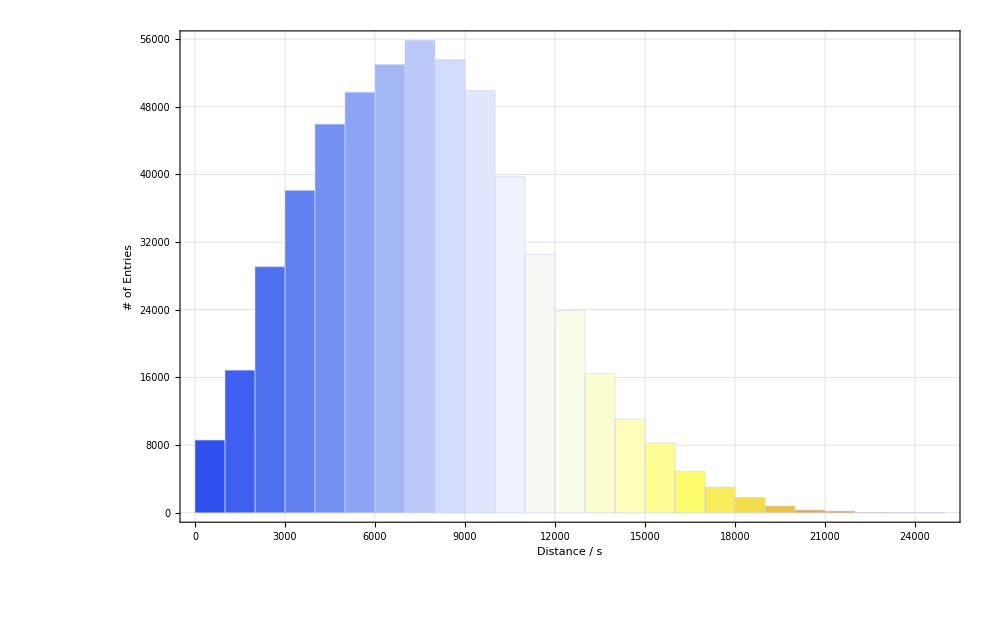

```mathematica
HistDistancesAll=Histogram[distallflat,
Frame->True,
LabelStyle->{30,Black},
FrameLabel->{{"# of Entries",None},{"Distance / s",Style["Distances among Stores",40]}},
LabelStyle->25,
ChartStyle->{{EdgeForm[Thick]},"TemperatureMap"},
PlotTheme->{"Classic","Detailed"},
ImageSize->1000]
```

```mathematica
Mean[distallflat]//N
```

7713.34

```mathematica
Max[distallflat]
TakeSmallest[distallflat,20000];
```

24402

```mathematica
Position[distallflat,Min[DeleteCases[distallflat,0,∞]],3][[1,1]]
```

169

```mathematica
distallflat[[169]]
```

113

```mathematica
Length[distallflat]
```

541696

```mathematica
DeleteCases[{1,1,x,2,3,y,9,y},1]
```

{x,2,3,y,9,y}

```mathematica
Sort[DeleteCases[distallflat,0]]
```

{113,113,116,118,118,142,151,162,165,167,170,171,183,183,184,185,189,190,190,192,198,198,201,202,202,204,204,209,214,218,218,223,226,227,236,238,238,245,246,247,250,250,263,263,268,269,269,269,270,270,271,272,272,272,272,273,274,275,279,279,280,281,284,286,288,288,292,292,292,294,295,297,297,300,302,536403,21694,21697,21697,21709,21712,21724,21727,21735,21751,21756,21765,21770,21778,21783,21793,21798,21813,21817,21830,21838,21841,21859,21895,21896,21897,21926,21955,21956,21957,21966,21979,22002,22009,22023,22079,22100,22141,22154,22161,22200,22214,22218,22260,22272,22282,22286,22324,22369,22374,22376,22456,22540,22569,22627,22719,22771,22814,22943,22976,22998,23166,23239,23594,23676,23698,23708,23885,23966,24085,24143,24145,24197,24329,24402}
 |  |  |  |

```mathematica
Export["DistancesAll.pdf",HistDistancesAll]
```

DistancesAll.pdf

## Analyze Demands

```mathematica
demand=Import["demand_all.dat","Data"];
demand = Flatten[{{1},{1},{1},{1},{1},{2},{2},{1},{1},{1},{1},{3},{2},{1},{2},{3},{1},{2},{5},{0},{3},{1},{1},{3},{1},{1},{1},{2},{1},{4},{2},{1},{3},{1},{1},{1},{3},{2},{2},{2},{1},{1},{1},{1},{2},{1},{1},{1},{1},{3},{1},{1},{1},{4},{2},{2},{2},{1},{2},{1},{1},{1},{2},{1},{1},{2},{2},{3},{1},{2},{2},{1},{3},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{2},{3},{1},{2},{1},{1},{1},{1},{1},{2},{2},{1},{1},{2},{1},{1},{3},{2},{1},{1},{1},{3},{1},{1},{1},{2},{1},{2},{2},{1},{2},{2},{2},{2},{1},{2},{1},{1},{1},{1},{1},{2},{1},{1},{2},{1},{1},{1},{1},{3},{1},{69},{103},{48},{12},{12},{44},{9},{56},{29},{47},{21},{41},{22},{15},{54},{40},{7},{9},{42},{45},{11},{59},{48},{11},{58},{9},{12},{36},{69},{48},{51},{24},{9},{58},{56},{62},{7},{60},{17},{52},{57},{7},{70},{43},{47},{6},{14},{63},{10},{10},{40},{47},{63},{43},{34},{3},{1},{2},{2},{1},{2},{1},{1},{1},{7},{10},{9},{8},{6},{7},{7},{11},{7},{10},{13},{9},{11},{11},{10},{10},{13},{11},{22},{8},{13},{10},{5},{6},{11},{6},{9},{11},{7},{9},{9},{20},{8},{11},{5},{12},{14},{9},{7},{10},{9},{14},{8},{8},{1},{1},{9},{3},{1},{2},{1},{1},{2},{2},{1},{7},{7},{9},{15},{10},{11},{15},{10},{10},{15},{10},{4},{1},{1},{4},{1},{1},{2},{2},{1},{2},{2},{2},{1},{1},{1},{2},{2},{1},{2},{2},{2},{2},{1},{2},{2},{1},{1},{2},{2},{1},{1},{1},{1},{2},{1},{2},{2},{1},{1},{1},{1},{2},{0},{1},{1},{2},{2},{2},{1},{3},{3},{1},{1},{2},{2},{2},{1},{3},{2},{1},{1},{2},{1},{2},{3},{1},{3},{1},{1},{1},{1},{4},{8},{6},{5},{3},{3},{4},{9},{10},{9},{7},{7},{11},{6},{32},{9},{10},{4},{7},{8},{8},{5},{5},{39},{47},{38},{24},{37},{47},{46},{5},{41},{47},{32},{6},{7},{7},{8},{11},{6},{32},{6},{42},{10},{35},{13},{8},{7},{1},{5},{1},{2},{2},{6},{3},{7},{2},{3},{1},{2},{18},{1},{10},{2},{8},{16},{10},{1},{7},{10},{1},{2},{2},{3},{2},{9},{2},{3},{10},{1},{10},{7},{1},{13},{1},{1},{1},{1},{2},{1},{2},{2},{1},{2},{1},{1},{1},{1},{1},{2},{1},{1},{1},{7},{2},{1},{1},{1},{1},{0},{1},{1},{0},{1},{1},{2},{3},{1},{2},{7},{2},{3},{2},{2},{2},{1},{2},{11},{2},{8},{1},{2},{3},{74},{55},{51},{57},{6},{0},{0},{62},{44},{1},{54},{1},{0},{36},{3},{9},{78},{1},{69},{57},{14},{2},{2},{1},{1},{69},{86},{51},{57},{88},{81},{148},{80},{1},{56},{62},{1},{3},{67},{53},{1},{74},{67},{105},{81},{54},{46},{8},{6},{2},{1},{9},{52},{0},{6},{67},{48},{2},{1},{2},{4},{2},{1},{1},{1},{1},{1},{1},{4},{1},{1},{2},{2},{3},{1},{1},{2},{2},{2},{2},{1},{2},{3},{1},{1},{1},{1},{4},{0},{1},{1},{3},{1},{3},{1},{1},{2},{3},{1},{2},{1},{2},{2},{1},{2},{2},{1},{2},{1},{2},{2},{2},{1},{1},{2},{1},{1},{1},{1},{3},{2},{2},{3},{1},{1},{1},{1},{2},{2},{1},{1},{1},{1},{1},{1},{2},{2},{2},{2},{1},{2},{2},{1},{1},{1},{2},{2},{1},{1},{1},{4},{1},{2},{1},{1},{1},{1},{1},{1},{1},{2},{1},{1},{1},{1},{1},{1},{1},{1},{2},{1},{2},{2},{1},{2},{1},{2},{2},{2},{2},{1},{2},{1},{2},{2},{2},{1},{3},{1},{1},{1},{2},{2},{1},{1},{1},{1},{2},{1},{44},{34},{41},{10},{10},{54},{8},{10},{11},{13},{10},{7},{19},{9},{9},{20},{11},{41},{16},{1},{8},{6},{9},{54},{8},{37},{6},{28},{20},{51},{13},{41},{50},{16},{75},{12},{7},{13},{10},{13},{8},{5},{9},{46},{5},{18},{8},{13},{11},{11},{56},{13},{5},{24},{1},{10},{12},{8},{14}}];
```

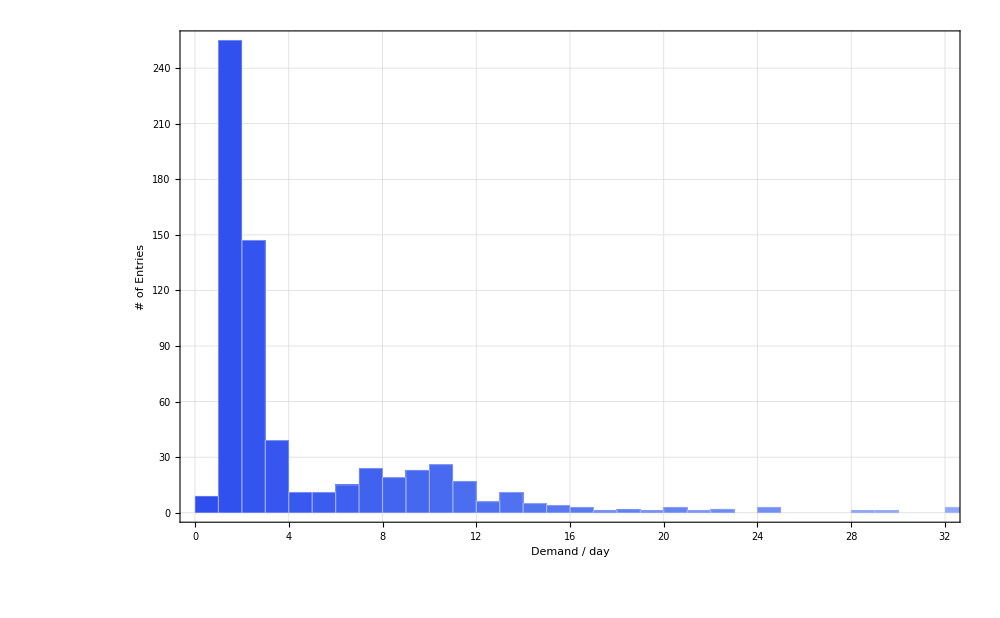

```mathematica
HistDemandAll=Histogram[demand,
Frame->True,
LabelStyle->{30,Black},
FrameLabel->{{"# of Entries",None},{"Demand / day",Style["Demand of Stores",40]}},
LabelStyle->25,
ChartStyle->{{EdgeForm[Thick]},"TemperatureMap"},
PlotTheme->{"Classic","Detailed"},
ImageSize->1000]
```

```mathematica
Export["DemandAll.pdf",HistDemandAll]
```

DemandAll.pdf

```mathematica
demandOA=Flatten[{{0},{7},{2},{1},{9},{2},{1},{2},{8},{1},{1},{10},{5},{1},{24},{2},{2},{1},{1},{1},{1},{1},{3},{1},{44},{7},{29},{47},{1},{103},{63},{2},{1},{41},{9},{2},{2},{2},{3},{0},{2},{1},{3},{2},{2},{1},{3},{1},{1},{1},{5},{1},{1},{2},{7},{1},{1},{1},{3},{1},{1},{36},{54},{3},{62},{9},{86},{57},{148},{1},{62},{3},{11},{1},{42},{7},{1},{13},{1},{1},{2},{1},{12},{1},{0},{1},{13},{2},{2},{55},{51},{57},{6},{0},{28},{1},{2},{1},{2},{2},{1},{1},{1},{20},{2},{1},{1},{1},{11},{2},{1},{2},{20},{1},{1},{13},{53},{74},{67},{81},{6},{9},{2},{4},{1},{1},{67},{1},{3},{51},{2},{1},{2},{2},{2},{1},{24},{1},{1},{1},{21},{15},{42},{45},{11},{58},{12},{48},{51},{2},{58},{70},{47},{6},{10},{34},{1},{1},{9},{11},{9},{1},{1},{1},{2},{1},{1},{3},{1},{1},{1},{1},{1},{2},{10},{1},{1},{1},{2},{2},{2},{1},{3},{2},{1},{2},{10},{12},{32},{9},{10},{5},{47},{46},{32},{7},{8},{11},{32},{3},{8},{7},{1},{2},{3},{2},{10},{2},{10},{2},{2},{1},{14},{1},{2},{11},{15},{10},{4},{4},{4},{2},{2},{2},{2},{0},{2},{1},{1},{2},{1},{3},{3},{1},{1},{3}}];
```

```mathematica
HistDemandOAAll=Histogram[demandOA,
Frame->True,
LabelStyle->{30,Black},
FrameLabel->{{"# of Entries",None},{"Demand / day",Style["Demand of Stores",40]}},
LabelStyle->25,
ChartStyle->{{EdgeForm[Thick]},"TemperatureMap"},
PlotTheme->{"Classic","Detailed"},
ImageSize->1000]
```

```mathematica
Export["DemandOAAll.pdf",HistDemandOAAll]
```

DemandOAAll.pdf

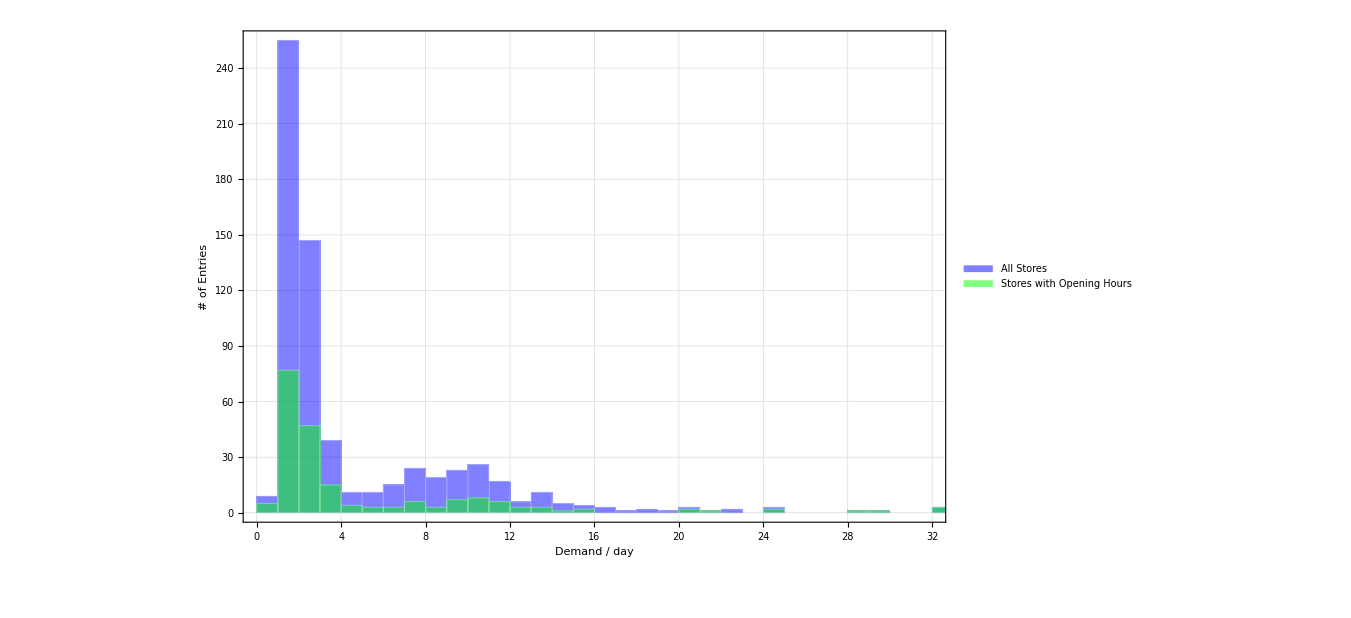

```mathematica
OverlappedHisto=Histogram[{demand,demandOA},
Frame->True,
LabelStyle->{30,Black},
FrameLabel->{{"# of Entries",None},{"Demand / day",Style["Demand of Stores",40]}},
LabelStyle->25,
(*ChartStyle->{{EdgeForm[Thick],EdgeForm[Thick]},{"TemperatureMap",Green}}*)
ChartStyle->{Blue,Green},
PlotTheme->{"Classic","Detailed"},
ImageSize->1000,
ChartLayout->"Overlapped",
ChartLegends->{"All Stores","Stores with Opening Hours"}]
```

```mathematica
Export["DemandAllwOA.pdf",OverlappedHisto]
```

DemandAllwOA.pdf

## Numerical Values

```mathematica
Mean[distallflat]//N
```

7713.34

```mathematica
√Variance[distallflat]//N
```

3718.15